# Numerical simulations in levels

“Unilateral Tax Policy in the Open Economy”
by Miriam Kohl & Philipp M. Richter
December, 2022

```mathematica
Clear[σ,k,ti,tj,τij,τji,Ni,Nj,ϕii,ϕij,ϕjj,ϕji,wi,wj]
```

## Definitions

### General definitions

```mathematica
g[ϕ_,k_]:=PDF[ParetoDistribution[1,k],ϕ];
ζ[σ_,k_]:=k/(k-(σ-1));
λi[σ_,k_,ti_]:=Simplify[(ζ[σ,k](σ-1))/(ζ[σ,k](σ-1)+1-ti)];
λj[σ_,k_,tj_]:=Simplify[(ζ[σ,k](σ-1))/(ζ[σ,k](σ-1)+1-tj)];
```

```mathematica
empty={};
Do[
ti=tiloop;
AppendTo[empty,{tiloop,{}}];
,{tiloop,0.,0.99,0.005}]
```

### Variables

#### Country i

```mathematica
χi[ϕii_,ϕij_,k_]:=(ϕii/ϕij)^k
massLi[ti_,Ni_,σ_,k_]:=λi[σ,k,ti] Ni
massMi[ϕii_,Ni_,k_]:=ϕii^(-k) Ni
massMij[ϕij_,Ni_,k_]:=ϕij^(-k) Ni
avgϕi[ϕii_,ϕij_,σ_,k_] :=(k-(σ-1))/(k-σ)(ϕii^(1-k)+ϕij^(1-k))/(ϕii^(-k)+ϕij^(-k))
aggrRi[wi_,ti_,Ni_,σ_,k_]:=σ/(σ-1)massLi[ti,Ni,σ,k] wi
indexPi[ϕii_,ϕij_,wi_,Ni_,σ_,k_]:=(ζ[σ,k]Ni wi^(1-σ)(σ/(σ-1))^(1-σ)ϕii^(σ-1-k)(1+χi[ϕii,ϕij,k]))^(1/(1-σ))
indexPji[ϕii_,ϕij_,wi_,Ni_,σ_,k_]:=(ζ[σ,k]Ni wi^(1-σ)(σ/(σ-1))^(1-σ)ϕii^(σ-1-k)χi[ϕii,ϕij,k])^(1/(1-σ))
toti[ϕii_,ϕij_,wi_,Ni_,ϕjj_,ϕji_,wj_,Nj_,σ_,k_]:=indexPij[ϕjj,ϕji,wj,Nj,σ,k]/indexPji[ϕii,ϕij,wi,Ni,σ,k]
exporti[ϕij_,wi_,ti_,Ni_,σ_,k_]:=Ni (ϕij)^(-k)ζ[σ,k] σ wi (1-ti)^(-1);
aggrRreali[ϕii_,ϕij_,wi_,Ni_,ti_,σ_,k_]:=aggrRi[wi,ti,Ni,σ,k]/indexPi[ϕii,ϕij,wi,Ni,σ,k]
bi[wi_,ti_,σ_,k_]:=ti 1/(σ-1)λi[σ,k,ti]wi
minInci[wi_,ti_,σ_,k_]:=wi+bi[wi,ti,σ,k]
minIncreali[ϕii_,ϕij_,wi_,Ni_,ti_,σ_,k_]:=minInci[wi,ti,σ,k]/indexPi[ϕii,ϕij,wi,Ni,σ,k]
Ξauti[σ_,k_,ti_]:=(ζ[σ,k] (ζ[σ,k](σ-1)+1))/(ζ[σ,k](σ-1)+1+(ζ[σ,k]-1)ti)
Ξi[ϕii_,ϕij_,σ_,k_,ti_]:=Ξauti[σ,k,ti](1+1/λi[σ,k,ti]((ζ[σ,k]-1)(σ-1))/(ζ[σ,k](σ-1)+1)χi[ϕii,ϕij,k])
```

```mathematica
(* Atkinson [income groups, general SWF for θ≠1 & specific SWF for θ=1]*)
incgr1i[ϕ_,ϕii_,ϕij_,wi_,Ni_,ti_,σ_,k_]:=minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k];
incgr2i[ϕ_,ϕii_,ϕij_,wi_,ti_,Ni_,σ_,k_]:=
(1/σ(1-ti)aggrRi[wi,ti,Ni,σ,k]indexPi[ϕii,ϕij,wi,Ni,σ,k]^(σ-1)(σ/(σ-1)wi)^(1-σ)ϕ^(σ-1)+bi[wi,ti,σ,k])/indexPi[ϕii,ϕij,wi,Ni,σ,k];
incgr3i[ϕ_,ϕii_,ϕij_,ϕjj_,ϕji_,wi_,ti_,Ni_,wj_,tj_,Nj_,σ_,k_,τij_]:=(1/σ(1-ti)aggrRi[wi,ti,Ni,σ,k]indexPi[ϕii,ϕij,wi,Ni,σ,k]^(σ-1)(σ/(σ-1)wi)^(1-σ)ϕ^(σ-1)+1/σ(1-ti)(τij)^(1-σ)aggrRj[wj,tj,Nj,σ,k]indexPj[ϕjj,ϕji,wj,Nj,σ,k]^(σ-1)(σ/(σ-1)wi)^(1-σ)ϕ^(σ-1)-wi+bi[wi,ti,σ,k])/indexPi[ϕii,ϕij,wi,Ni,σ,k];
indexAi[ϕii_,ϕij_,ϕjj_,ϕji_,wi_,ti_,Ni_,wj_,tj_,Nj_,σ_,k_,τij_,θ_]:=1-(Integrate[(incgr1i[ϕ,ϕii,ϕij,wi,Ni,ti,σ,k])^(1-θ)g[ϕ,k],{ϕ,1,ϕii},Assumptions->ϕii>1] + Integrate[(incgr2i[ϕ,ϕii,ϕij,wi,ti,Ni,σ,k])^(1-θ)g[ϕ,k],{ϕ,ϕii, ϕij},Assumptions->{ϕii>1,ϕij>1}]+ Integrate[(incgr3i[ϕ,ϕii,ϕij,ϕjj,ϕji,wi,ti,Ni,wj,tj,Nj,σ,k,τij])^(1-θ)g[ϕ,k],{ϕ,ϕij,∞},Assumptions->ϕij>1])^(1/(1-θ))/(aggrRreali[ϕii,ϕij,wi,Ni,ti,σ,k]/Ni)
welAθi[ϕii_,ϕij_,ϕjj_,ϕji_,wi_,ti_,Ni_,wj_,tj_,Nj_,σ_,k_,τij_,θ_]:=aggrRreali[ϕii,ϕij,wi,Ni,ti,σ,k]/Ni (1-indexAi[ϕii,ϕij,ϕjj,ϕji,wi,ti,Ni,wj,tj,Nj,σ,k,τij,θ])
indexAlnθ10i[ϕii_,ϕij_,ϕjj_,ϕji_,wi_,ti_,Ni_,wj_,tj_,Nj_,σ_,k_,τij_]:=1-(Integrate[Log[incgr1i[ϕ,ϕii,ϕij,wi,Ni,ti,σ,k]]g[ϕ,k],{ϕ,1,ϕii},Assumptions->ϕii>1] + Integrate[Log[incgr2i[ϕ,ϕii,ϕij,wi,ti,Ni,σ,k]]g[ϕ,k],{ϕ,ϕii, ϕij},Assumptions->{ϕii>1,ϕij>1}]+ Integrate[Log[incgr3i[ϕ,ϕii,ϕij,ϕjj,ϕji,wi,ti,Ni,wj,tj,Nj,σ,k,τij]]g[ϕ,k],{ϕ,ϕij,∞},Assumptions->ϕij>1])/(aggrRreali[ϕii,ϕij,wi,Ni,ti,σ,k]/Ni )
welAlnθ10i[ϕii_,ϕij_,ϕjj_,ϕji_,wi_,ti_,Ni_,wj_,tj_,Nj_,σ_,k_,τij_]:=aggrRreali[ϕii,ϕij,wi,Ni,ti,σ,k]/Ni (1-indexAlnθ10i[ϕii,ϕij,ϕjj,ϕji,wi,ti,Ni,wj,tj,Nj,σ,k,τij])
```

```mathematica
(*SEN - Lorenz curve, GINI & SWF *)
α1i[ϕii_,ϕij_,σ_, k_, ti_]:=(λi[σ,k,ti] + χi[ϕii,ϕij,k])/(1+χi[ϕii,ϕij,k]);
α2i[ϕii_,ϕij_,σ_, k_, ti_]:=1-((1-λi[σ,k,ti]) χi[ϕii,ϕij,k])/(1+χi[ϕii,ϕij,k]);
seg1Li[α_,σ_,k_,ti_]:=((σ-1)+ti λi[σ,k,ti])/(σ λi[σ,k,ti])α;
seg2Li[α_,ϕii_,ϕij_,σ_, k_, ti_]:=seg1Li[α1i[ϕii,ϕij,σ, k, ti],σ,k,ti] +1/(1+χi[ϕii,ϕij,k])(1-ti)/σ(1-  (1-α)^(1/ζ[σ,k])((1+χi[ϕii,ϕij,k])/(1-λi[σ,k,ti]))^(1/ζ[σ,k])) +ti/σ((1-λi[σ,k,ti])/(1+χi[ϕii,ϕij,k])  -(1-α));
seg3Li[α_,ϕii_,ϕij_,σ_, k_, ti_]:=seg2Li[α2i[ϕii,ϕij,σ, k, ti],ϕii,ϕij,σ, k, ti] + (1-ti)/σ 1/(1+χi[ϕii,ϕij,k])(1+χi[ϕii,ϕij,k]^((σ-1)/k))(χi[ϕii,ϕij,k]^(1/ζ[σ,k]) - ((1+χi[ϕii,ϕij,k])/(1-λi[σ,k,ti]))^(1/ζ[σ,k])(1-α)^(1/ζ[σ,k])) +(σ-1)/σ 1/λi[σ,k,ti](1-α)-(1-ti)/σ χi[ϕii,ϕij,k]/(1+χi[ϕii,ϕij,k])1/ζ[σ,k] +ti/σ( χi[ϕii,ϕij,k]/(1+χi[ϕii,ϕij,k])(1-λi[σ,k,ti])- (1-α));
indexGi[ϕii_,ϕij_,σ_,k_,ti_]:=1-2(
Integrate[(seg1Li[α,σ,k,ti]),{α,0,α1i[ϕii,ϕij,σ, k, ti]},Assumptions->α1i[ϕii,ϕij,σ, k, ti]>0] +
Integrate[(seg2Li[α,ϕii,ϕij,σ, k, ti]),{α,α1i[ϕii,ϕij,σ, k, ti],α2i[ϕii,ϕij,σ, k, ti]},Assumptions->α2i[ϕii,ϕij,σ, k, ti]>0] +
Integrate[(seg3Li[α,ϕii,ϕij,σ, k, ti]),{α,α2i[ϕii,ϕij,σ, k, ti],1},Assumptions->α2i[ϕii,ϕij,σ, k, ti]>0]
);
welGi[ϕii_,ϕij_,wi_,ti_,Ni_,σ_,k_]:=aggrRreali[ϕii,ϕij,wi,Ni,ti,σ,k]/Ni (1-indexGi[ϕii,ϕij,σ,k,ti]);
```

#### Country j

```mathematica
χj[ϕjj_,ϕji_,k_]:=(ϕjj/ϕji)^k
massLj[tj_,Nj_,σ_,k_]:=λj[σ,k,tj] Nj
massMj[ϕjj_,Nj_,k_]:=ϕjj^(-k) Nj
massMji[ϕji_,Nj_,k_]:=ϕji^(-k) Nj
avgϕj[ϕjj_,ϕji_,σ_,k_] :=(k-(σ-1))/(k-σ)(ϕjj^(1-k)+ϕji^(1-k))/(ϕjj^(-k)+ϕji^(-k))
aggrRj[wj_,tj_,Nj_,σ_,k_]:=σ/(σ-1)massLj[tj,Nj,σ,k] wj
indexPj[ϕjj_,ϕji_,wj_,Nj_,σ_,k_]:=(ζ[σ,k]Nj wj^(1-σ)(σ/(σ-1))^(1-σ)ϕjj^(σ-1-k)(1+χj[ϕjj,ϕji,k]))^(1/(1-σ))
indexPij[ϕjj_,ϕji_,wj_,Nj_,σ_,k_]:=(ζ[σ,k]Nj wj^(1-σ)(σ/(σ-1))^(1-σ)ϕjj^(σ-1-k)χj[ϕjj,ϕji,k])^(1/(1-σ))
exportj[ϕji_,wj_,tj_,Nj_,σ_,k_]:=Nj (ϕji)^(-k)ζ[σ,k] σ wj (1-tj)^(-1);
aggrRrealj[ϕjj_,ϕji_,wj_,Nj_,tj_,σ_,k_]:=aggrRj[wj,tj,Nj,σ,k]/indexPj[ϕjj,ϕji,wj,Nj,σ,k]
bj[wj_,tj_,σ_,k_]:=tj 1/(σ-1)λj[σ,k,tj]wj
minIncj[wj_,tj_,σ_,k_]:=wj+bj[wj,tj,σ,k]
minIncrealj[ϕjj_,ϕji_,wj_,Nj_,tj_,σ_,k_]:=minIncj[wj,tj,σ,k]/indexPj[ϕjj,ϕji,wj,Nj,σ,k]
Ξautj[σ_,k_,tj_]:=(ζ[σ,k] (ζ[σ,k](σ-1)+1))/(ζ[σ,k](σ-1)+1+(ζ[σ,k]-1)tj)
Ξj[ϕjj_,ϕji_,σ_,k_,tj_]:=Ξautj[σ,k,tj](1+1/λj[σ,k,tj]((ζ[σ,k]-1)(σ-1))/(ζ[σ,k](σ-1)+1)χj[ϕjj,ϕji,k])
```

```mathematica
(* Atkinson [income groups, general SWF for θ≠1 & specific SWF for θ=1]*)
incgr1j[ϕ_,ϕjj_,ϕji_,wj_,Nj_,tj_,σ_,k_]:=minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k];
incgr2j[ϕ_,ϕjj_,ϕji_,wj_,tj_,Nj_,σ_,k_]:=
(1/σ(1-tj)aggrRj[wj,tj,Nj,σ,k]indexPj[ϕjj,ϕji,wj,Nj,σ,k]^(σ-1)(σ/(σ-1)wj)^(1-σ)ϕ^(σ-1)+bj[wj,tj,σ,k])/indexPj[ϕjj,ϕji,wj,Nj,σ,k];
incgr3j[ϕ_,ϕjj_,ϕji_,ϕii_,ϕij_,wj_,tj_,Nj_,wi_,ti_,Ni_,σ_,k_,τji_]:=(1/σ(1-tj)aggrRj[wj,tj,Nj,σ,k]indexPj[ϕjj,ϕji,wj,Nj,σ,k]^(σ-1)(σ/(σ-1)wj)^(1-σ)ϕ^(σ-1)+1/σ(1-tj)(τji)^(1-σ)aggrRi[wi,ti,Ni,σ,k]indexPi[ϕii,ϕij,wi,Ni,σ,k]^(σ-1)(σ/(σ-1)wj)^(1-σ)ϕ^(σ-1)-wj+bj[wj,tj,σ,k])/indexPj[ϕjj,ϕji,wj,Nj,σ,k];
indexAj[ϕjj_,ϕji_,ϕii_,ϕij_,wj_,tj_,Nj_,wi_,ti_,Ni_,σ_,k_,τji_,θ_]:=1-(Integrate[(incgr1j[ϕ,ϕjj,ϕji,wj,Nj,tj,σ,k])^(1-θ)g[ϕ,k],{ϕ,1,ϕjj},Assumptions->ϕjj>1] + Integrate[(incgr2j[ϕ,ϕjj,ϕji,wj,tj,Nj,σ,k])^(1-θ)g[ϕ,k],{ϕ,ϕjj, ϕji},Assumptions->{ϕjj>1,ϕji>1}]+ Integrate[(incgr3j[ϕ,ϕjj,ϕji,ϕii,ϕij,wj,tj,Nj,wi,ti,Ni,σ,k,τji])^(1-θ)g[ϕ,k],{ϕ,ϕji,∞},Assumptions->ϕji>1])^(1/(1-θ))/(aggrRrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/Nj)
welAθj[ϕjj_,ϕji_,ϕii_,ϕij_,wj_,tj_,Nj_,wi_,ti_,Ni_,σ_,k_,τji_,θ_]:=aggrRrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/Nj (1-indexAj[ϕjj,ϕji,ϕii,ϕij,wj,tj,Nj,wi,ti,Ni,σ,k,τji,θ])
indexAlnθ10j[ϕjj_,ϕji_,ϕii_,ϕij_,wj_,tj_,Nj_,wi_,ti_,Ni_,σ_,k_,τji_]:=1-(Integrate[Log[incgr1j[ϕ,ϕjj,ϕji,wj,Nj,tj,σ,k]]g[ϕ,k],{ϕ,1,ϕjj},Assumptions->ϕjj>1] + Integrate[Log[incgr2j[ϕ,ϕjj,ϕji,wj,tj,Nj,σ,k]]g[ϕ,k],{ϕ,ϕjj, ϕji},Assumptions->{ϕjj>1,ϕji>1}]+ Integrate[Log[incgr3j[ϕ,ϕjj,ϕji,ϕii,ϕij,wj,tj,Nj,wi,ti,Ni,σ,k,τji]]g[ϕ,k],{ϕ,ϕji,∞},Assumptions->ϕji>1])/(aggrRrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/Nj )
welAlnθ10j[ϕjj_,ϕji_,ϕii_,ϕij_,wj_,tj_,Nj_,wi_,ti_,Ni_,σ_,k_,τji_]:=aggrRrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/Nj (1-indexAlnθ10j[ϕjj,ϕji,ϕii,ϕij,wj,tj,Nj,wi,ti,Ni,σ,k,τji])
indexAbGi[ϕii_,ϕij_,wi_,ti_,Ni_,σ_,k_,θ_]:=1-Ni/aggrRreali[ϕii,ϕij,wi,Ni,ti,σ,k] ((massLi[ti,Ni,σ,k]+χi[ϕii,ϕij,k]massMi[ϕii,Ni,k])/Ni(minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k])^(1-θ)+massMi[ϕii,Ni,k]/Ni(((ζ[σ,k]+(ζ[σ,k]-1)χi[ϕii,ϕij,k])wi+bi[wi,ti,σ,k])/indexPi[ϕii,ϕij,wi,Ni,σ,k])^(1-θ))^(1/(1-θ));
welAbGθi[ϕii_,ϕij_,wi_,ti_,Ni_,σ_,k_,θ_]:=aggrRreali[ϕii,ϕij,wi,Ni,ti,σ,k]/Ni (1-indexAbGi[ϕii,ϕij,wi,ti,Ni,σ,k,θ]);
```

```mathematica
(*SEN - Lorenz curve, GINI & SWF *)
α1j[ϕjj_,ϕji_,σ_, k_, tj_]:=(λj[σ,k,tj] + χj[ϕjj,ϕji,k])/(1+χj[ϕjj,ϕji,k]);
α2j[ϕjj_,ϕji_,σ_, k_, tj_]:=1-((1-λj[σ,k,tj]) χj[ϕjj,ϕji,k])/(1+χj[ϕjj,ϕji,k]);
seg1Lj[α_,σ_,k_,tj_]:=((σ-1)+tj λj[σ,k,tj])/(σ λj[σ,k,tj])α;
seg2Lj[α_,ϕjj_,ϕji_,σ_, k_, tj_]:=seg1Lj[α1j[ϕjj,ϕji,σ, k, tj],σ,k,tj] +1/(1+χj[ϕjj,ϕji,k])(1-tj)/σ(1-  (1-α)^(1/ζ[σ,k])((1+χj[ϕjj,ϕji,k])/(1-λj[σ,k,tj]))^(1/ζ[σ,k])) +tj/σ((1-λj[σ,k,tj])/(1+χj[ϕjj,ϕji,k])  -(1-α));
seg3Lj[α_,ϕjj_,ϕji_,σ_, k_, tj_]:=seg2Lj[α2j[ϕjj,ϕji,σ, k, tj],ϕjj,ϕji,σ, k, tj] + (1-tj)/σ 1/(1+χj[ϕjj,ϕji,k])(1+χj[ϕjj,ϕji,k]^((σ-1)/k))(χj[ϕjj,ϕji,k]^(1/ζ[σ,k]) - ((1+χj[ϕjj,ϕji,k])/(1-λj[σ,k,tj]))^(1/ζ[σ,k])(1-α)^(1/ζ[σ,k])) +(σ-1)/σ 1/λj[σ,k,tj](1-α)-(1-tj)/σ χj[ϕjj,ϕji,k]/(1+χj[ϕjj,ϕji,k])1/ζ[σ,k] +tj/σ( χj[ϕjj,ϕji,k]/(1+χj[ϕjj,ϕji,k])(1-λj[σ,k,tj])- (1-α));
indexGj[ϕjj_,ϕji_,σ_,k_,tj_]:=1-2(
Integrate[(seg1Lj[α,σ,k,tj]),{α,0,α1j[ϕjj,ϕji,σ, k, tj]},Assumptions->α1j[ϕjj,ϕji,σ, k, tj]>0] +
Integrate[(seg2Lj[α,ϕjj,ϕji,σ, k, tj]),{α,α1j[ϕjj,ϕji,σ, k, tj],α2j[ϕjj,ϕji,σ, k, tj]},Assumptions->α2j[ϕjj,ϕji,σ, k, tj]>0] +
Integrate[(seg3Lj[α,ϕjj,ϕji,σ, k, tj]),{α,α2j[ϕjj,ϕji,σ, k, tj],1},Assumptions->α1j[ϕjj,ϕji,σ, k, tj]>0]
);
welGj[ϕjj_,ϕji_,wj_,tj_,Nj_,σ_,k_]:=aggrRrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/Nj (1-indexGi[ϕjj,ϕji,σ,k,tj]);
```

### Equilibrium conditions (LHS = RHS)

```mathematica
lhs1[ϕii_,ϕji_,σ_]:=(ϕii/ϕji)^(σ-1)
rhs1[wi_,wj_,ti_,tj_,τji_,σ_]:=(wi/wj)^σ(1-tj)/(1-ti)(τji)^(1-σ)
lhs2[ϕjj_,ϕij_,σ_]:=(ϕjj/ϕij)^(σ-1)
rhs2[wi_,wj_,ti_,tj_,τij_,σ_]:=(wj/wi)^σ(1-ti)/(1-tj)(τij)^(1-σ)
lhs3[ϕii_,ϕij_,k_]:=(ϕii)^(-k)+(ϕij)^(-k)
rhs3[ti_,σ_,k_]:=1-λi[σ,k,ti]
lhs4[ϕjj_,ϕji_,k_]:=(ϕjj)^(-k)+(ϕji)^(-k)
rhs4[tj_,σ_,k_]:=1-λj[σ,k,tj]
lhs5[ϕij_]:=ϕij
rhs5[ϕji_,wi_,wj_,ti_,tj_,Ni_,Nj_,k_]:=(Ni/Nj(1-tj)/(1-ti)wi/wj)^(1/k)  ϕji
```

```mathematica
(*Trade imbalances*)
```

```mathematica
lhs5TIB[ϕij_,k_]:=ϕij^k
rhs5TIB[ϕij_,ϕji_,wi_,wj_,ti_,tj_,Ni_,Nj_,k_,σ_,imb_]:=(Ni/Nj(1-tj)/(1-ti)wi/wj)  ϕji^k-imb (1-tj)/(Nj wj ζ[σ,k] σ) (ϕij ϕji)^k
```

### File definition

```mathematica
s11111file = FileNameJoin[{$HomeDirectory,"Desktop","s11111.wl"}];
s11112file = FileNameJoin[{$HomeDirectory,"Desktop","s11112.wl"}];
s11113file = FileNameJoin[{$HomeDirectory,"Desktop","s11113.wl"}];
s11211file = FileNameJoin[{$HomeDirectory,"Desktop","s11211.wl"}];
s11311file = FileNameJoin[{$HomeDirectory,"Desktop","s11311.wl"}];
s11111bfile = FileNameJoin[{$HomeDirectory,"Desktop","s11111b.wl"}];
s11111dfile = FileNameJoin[{$HomeDirectory,"Desktop","s11111d.wl"}];
s12111file = FileNameJoin[{$HomeDirectory,"Desktop","s12111.wl"}];
s12211file = FileNameJoin[{$HomeDirectory,"Desktop","s12211.wl"}];
s12111bfile = FileNameJoin[{$HomeDirectory,"Desktop","s12111b.wl"}];
s21111file = FileNameJoin[{$HomeDirectory,"Desktop","s21111.wl"}];
s21211file=FileNameJoin[{$HomeDirectory,"Desktop","s21211.wl"}];
s21111bfile = FileNameJoin[{$HomeDirectory,"Desktop","s21111b.wl"}];
s11111TIBpfile= FileNameJoin[{$HomeDirectory,"Desktop","s11111TIBp.wl"}];
s11111TIBnfile= FileNameJoin[{$HomeDirectory,"Desktop","s11111TIBn.wl"}];
```

## Alternative 1: Scenario calculations and data storing (long running time!)

### Scenario s11111 (base case)

#### Quick testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τij,τji,tj,ti,wj]
wj=1; σ=3.8; 
k=4; τij=τji=1.2; Ni=Nj=100; ti=0.9; tj=0.1;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,2.5},{ϕij,3.5},{wi,0.4},{ϕjj,2},{ϕji,2.4}}] 
toti[ϕii,ϕij,wi,Ni,ϕjj,ϕji,wj,Nj,σ,k]/.solstep1
```

{ϕii→3.46277,ϕij→4.06966,wi→0.823807,ϕjj→2.01286,ϕji→2.46627}

1.02105

```mathematica
Print["Country i - results"]
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.solstep1
welAlnθ10i[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.solstep1
minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.solstep1
indexGi[ϕii/.solstep1,ϕij/.solstep1,σ,k,ti]/.solstep1
welGi[ϕii/.solstep1,ϕij/.solstep1,wi/.solstep1,ti,Ni,σ,k]/.solstep1
Print["Country j - results"]
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.]/.solstep1
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.25]/.solstep1
minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.solstep1
indexGj[ϕjj/.solstep1,ϕji/.solstep1,σ,k,tj]/.solstep1
welGj[ϕjj/.solstep1,ϕji/.solstep1,wj/.solstep1,tj,Nj,σ,k]/.solstep1
```

6.1784

6.14848+0. ⅈ

5.70249+0. ⅈ

5.49426+0. ⅈ

1.66986+0. ⅈ

5.23154+0. ⅈ

5.18777+0. ⅈ

5.04027

5.05453

6.17547

5.74947+0. ⅈ

5.15164

5.1633

#### Calculations - Loop

```mathematica
Clear[s11111sol,s11111wi, s11111ϕii, s11111ϕij, s11111ϕjj, s11111ϕji,s11111χi, s11111massLi, s11111massMi,s11111massMij, s11111avgϕi,  s11111indexPi,s11111toti, s11111bi, s11111Ξauti, s11111Ξi, s11111welAθ00i, s11111welAθ001i, s11111welAθ025i, s11111welAθ05i, s11111welAθ10i,   s11111welAθ15i, s11111welAθ20i, s11111minIncreali,  s11111indexGi, s11111welGi, s11111welAbGθ00i, s11111welAbGθ001i,s11111welAbGθ025i, s11111welAbGθ05i, s11111welAbGθ10i,  s11111welAbGθ15i, s11111welAbGθ20i,
s11111χj, s11111massLj, s11111massMj, s11111massMji, s11111avgϕj, s11111indexPj, s11111bj, s11111Ξj, s11111welAθ00j,  s11111welAθ025j, s11111minIncrealj, s11111indexGj,   s11111welGj] 
(** define empty lists **)
(* The 5 endogenous variables*)
s11111sol={}; s11111wi={}; s11111ϕii={}; s11111ϕij={}; s11111ϕjj={}; s11111ϕji={};
(* variables for country i*)
s11111χi={}; s11111massLi={}; s11111massMi={}; s11111massMij={}; s11111avgϕi ={};  s11111indexPi={};s11111toti={}; s11111bi={}; s11111Ξauti={}; s11111Ξi={}; s11111welAθ00i={}; s11111welAθ001i={}; s11111welAθ025i={}; s11111welAθ05i={}; s11111welAθ10i={};   s11111welAθ15i={}; s11111welAθ20i={}; s11111minIncreali={};  s11111indexGi={}; s11111welGi={};  s11111welAbGθ00i={}; s11111welAbGθ001i={}; s11111welAbGθ025i={}; s11111welAbGθ05i={}; s11111welAbGθ10i={};   s11111welAbGθ15i={}; s11111welAbGθ20i={}; 
(* variables for country j*)
s11111χj={}; s11111massLj={}; s11111massMj={}; s11111massMji={}; s11111avgϕj ={}; s11111indexPj={}; s11111bj={};
s11111Ξj={}; s11111welAθ00j={};  s11111welAθ025j={}; s11111minIncrealj={}; s11111indexGj={};   s11111welGj={}; 
(* Loop *)
wj=1; σ=3.8;
k=4;Ni=Nj=100; τij=τji=1.2;  tj=0.1;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,2.5},{ϕij,3.5},{wi,0.4},{ϕjj,2},{ϕji,2.4}}];
AppendTo[s11111sol,{tiloop,sol}];
AppendTo[s11111wi,{tiloop,wi/.sol}];
AppendTo[s11111ϕii,{tiloop,ϕii/.sol}];
AppendTo[s11111ϕij,{tiloop,ϕij/.sol}];
AppendTo[s11111ϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s11111ϕji,{tiloop,ϕji/.sol}];
(*** Country i ***)
AppendTo[s11111χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s11111massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s11111massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s11111massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s11111avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s11111indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s11111toti,{tiloop,toti[ϕii,ϕij,wi,Ni,ϕjj,ϕji,wj,Nj,σ,k]/.sol}];
AppendTo[s11111bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s11111Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s11111Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s11111welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.sol}];
AppendTo[s11111welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.sol}];
AppendTo[s11111welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.sol}];
AppendTo[s11111welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.sol}];
AppendTo[s11111welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij]/.sol}];
AppendTo[s11111welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.sol}];
AppendTo[s11111welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.sol}];
AppendTo[s11111minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s11111indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s11111welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
AppendTo[s11111welAbGθ00i,{tiloop,welAbGθi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k,0]/.sol}];
AppendTo[s11111welAbGθ001i,{tiloop,welAbGθi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k,0.01]/.sol}];
AppendTo[s11111welAbGθ025i,{tiloop,welAbGθi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k,0.25]/.sol}];
AppendTo[s11111welAbGθ05i,{tiloop,welAbGθi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k,0.5]/.sol}];
AppendTo[s11111welAbGθ15i,{tiloop,welAbGθi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k,1.5]/.sol}];
AppendTo[ s11111welAbGθ20i,{tiloop,welAbGθi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k,2.0]/.sol}];
(*** Country j ***)
AppendTo[s11111χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s11111massLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s11111massMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s11111massMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s11111avgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
AppendTo[s11111indexPj,{tiloop,indexPj[ϕjj,ϕji,wj,Ni,σ,k]/.sol}];
AppendTo[s11111bj,{tiloop,bj[wj,tj,σ,k]/.sol}];
AppendTo[s11111Ξj,{tiloop,Ξj[ϕjj,ϕji,σ,k,tj]/.sol}];
AppendTo[s11111welAθ00j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.]/.sol}];
AppendTo[s11111welAθ025j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.25]/.sol}];
AppendTo[s11111minIncrealj,{tiloop,minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.sol}];
AppendTo[s11111indexGj,{tiloop,indexGj[ϕjj/.sol,ϕji/.sol,σ,k,tj]/.sol}];
AppendTo[s11111welGj,{tiloop,welGj[ϕjj/.sol,ϕji/.sol,wj/.sol,tj,Nj,σ,k]/.sol}];
,{tiloop,0.,0.99,0.005}]]
 (*last run:*)sol
```

{0.4323,Null}

{ϕii→6.21831,ϕij→7.06464,wi→0.679741,ϕjj→1.99296,ϕji→2.52606}

```mathematica
(*Data storing*)
Save[s11111file,{s11111sol,s11111wi, s11111ϕii, s11111ϕij, s11111ϕjj, s11111ϕji,s11111χi, s11111massLi, s11111massMi,s11111massMij, s11111avgϕi,  s11111indexPi, s11111toti, s11111bi, s11111Ξauti, s11111Ξi, s11111welAθ00i, s11111welAθ001i, s11111welAθ025i, s11111welAθ05i, s11111welAθ10i,   s11111welAθ15i, s11111welAθ20i, s11111minIncreali,s11111indexGi, s11111welGi, s11111welAbGθ00i, s11111welAbGθ001i,s11111welAbGθ025i, s11111welAbGθ05i, s11111welAbGθ10i,  s11111welAbGθ15i, s11111welAbGθ20i,s11111χj, s11111massLj, s11111massMj, s11111massMji, s11111avgϕj, s11111indexPj, s11111bj, s11111Ξj, s11111welAθ00j,  s11111welAθ025j, s11111minIncrealj, s11111indexGj,   s11111welGj}]
```

```mathematica
(*quick check: s11111sol*)
```

### Scenario s11112 (high tj=0.5)

#### Quick testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τij,τji,tj,ti,wj]
wj=1; σ=3.8; 
k=4; τij=τji=1.2; Ni=Nj=100; ti=0.99; tj=0.5;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,2.5},{ϕij,3.5},{wi,0.4},{ϕjj,2},{ϕji,2.4}}] 
(*{{ϕii,2},{ϕij,2.4},{wi,1},{ϕjj,2},{ϕji,2.4}}] *)
```

{ϕii→6.21202,ϕij→7.07662,wi→0.717771,ϕjj→2.28727,ϕji→2.89126}

```mathematica
Print["Country i - results"]
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.solstep1
welAlnθ10i[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.solstep1
minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.solstep1
indexGi[ϕii/.solstep1,ϕij/.solstep1,σ,k,ti]/.solstep1
welGi[ϕii/.solstep1,ϕij/.solstep1,wi/.solstep1,ti,Ni,σ,k]/.solstep1
Print["Country j - results"]
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.]/.solstep1
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.25]/.solstep1
minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.solstep1
indexGj[ϕjj/.solstep1,ϕji/.solstep1,σ,k,tj]/.solstep1
welGj[ϕjj/.solstep1,ϕji/.solstep1,wj/.solstep1,tj,Nj,σ,k]/.solstep1
```

Country i - results

4.2944

4.2942+0. ⅈ

4.29122+0. ⅈ

4.28982+0. ⅈ

1.45595+0. ⅈ

4.28797+0. ⅈ

4.28764+0. ⅈ

4.28649

0.00184186

4.28649

Country j - results

5.96533

5.74341+0. ⅈ

5.41589

0.0914616

5.41973

#### Calculations - Loop

```mathematica
Clear[s11112sol,s11112wi, s11112ϕii, s11112ϕij, s11112ϕjj, s11112ϕji,s11112χi, s11112massLi, s11112massMi,s11112massMij, s11112avgϕi,  s11112indexPi, s11112bi, s11112Ξauti, s11112Ξi, s11112welAθ00i, s11112welAθ001i, s11112welAθ025i, s11112welAθ05i, s11112welAθ10i,   s11112welAθ15i, s11112welAθ20i, s11112minIncreali,  s11112indexGi, s11112welGi, s11112welAbGθ00i, s11112welAbGθ001i,s11112welAbGθ025i, s11112welAbGθ05i, s11112welAbGθ10i,  s11112welAbGθ15i, s11112welAbGθ20i,
s11112χj, s11112massLj, s11112massMj, s11112massMji, s11112avgϕj, s11112indexPj, s11112bj, s11112Ξj, s11112welAθ00j,  s11112welAθ025j, s11112minIncrealj, s11112indexGj,   s11112welGj] 
(** define empty lists **)
(* The 5 endogenous variables*)
s11112sol={}; s11112wi={}; s11112ϕii={}; s11112ϕij={}; s11112ϕjj={}; s11112ϕji={};
(* variables for country i*)
s11112χi={}; s11112massLi={}; s11112massMi={}; s11112massMij={}; s11112avgϕi ={};  s11112indexPi={}; s11112bi={}; s11112Ξauti={}; s11112Ξi={}; s11112welAθ00i={}; s11112welAθ001i={}; s11112welAθ025i={}; s11112welAθ05i={}; s11112welAθ10i={};   s11112welAθ15i={}; s11112welAθ20i={}; s11112minIncreali={};  s11112indexGi={}; s11112welGi={};  s11112welAbGθ00i={}; s11112welAbGθ001i={}; s11112welAbGθ025i={}; s11112welAbGθ05i={}; s11112welAbGθ10i={};   s11112welAbGθ15i={}; s11112welAbGθ20i={}; 
(* variables for country j*)
s11112χj={}; s11112massLj={}; s11112massMj={}; s11112massMji={}; s11112avgϕj ={}; s11112indexPj={}; s11112bj={};
s11112Ξj={}; s11112welAθ00j={};  s11112welAθ025j={}; s11112minIncrealj={}; s11112indexGj={};   s11112welGj={}; 
wj=1; σ=3.8;
k=4;Ni=Nj=100; τij=τji=1.2;  tj=0.5;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,2.5},{ϕij,3.5},{wi,0.4},{ϕjj,2},{ϕji,2.4}}];
AppendTo[s11112sol,{tiloop,sol}];
AppendTo[s11112wi,{tiloop,wi/.sol}];
AppendTo[s11112ϕii,{tiloop,ϕii/.sol}];
AppendTo[s11112ϕij,{tiloop,ϕij/.sol}];
AppendTo[s11112ϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s11112ϕji,{tiloop,ϕji/.sol}];
(*** Country i ***)
AppendTo[s11112χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s11112massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s11112massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s11112massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s11112avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s11112indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s11112bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s11112Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s11112Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s11112welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.sol}];
AppendTo[s11112welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.sol}];
AppendTo[s11112welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.sol}];
AppendTo[s11112welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.sol}];
AppendTo[s11112welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij]/.sol}];
AppendTo[s11112welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.sol}];
AppendTo[s11112welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.sol}];
AppendTo[s11112minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s11112indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s11112welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
(*** Country j ***)
AppendTo[s11112χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s11112massLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s11112massMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s11112massMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s11112avgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
AppendTo[s11112indexPj,{tiloop,indexPj[ϕjj,ϕji,wj,Ni,σ,k]/.sol}];
AppendTo[s11112bj,{tiloop,bj[wj,tj,σ,k]/.sol}];
AppendTo[s11112Ξj,{tiloop,Ξj[ϕjj,ϕji,σ,k,tj]/.sol}];
AppendTo[s11112welAθ00j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.]/.sol}];
AppendTo[s11112welAθ025j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.25]/.sol}];
AppendTo[s11112minIncrealj,{tiloop,minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.sol}];
AppendTo[s11112indexGj,{tiloop,indexGj[ϕjj/.sol,ϕji/.sol,σ,k,tj]/.sol}];
AppendTo[s11112welGj,{tiloop,welGj[ϕjj/.sol,ϕji/.sol,wj/.sol,tj,Nj,σ,k]/.sol}];
,{tiloop,0.,0.99,0.005}]]
 (*last run:*)
sol
```

{95002.1,Null}

{ϕii→6.21202,ϕij→7.07662,wi→0.717771,ϕjj→2.28727,ϕji→2.89126}

```mathematica
(*Data storing*)
Save[s11112file,{s11112sol,s11112wi, s11112ϕii, s11112ϕij, s11112ϕjj, s11112ϕji,s11112χi, s11112massLi, s11112massMi,s11112massMij, s11112avgϕi,  s11112indexPi, s11112bi, s11112Ξauti, s11112Ξi, s11112welAθ00i, s11112welAθ001i, s11112welAθ025i, s11112welAθ05i, s11112welAθ10i,   s11112welAθ15i, s11112welAθ20i, s11112minIncreali,s11112indexGi, s11112welGi, s11112χj, s11112massLj, s11112massMj, s11112massMji, s11112avgϕj, s11112indexPj, s11112bj, s11112Ξj, s11112welAθ00j,  s11112welAθ025j, s11112minIncrealj, s11112indexGj,   s11112welGj}]
```

```mathematica
(*quick check: s11112sol*)
```

### Scenario s11113 (low tj=0)

#### Quick testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τij,τji,tj,ti,wj]
wj=1; σ=3.8; 
k=4; τij=τji=1.2; Ni=Nj=100; ti=0.99; tj=0.0;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,2.5},{ϕij,3.5},{wi,0.4},{ϕjj,1.9},{ϕji,2.4}}] 
(*{{ϕii,2},{ϕij,2.4},{wi,1},{ϕjj,2},{ϕji,2.4}}] *)
```

{ϕii→6.21848,ϕij→7.0643,wi→0.672891,ϕjj→1.94583,ϕji→2.46651}

```mathematica
Print["Country i - results"]
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.solstep1
welAlnθ10i[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.solstep1
minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.solstep1
indexGi[ϕii/.solstep1,ϕij/.solstep1,σ,k,ti]/.solstep1
welGi[ϕii/.solstep1,ϕij/.solstep1,wi/.solstep1,ti,Ni,σ,k]/.solstep1
Print["Country j - results"]
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.]/.solstep1
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.25]/.solstep1
minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.solstep1
indexGj[ϕjj/.solstep1,ϕji/.solstep1,σ,k,tj]/.solstep1
welGj[ϕjj/.solstep1,ϕji/.solstep1,wj/.solstep1,tj,Nj,σ,k]/.solstep1
```

Country i - results

4.2944

4.2942+0. ⅈ

4.29122+0. ⅈ

4.28982+0. ⅈ

1.45595+0. ⅈ

4.28797+0. ⅈ

4.28764+0. ⅈ

4.28649

0.00184186

4.28649

Country j - results

5.96533

5.74341+0. ⅈ

5.41589

0.0914616

5.41973

#### Calculations - Loop

```mathematica
Clear[s11113sol,s11113wi, s11113ϕii, s11113ϕij, s11113ϕjj, s11113ϕji,s11113χi, s11113massLi, s11113massMi,s11113massMij, s11113avgϕi,  s11113indexPi, s11113bi, s11113Ξauti, s11113Ξi, s11113welAθ00i, s11113welAθ001i, s11113welAθ025i, s11113welAθ05i, s11113welAθ10i,   s11113welAθ15i, s11113welAθ20i, s11113minIncreali,  s11113indexGi, s11113welGi, s11113welAbGθ00i, s11113welAbGθ001i,s11113welAbGθ025i, s11113welAbGθ05i, s11113welAbGθ10i,  s11113welAbGθ15i, s11113welAbGθ20i,
s11113χj, s11113massLj, s11113massMj, s11113massMji, s11113avgϕj, s11113indexPj, s11113bj, s11113Ξj, s11113welAθ00j,  s11113welAθ025j, s11113minIncrealj, s11113indexGj,   s11113welGj] 
(** define empty lists **)
(* The 5 endogenous variables*)
s11113sol={}; s11113wi={}; s11113ϕii={}; s11113ϕij={}; s11113ϕjj={}; s11113ϕji={};
(* variables for country i*)
s11113χi={}; s11113massLi={}; s11113massMi={}; s11113massMij={}; s11113avgϕi ={};  s11113indexPi={}; s11113bi={}; s11113Ξauti={}; s11113Ξi={}; s11113welAθ00i={}; s11113welAθ001i={}; s11113welAθ025i={}; s11113welAθ05i={}; s11113welAθ10i={};   s11113welAθ15i={}; s11113welAθ20i={}; s11113minIncreali={};  s11113indexGi={}; s11113welGi={};  s11113welAbGθ00i={}; s11113welAbGθ001i={}; s11113welAbGθ025i={}; s11113welAbGθ05i={}; s11113welAbGθ10i={};   s11113welAbGθ15i={}; s11113welAbGθ20i={}; 
(* variables for country j*)
s11113χj={}; s11113massLj={}; s11113massMj={}; s11113massMji={}; s11113avgϕj ={}; s11113indexPj={}; s11113bj={};
s11113Ξj={}; s11113welAθ00j={};  s11113welAθ025j={}; s11113minIncrealj={}; s11113indexGj={};   s11113welGj={}; 
wj=1; σ=3.8;
k=4;Ni=Nj=100; τij=τji=1.2;  tj=0.0;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,2.5},{ϕij,3.5},{wi,0.4},{ϕjj,1.9},{ϕji,2.4}}];
AppendTo[s11113sol,{tiloop,sol}];
AppendTo[s11113wi,{tiloop,wi/.sol}];
AppendTo[s11113ϕii,{tiloop,ϕii/.sol}];
AppendTo[s11113ϕij,{tiloop,ϕij/.sol}];
AppendTo[s11113ϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s11113ϕji,{tiloop,ϕji/.sol}];
(*** Country i ***)
AppendTo[s11113χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s11113massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s11113massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s11113massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s11113avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s11113indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s11113bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s11113Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s11113Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s11113welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.sol}];
AppendTo[s11113welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.sol}];
AppendTo[s11113welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.sol}];
AppendTo[s11113welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.sol}];
AppendTo[s11113welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij]/.sol}];
AppendTo[s11113welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.sol}];
AppendTo[s11113welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.sol}];
AppendTo[s11113minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s11113indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s11113welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
(*** Country j ***)
AppendTo[s11113χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s11113massLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s11113massMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s11113massMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s11113avgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
AppendTo[s11113indexPj,{tiloop,indexPj[ϕjj,ϕji,wj,Ni,σ,k]/.sol}];
AppendTo[s11113bj,{tiloop,bj[wj,tj,σ,k]/.sol}];
AppendTo[s11113Ξj,{tiloop,Ξj[ϕjj,ϕji,σ,k,tj]/.sol}];
AppendTo[s11113welAθ00j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.]/.sol}];
AppendTo[s11113welAθ025j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.25]/.sol}];
AppendTo[s11113minIncrealj,{tiloop,minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.sol}];
AppendTo[s11113indexGj,{tiloop,indexGj[ϕjj/.sol,ϕji/.sol,σ,k,tj]/.sol}];
AppendTo[s11113welGj,{tiloop,welGj[ϕjj/.sol,ϕji/.sol,wj/.sol,tj,Nj,σ,k]/.sol}];
,{tiloop,0.,0.99,0.005}]]
 (*last run:*)
sol
```

{74133.8,Null}

{ϕii→6.21848,ϕij→7.0643,wi→0.672891,ϕjj→1.94583,ϕji→2.46651}

```mathematica
(*Data storing*)
Save[s11113file,{s11113sol,s11113wi, s11113ϕii, s11113ϕij, s11113ϕjj, s11113ϕji,s11113χi, s11113massLi, s11113massMi,s11113massMij, s11113avgϕi,  s11113indexPi, s11113bi, s11113Ξauti, s11113Ξi, s11113welAθ00i, s11113welAθ001i,s11113welAθ025i, s11113welAθ05i, s11113welAθ10i,   s11113welAθ15i, s11113welAθ20i, s11113minIncreali,s11113indexGi, s11113welGi, 
s11113χj, s11113massLj, s11113massMj, s11113massMji, s11113avgϕj, s11113indexPj, s11113bj, s11113Ξj, s11113welAθ00j,  s11113welAθ025j, s11113minIncrealj, s11113indexGj,   s11113welGj}]
```

```mathematica
(*quick check: s11113sol*)
```

### Scenario s11211 (high k=8)

#### Quick testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τij,τji,tj,ti,wj]
wj=1; σ=3.8; 
k=8; τij=τji=1.2; Ni=Nj=100; ti=0.175; tj=0.1;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,1.5},{ϕij,1.8},{wi,1},{ϕjj,1.2},{ϕji,1.5}}]
```

{ϕii→1.29003,ϕij→1.54782,wi→0.983849,ϕjj→1.27832,ϕji→1.5342}

```mathematica
Print["Country i - results"]
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.solstep1
welAlnθ10i[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.solstep1
minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.solstep1
indexGi[ϕii/.solstep1,ϕij/.solstep1,σ,k,ti]/.solstep1
welGi[ϕii/.solstep1,ϕij/.solstep1,wi/.solstep1,ti,Ni,σ,k]/.solstep1
Print["Country j - results"]
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.]/.solstep1
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.25]/.solstep1
minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.solstep1
indexGj[ϕjj/.solstep1,ϕji/.solstep1,σ,k,tj]/.solstep1
welGj[ϕjj/.solstep1,ϕji/.solstep1,wj/.solstep1,tj,Nj,σ,k]/.solstep1
```

Country i - results

3.40462

3.40291+0. ⅈ

3.36756+0. ⅈ

3.3397+0. ⅈ

1.1942+0. ⅈ

3.27537+0. ⅈ

3.25733+0. ⅈ

3.14591

0.0726495

3.15727

Country j - results

3.41237

3.37155+0. ⅈ

3.1295

0.0789779

3.14286

#### Calculations - Loop

```mathematica
Clear[s11211sol,s11211wi, s11211ϕii, s11211ϕij, s11211ϕjj, s11211ϕji,s11211χi, s11211massLi, s11211massMi,s11211massMij, s11211avgϕi,  s11211indexPi,s11211toti, s11211bi, s11211Ξauti, s11211Ξi, s11211welAθ00i, s11211welAθ001i, s11211welAθ025i, s11211welAθ05i, s11211welAθ10i,   s11211welAθ15i, s11211welAθ20i, s11211minIncreali,  s11211indexGi, s11211welGi, s11211welAbGθ00i, s11211welAbGθ001i,s11211welAbGθ025i, s11211welAbGθ05i, s11211welAbGθ10i,  s11211welAbGθ15i, s11211welAbGθ20i,
s11211χj, s11211massLj, s11211massMj, s11211massMji, s11211avgϕj, s11211indexPj, s11211bj, s11211Ξj, s11211welAθ00j,  s11211welAθ025j, s11211minIncrealj, s11211indexGj,   s11211welGj] 
(** define empty lists **)
(* The 5 endogenous variables*)
s11211sol={}; s11211wi={}; s11211ϕii={}; s11211ϕij={}; s11211ϕjj={}; s11211ϕji={};
(* variables for country i*)
s11211χi={}; s11211massLi={}; s11211massMi={}; s11211massMij={}; s11211avgϕi ={};  s11211indexPi={};s11211toti={}; s11211bi={}; s11211Ξauti={}; s11211Ξi={}; s11211welAθ00i={}; s11211welAθ001i={}; s11211welAθ025i={}; s11211welAθ05i={}; s11211welAθ10i={};   s11211welAθ15i={}; s11211welAθ20i={}; s11211minIncreali={};  s11211indexGi={}; s11211welGi={};  s11211welAbGθ00i={}; s11211welAbGθ001i={}; s11211welAbGθ025i={}; s11211welAbGθ05i={}; s11211welAbGθ10i={};   s11211welAbGθ15i={}; s11211welAbGθ20i={}; 
(* variables for country j*)
s11211χj={}; s11211massLj={}; s11211massMj={}; s11211massMji={}; s11211avgϕj ={}; s11211indexPj={}; s11211bj={};
s11211Ξj={}; s11211welAθ00j={};  s11211welAθ025j={}; s11211minIncrealj={}; s11211indexGj={};   s11211welGj={}; 
wj=1; σ=3.8;
k=8;Ni=Nj=100; τij=τji=1.2;  tj=0.1;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,1.5},{ϕij,1.8},{wi,1},{ϕjj,1.2},{ϕji,1.5}}];
AppendTo[s11211sol,{tiloop,sol}];
AppendTo[s11211wi,{tiloop,wi/.sol}];
AppendTo[s11211ϕii,{tiloop,ϕii/.sol}];
AppendTo[s11211ϕij,{tiloop,ϕij/.sol}];
AppendTo[s11211ϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s11211ϕji,{tiloop,ϕji/.sol}];
(*** Country i ***)
AppendTo[s11211χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s11211massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s11211massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s11211massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s11211avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s11211indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s11211toti,{tiloop,toti[ϕii,ϕij,wi,Ni,ϕjj,ϕji,wj,Nj,σ,k]/.sol}];
AppendTo[s11211bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s11211Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s11211Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s11211welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.sol}];
AppendTo[s11211welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.sol}];
AppendTo[s11211welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.sol}];
AppendTo[s11211welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.sol}];
AppendTo[s11211welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij]/.sol}];
AppendTo[s11211welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.sol}];
AppendTo[s11211welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.sol}];
AppendTo[s11211minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s11211indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s11211welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
(*** Country j ***)
AppendTo[s11211χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s11211massLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s11211massMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s11211massMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s11211avgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
AppendTo[s11211indexPj,{tiloop,indexPj[ϕjj,ϕji,wj,Ni,σ,k]/.sol}];
AppendTo[s11211bj,{tiloop,bj[wj,tj,σ,k]/.sol}];
AppendTo[s11211Ξj,{tiloop,Ξj[ϕjj,ϕji,σ,k,tj]/.sol}];
(*AppendTo[s11211welAθ00j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.]/.sol}];
AppendTo[s11211welAθ025j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.25]/.sol}];
AppendTo[s11211minIncrealj,{tiloop,minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.sol}];
AppendTo[s11211indexGj,{tiloop,indexGj[ϕjj/.sol,ϕji/.sol,σ,k,tj]/.sol}];
AppendTo[s11211welGj,{tiloop,welGj[ϕjj/.sol,ϕji/.sol,wj/.sol,tj,Nj,σ,k]/.sol}];*)
,{tiloop,0.,0.99,0.005}]]
 (*last run:*)
sol
```

{0.412965,Null}

{ϕii→2.2149,ϕij→2.53329,wi→0.44538,ϕjj→1.26848,ϕji→1.59703}

```mathematica
(*Data storing*)
Save[s11211file,{s11211sol,s11211wi, s11211ϕii, s11211ϕij, s11211ϕjj, s11211ϕji,s11211χi, s11211massLi, s11211massMi,s11211massMij, s11211avgϕi,  s11211indexPi,s11211toti, s11211bi, s11211Ξauti, s11211Ξi, s11211welAθ00i, s11211welAθ001i, s11211welAθ025i, s11211welAθ05i, s11211welAθ10i,   s11211welAθ15i, s11211welAθ20i, s11211minIncreali,s11211indexGi, s11211welGi, s11211welAbGθ00i, s11211welAbGθ001i,s11211welAbGθ025i, s11211welAbGθ05i, s11211welAbGθ10i,  s11211welAbGθ15i, s11211welAbGθ20i,s11211χj, s11211massLj, s11211massMj, s11211massMji, s11211avgϕj, s11211indexPj, s11211bj, s11211Ξj, s11211welAθ00j,  s11211welAθ025j, s11211minIncrealj, s11211indexGj,   s11211welGj}]
```

```mathematica
(*quick check: s11211sol*)
```

### Scenario s11311 (very high k=40)

#### Quick testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τij,τji,tj,ti,wj]
wj=1; σ=3.8; 
k=40; τij=τji=1.2; Ni=Nj=100; ti=0.99; tj=0.1;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,1.0},{ϕij,1.3},{wi,0.7},{ϕjj,1},{ϕji,1.3}}]
```

{ϕii→1.15349,ϕij→1.36945,wi→0.328276,ϕjj→1.03742,ϕji→1.2583}

```mathematica
Print["Country i - results"]
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.solstep1
welAlnθ10i[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.solstep1
minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.solstep1
indexGi[ϕii/.solstep1,ϕij/.solstep1,σ,k,ti]/.solstep1
welGi[ϕii/.solstep1,ϕij/.solstep1,wi/.solstep1,ti,Ni,σ,k]/.solstep1
Print["Country j - results"]
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.]/.solstep1
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.25]/.solstep1
minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.solstep1
indexGj[ϕjj/.solstep1,ϕji/.solstep1,σ,k,tj]/.solstep1
welGj[ϕjj/.solstep1,ϕji/.solstep1,wj/.solstep1,tj,Nj,σ,k]/.solstep1
```

Country i - results

3.40462

3.40291+0. ⅈ

3.36756+0. ⅈ

3.3397+0. ⅈ

1.1942+0. ⅈ

3.27537+0. ⅈ

3.25733+0. ⅈ

3.14591

0.0726495

3.15727

Country j - results

3.41237

3.37155+0. ⅈ

3.1295

0.0789779

3.14286

#### Calculations - Loop

```mathematica
Clear[s11311sol,s11311wi, s11311ϕii, s11311ϕij, s11311ϕjj, s11311ϕji,s11311χi, s11311massLi, s11311massMi,s11311massMij, s11311avgϕi,  s11311indexPi, s11311bi, s11311Ξauti, s11311Ξi, s11311welAθ00i, s11311welAθ001i, s11311welAθ025i, s11311welAθ05i, s11311welAθ10i,   s11311welAθ15i, s11311welAθ20i, s11311minIncreali,  s11311indexGi, s11311welGi, s11311welAbGθ00i, s11311welAbGθ001i,s11311welAbGθ025i, s11311welAbGθ05i, s11311welAbGθ10i,  s11311welAbGθ15i, s11311welAbGθ20i,
s11311χj, s11311massLj, s11311massMj, s11311massMj, s11311avgϕj, s11311indexPj, s11311bj, s11311Ξj, s11311welAθ00j,  s11311welAθ025j, s11311minIncrealj, s11311indexGj,   s11311welGj] 
(** define empty lists **)
(* The 5 endogenous variables*)
s11311sol={}; s11311wi={}; s11311ϕii={}; s11311ϕij={}; s11311ϕjj={}; s11311ϕji={};
(* variables for country i*)
s11311χi={}; s11311massLi={}; s11311massMi={}; s11311massMij={}; s11311avgϕi ={};  s11311indexPi={}; s11311bi={}; s11311Ξauti={}; s11311Ξi={}; s11311welAθ00i={}; s11311welAθ001i={}; s11311welAθ025i={}; s11311welAθ05i={}; s11311welAθ10i={};   s11311welAθ15i={}; s11311welAθ20i={}; s11311minIncreali={};  s11311indexGi={}; s11311welGi={};  s11311welAbGθ00i={}; s11311welAbGθ001i={}; s11311welAbGθ025i={}; s11311welAbGθ05i={}; s11311welAbGθ10i={};   s11311welAbGθ15i={}; s11311welAbGθ20i={}; 
(* variables for country j*)
s11311χj={}; s11311massLj={}; s11311massMj={}; s11311massMji={}; s11311avgϕj ={}; s11311indexPj={}; s11311bj={};
s11311Ξj={}; s11311welAθ00j={};  s11311welAθ025j={}; s11311minIncrealj={}; s11311indexGj={};   s11311welGj={}; 
wj=1; σ=3.8;
k=40;Ni=Nj=100; τij=τji=1.2;  tj=0.1;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,1.},{ϕij,1.3},{wi,0.7},{ϕjj,1.},{ϕji,1.3}}];
AppendTo[s11311sol,{tiloop,sol}];
AppendTo[s11311wi,{tiloop,wi/.sol}];
AppendTo[s11311ϕii,{tiloop,ϕii/.sol}];
AppendTo[s11311ϕij,{tiloop,ϕij/.sol}];
AppendTo[s11311ϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s11311ϕji,{tiloop,ϕji/.sol}];
(*** Country i ***)
AppendTo[s11311χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s11311massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s11311massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s11311massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s11311avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s11311indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s11311bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s11311Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s11311Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s11311welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.sol}];
AppendTo[s11311welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.sol}];
AppendTo[s11311welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.sol}];
AppendTo[s11311welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.sol}];
AppendTo[s11311welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij]/.sol}];
AppendTo[s11311welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.sol}];
AppendTo[s11311welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.sol}];
AppendTo[s11311minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s11311indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s11311welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
(*** Country j ***)
AppendTo[s11311χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s11311massLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s11311massMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s11311massMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s11311avgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
AppendTo[s11311indexPj,{tiloop,indexPj[ϕjj,ϕji,wj,Ni,σ,k]/.sol}];
AppendTo[s11311bj,{tiloop,bj[wj,tj,σ,k]/.sol}];
AppendTo[s11311Ξj,{tiloop,Ξj[ϕjj,ϕji,σ,k,tj]/.sol}];
AppendTo[s11311welAθ00j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.]/.sol}];
AppendTo[s11311welAθ025j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.25]/.sol}];
AppendTo[s11311minIncrealj,{tiloop,minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.sol}];
AppendTo[s11311indexGj,{tiloop,indexGj[ϕjj/.sol,ϕji/.sol,σ,k,tj]/.sol}];
AppendTo[s11311welGj,{tiloop,welGj[ϕjj/.sol,ϕji/.sol,wj/.sol,tj,Nj,σ,k]/.sol}];
,{tiloop,0.,0.99,0.005}]]
 (*last run:*)
sol
```

{0.376816,Null}

{ϕii→1.15349,ϕij→1.36945,wi→0.328276,ϕjj→1.03742,ϕji→1.2583}

```mathematica
(*Data storing*)
Save[s11311file,{s11311sol,s11311wi, s11311ϕii, s11311ϕij, s11311ϕjj, s11311ϕji,s11311χi, s11311massLi, s11311massMi,s11311massMij, s11311avgϕi,  s11311indexPi, s11311bi, s11311Ξauti, s11311Ξi, s11311welAθ00i, s11311welAθ001i, s11311welAθ025i, s11311welAθ05i, s11311welAθ10i,   s11311welAθ15i, s11311welAθ20i, s11311minIncreali,s11311indexGi, s11311welGi, s11311χj, s11311massLj, s11311massMj, s11311massMj, s11311avgϕj, s11311indexPj, s11311bj, s11311Ξj, s11311welAθ00j,  s11311welAθ025j, s11311minIncrealj, s11311indexGj,   s11311welGj}]
```

```mathematica
(*quick check: 
s11311sol
*)
```

### Scenario s11111b (low σ=2)

#### Quick testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τij,τji,tj,ti,wj]
wj=1; σ=2.; 
k=4; τij=τji=1.2; Ni=Nj=100; ti=0.99; tj=0.1;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,2},{ϕij,2.6},{wi,0.7},{ϕjj,1.5},{ϕji,2}}]
```

{ϕii→4.17751,ϕij→3.93738,wi→0.16688,ϕjj→1.3091,ϕji→2.00007}

```mathematica
Print["Country i - results"]
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.solstep1
welAlnθ10i[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.solstep1
minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.solstep1
indexGi[ϕii/.solstep1,ϕij/.solstep1,σ,k,ti]/.solstep1
welGi[ϕii/.solstep1,ϕij/.solstep1,wi/.solstep1,ti,Ni,σ,k]/.solstep1
Print["Country j - results"]
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.]/.solstep1
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.25]/.solstep1
minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.solstep1
indexGj[ϕjj/.solstep1,ϕji/.solstep1,σ,k,tj]/.solstep1
welGj[ϕjj/.solstep1,ϕji/.solstep1,wj/.solstep1,tj,Nj,σ,k]/.solstep1
```

Country i - results

4.11555

4.11553+0. ⅈ

4.11515+0. ⅈ

4.11482+0. ⅈ

1.41446

4.11384+0. ⅈ

4.1135

4.1104

0.00124798

4.11041

Country j - results

41.9938

41.5879

37.2695

0.0981618

37.8716

#### Calculations - Loop

```mathematica
Clear[s11111bsol,s11111bwi, s11111bϕii, s11111bϕij, s11111bϕjj, s11111bϕji,s11111bχi, s11111bmassLi, s11111bmassMi,s11111bmassMij, s11111bavgϕi,  s11111bindexPi,s11111btoti ,s11111bbi, s11111bΞauti, s11111bΞi, s11111bwelAθ00i, s11111bwelAθ001i, s11111bwelAθ025i, s11111bwelAθ05i, s11111bwelAθ10i,   s11111bwelAθ15i, s11111bwelAθ20i, s11111bminIncreali,  s11111bindexGi, s11111bwelGi, s11111bwelAbGθ00i, s11111bwelAbGθ001i,s11111bwelAbGθ025i, s11111bwelAbGθ05i, s11111bwelAbGθ10i,  s11111bwelAbGθ15i, s11111bwelAbGθ20i,
s11111bχj, s11111bmassLj, s11111bmassMj, s11111bmassMji, s11111bavgϕj, s11111bindexPj, s11111bbj, s11111bΞj, s11111bwelAθ00j,  s11111bwelAθ025j, s11111bminIncrealj, s11111bindexGj,   s11111bwelGj] 
(** define empty lists **)
(* The 5 endogenous variables*)
s11111bsol={}; s11111bwi={}; s11111bϕii={}; s11111bϕij={}; s11111bϕjj={}; s11111bϕji={};
(* variables for country i*)
s11111bχi={}; s11111bmassLi={}; s11111bmassMi={}; s11111bmassMij={}; s11111bavgϕi ={};  s11111bindexPi={}; s11111btoti ={};s11111bbi={}; s11111bΞauti={}; s11111bΞi={}; s11111bwelAθ00i={}; s11111bwelAθ001i={}; s11111bwelAθ025i={}; s11111bwelAθ05i={}; s11111bwelAθ10i={};   s11111bwelAθ15i={}; s11111bwelAθ20i={}; s11111bminIncreali={};  s11111bindexGi={}; s11111bwelGi={};  s11111bwelAbGθ00i={}; s11111bwelAbGθ001i={}; s11111bwelAbGθ025i={}; s11111bwelAbGθ05i={}; s11111bwelAbGθ10i={};   s11111bwelAbGθ15i={}; s11111bwelAbGθ20i={}; 
(* variables for country j*)
s11111bχj={}; s11111bmassLj={}; s11111bmassMj={}; s11111bmassMji={}; s11111bavgϕj ={}; s11111bindexPj={}; s11111bbj={};
s11111bΞj={}; s11111bwelAθ00j={};  s11111bwelAθ025j={}; s11111bminIncrealj={}; s11111bindexGj={};   s11111bwelGj={}; 
wj=1; σ=2;
k=4;Ni=Nj=100; τij=τji=1.2;  tj=0.1;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,2},{ϕij,2.6},{wi,0.7},{ϕjj,1.5},{ϕji,2}}];
AppendTo[s11111bsol,{tiloop,sol}];
AppendTo[s11111bwi,{tiloop,wi/.sol}];
AppendTo[s11111bϕii,{tiloop,ϕii/.sol}];
AppendTo[s11111bϕij,{tiloop,ϕij/.sol}];
AppendTo[s11111bϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s11111bϕji,{tiloop,ϕji/.sol}];
(*** Country i ***)
AppendTo[s11111bχi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s11111bmassLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s11111bmassMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s11111bmassMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s11111bavgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s11111bindexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s11111btoti,{tiloop,toti[ϕii,ϕij,wi,Ni,ϕjj,ϕji,wj,Nj,σ,k]/.sol}];
AppendTo[s11111bbi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s11111bΞauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s11111bΞi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s11111bwelAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.sol}];
AppendTo[s11111bwelAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.sol}];
AppendTo[s11111bwelAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.sol}];
AppendTo[s11111bwelAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.sol}];
AppendTo[s11111bwelAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij]/.sol}];
AppendTo[s11111bwelAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.sol}];
AppendTo[s11111bwelAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.sol}];
AppendTo[s11111bminIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s11111bindexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s11111bwelGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
(*** Country j ***)
AppendTo[s11111bχj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s11111bmassLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s11111bmassMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s11111bmassMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s11111bavgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
AppendTo[s11111bindexPj,{tiloop,indexPj[ϕjj,ϕji,wj,Ni,σ,k]/.sol}];
AppendTo[s11111bbj,{tiloop,bj[wj,tj,σ,k]/.sol}];
AppendTo[s11111bΞj,{tiloop,Ξj[ϕjj,ϕji,σ,k,tj]/.sol}];
AppendTo[s11111bwelAθ00j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.]/.sol}];
AppendTo[s11111bwelAθ025j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.25]/.sol}];
AppendTo[s11111bminIncrealj,{tiloop,minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.sol}];
AppendTo[s11111bindexGj,{tiloop,indexGj[ϕjj/.sol,ϕji/.sol,σ,k,tj]/.sol}];
AppendTo[s11111bwelGj,{tiloop,welGj[ϕjj/.sol,ϕji/.sol,wj/.sol,tj,Nj,σ,k]/.sol}];
,{tiloop,0.,0.99,0.005}]]
(*last run:*)sol
```

{0.232228,Null}

{ϕii→4.17751,ϕij→3.93738,wi→0.16688,ϕjj→1.3091,ϕji→2.00007}

```mathematica
(*Data storing*)
Save[s11111bfile,{s11111bsol,s11111bwi, s11111bϕii, s11111bϕij, s11111bϕjj, s11111bϕji,s11111bχi, s11111bmassLi, s11111bmassMi,s11111bmassMij, s11111bavgϕi,  s11111bindexPi,s11111btoti, s11111bbi, s11111bΞauti, s11111bΞi, s11111bwelAθ00i, s11111bwelAθ001i, s11111bwelAθ025i, s11111bwelAθ05i, s11111bwelAθ10i,   s11111bwelAθ15i, s11111bwelAθ20i, s11111bminIncreali,s11111bindexGi, s11111bwelGi, s11111bχj, s11111bmassLj, s11111bmassMj, s11111bmassMji, s11111bavgϕj, s11111bindexPj, s11111bbj, s11111bΞj, s11111bwelAθ00j,  s11111bwelAθ025j, s11111bminIncrealj, s11111bindexGj,   s11111bwelGj
}]
```

```mathematica
(*quick check: s11111bsol*)
```

### Scenario s11111d (modestly lower σ=3)

#### Quick testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τij,τji,tj,ti,wj]
wj=1; σ=3.; 
k=4; τij=τji=1.2; Ni=Nj=100; ti=0.99; tj=0.1;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,2.2},{ϕij,3.},{wi,0.6},{ϕjj,1.7},{ϕji,2.0}}] 
(*{{ϕii,2},{ϕij,2.6},{wi,0.7},{ϕjj,1.5},{ϕji,2}}] *)
```

{ϕii→5.15322,ϕij→5.52172,wi→0.445143,ϕjj→1.63313,ϕji→2.19477}

```mathematica
Print["Country i - results"]
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.solstep1
welAlnθ10i[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.solstep1
minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.solstep1
indexGi[ϕii/.solstep1,ϕij/.solstep1,σ,k,ti]/.solstep1
welGi[ϕii/.solstep1,ϕij/.solstep1,wi/.solstep1,ti,Ni,σ,k]/.solstep1
Print["Country j - results"]
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.]/.solstep1
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.25]/.solstep1
minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.solstep1
indexGj[ϕjj/.solstep1,ϕji/.solstep1,σ,k,tj]/.solstep1
welGj[ϕjj/.solstep1,ϕji/.solstep1,wj/.solstep1,tj,Nj,σ,k]/.solstep1
```

6.1784

6.14848+0. ⅈ

5.70249+0. ⅈ

5.49426+0. ⅈ

1.66986+0. ⅈ

5.23154+0. ⅈ

5.18777+0. ⅈ

5.04027

5.05453

6.17547

5.74947+0. ⅈ

5.15164

5.1633

#### Calculations - Loop

```mathematica
Clear[s11111dsol,s11111dwi, s11111dϕii, s11111dϕij, s11111dϕjj, s11111dϕji,s11111dχi, s11111dmassLi, s11111dmassMi,s11111dmassMij, s11111davgϕi,  s11111dindexPi,s11111dtoti, s11111dbi, s11111dΞauti, s11111dΞi, s11111dwelAθ00i, s11111dwelAθ001i, s11111dwelAθ025i, s11111dwelAθ05i, s11111dwelAθ10i,   s11111dwelAθ15i, s11111dwelAθ20i, s11111dminIncreali,  s11111dindexGi, s11111dwelGi, s11111dwelAbGθ00i, s11111dwelAbGθ001i,s11111dwelAbGθ025i, s11111dwelAbGθ05i, s11111dwelAbGθ10i,  s11111dwelAbGθ15i, s11111dwelAbGθ20i,
s11111dχj, s11111dmassLj, s11111dmassMj, s11111dmassMji, s11111davgϕj, s11111dindexPj, s11111dbj, s11111dΞj, s11111dwelAθ00j,  s11111dwelAθ025j, s11111dminIncrealj, s11111dindexGj,   s11111dwelGj] 
(** define empty lists **)
(* The 5 endogenous variables*)
s11111dsol={}; s11111dwi={}; s11111dϕii={}; s11111dϕij={}; s11111dϕjj={}; s11111dϕji={};
(* variables for country i*)
s11111dχi={}; s11111dmassLi={}; s11111dmassMi={}; s11111dmassMij={}; s11111davgϕi ={};  s11111dindexPi={};s11111dtoti={}; s11111dbi={}; s11111dΞauti={}; s11111dΞi={}; s11111dwelAθ00i={}; s11111dwelAθ001i={}; s11111dwelAθ025i={}; s11111dwelAθ05i={}; s11111dwelAθ10i={};   s11111dwelAθ15i={}; s11111dwelAθ20i={}; s11111dminIncreali={};  s11111dindexGi={}; s11111dwelGi={};  s11111dwelAbGθ00i={}; s11111dwelAbGθ001i={}; s11111dwelAbGθ025i={}; s11111dwelAbGθ05i={}; s11111dwelAbGθ10i={};   s11111dwelAbGθ15i={}; s11111dwelAbGθ20i={}; 
(* variables for country j*)
s11111dχj={}; s11111dmassLj={}; s11111dmassMj={}; s11111dmassMji={}; s11111davgϕj ={}; s11111dindexPj={}; s11111dbj={};
s11111dΞj={}; s11111dwelAθ00j={};  s11111dwelAθ025j={}; s11111dminIncrealj={}; s11111dindexGj={};   s11111dwelGj={}; 
(* Loop *)
wj=1; σ=3;
k=4;Ni=Nj=100; τij=τji=1.2;  tj=0.1;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,2.2},{ϕij,3.},{wi,0.6},{ϕjj,1.7},{ϕji,2.0}}];
AppendTo[s11111dsol,{tiloop,sol}];
AppendTo[s11111dwi,{tiloop,wi/.sol}];
AppendTo[s11111dϕii,{tiloop,ϕii/.sol}];
AppendTo[s11111dϕij,{tiloop,ϕij/.sol}];
AppendTo[s11111dϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s11111dϕji,{tiloop,ϕji/.sol}];
(*** Country i ***)
AppendTo[s11111dχi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s11111dmassLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s11111dmassMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s11111dmassMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s11111davgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s11111dindexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s11111dtoti,{tiloop,toti[ϕii,ϕij,wi,Ni,ϕjj,ϕji,wj,Nj,σ,k]/.sol}];
AppendTo[s11111dbi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s11111dΞauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s11111dΞi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s11111dwelAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.sol}];
AppendTo[s11111dwelAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.sol}];
AppendTo[s11111dwelAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.sol}];
AppendTo[s11111dwelAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.sol}];
AppendTo[s11111dwelAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij]/.sol}];
AppendTo[s11111dwelAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.sol}];
AppendTo[s11111dwelAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.sol}];
AppendTo[s11111dminIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s11111dindexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s11111dwelGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
(*** Country j ***)
AppendTo[s11111dχj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s11111dmassLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s11111dmassMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s11111dmassMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s11111davgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
AppendTo[s11111dindexPj,{tiloop,indexPj[ϕjj,ϕji,wj,Ni,σ,k]/.sol}];
AppendTo[s11111dbj,{tiloop,bj[wj,tj,σ,k]/.sol}];
AppendTo[s11111dΞj,{tiloop,Ξj[ϕjj,ϕji,σ,k,tj]/.sol}];
AppendTo[s11111dwelAθ00j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.]/.sol}];
AppendTo[s11111dwelAθ025j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.25]/.sol}];
AppendTo[s11111dminIncrealj,{tiloop,minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.sol}];
AppendTo[s11111dindexGj,{tiloop,indexGj[ϕjj/.sol,ϕji/.sol,σ,k,tj]/.sol}];
AppendTo[s11111dwelGj,{tiloop,welGj[ϕjj/.sol,ϕji/.sol,wj/.sol,tj,Nj,σ,k]/.sol}]
,{tiloop,0.,0.99,0.005}]]
 (*last run:*)sol
```

{27906.6,Null}

{ϕii→5.15322,ϕij→5.52172,wi→0.445143,ϕjj→1.63313,ϕji→2.19477}

```mathematica
(*Data storing*)
Save[s11111dfile,{s11111dsol,s11111dwi, s11111dϕii, s11111dϕij, s11111dϕjj, s11111dϕji,s11111dχi, s11111dmassLi, s11111dmassMi,s11111dmassMij, s11111davgϕi,  s11111dindexPi, s11111dtoti, s11111dbi, s11111dΞauti, s11111dΞi, s11111dwelAθ00i, s11111dwelAθ001i, s11111dwelAθ025i, s11111dwelAθ05i, s11111dwelAθ10i,   s11111dwelAθ15i, s11111dwelAθ20i, s11111dminIncreali,s11111dindexGi, s11111dwelGi, s11111dχj, s11111dmassLj, s11111dmassMj, s11111dmassMji, s11111davgϕj, s11111dindexPj, s11111dbj, s11111dΞj, s11111dwelAθ00j,  s11111dwelAθ025j, s11111dminIncrealj, s11111dindexGj,   s11111dwelGj}]
```

```mathematica
(*quick check: s11111dsol*)
```

### Scenario s12111 (autarky)

#### Quick testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τij,τji,tj,ti,wj]
wj=1; σ=3.8; 
k=4; τij=τji=40; Ni=Nj=100; ti=0.99; tj=0.1;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,2},{ϕij,90},{wi,0.9},{ϕjj,1},{ϕji,70}}] 
χi[ϕii,ϕij,k]/.solstep1
```

{ϕii→5.52873,ϕij→212.756,wi→0.669973,ϕjj→1.8363,ϕji→76.3497}

4.56009×10^-7

```mathematica
Print["Country i - results"]
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.solstep1
welAlnθ10i[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.solstep1
minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.solstep1
indexGi[ϕii/.solstep1,ϕij/.solstep1,σ,k,ti]/.solstep1
welGi[ϕii/.solstep1,ϕij/.solstep1,wi/.solstep1,ti,Ni,σ,k]/.solstep1
Print["Country j - results"]
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.]/.solstep1
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.25]/.solstep1
minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.solstep1
indexGj[ϕjj/.solstep1,ϕji/.solstep1,σ,k,tj]/.solstep1
welGj[ϕjj/.solstep1,ϕji/.solstep1,wj/.solstep1,tj,Nj,σ,k]/.solstep1
```

Country i - results

5.36108

5.35409+0. ⅈ

5.24671+0. ⅈ

5.1924+0. ⅈ

1.6369+0. ⅈ

5.11275+0. ⅈ

5.09677+0. ⅈ

5.03024

0.0612171

5.03289

Country j - results

5.59666

5.26671+0. ⅈ

4.66879

0.162425

4.68763

#### Calculations - Loop

```mathematica
Clear[s12111sol,s12111wi, s12111ϕii, s12111ϕij, s12111ϕjj, s12111ϕji,s12111χi, s12111massLi, s12111massMi,s12111massMij, s12111avgϕi,  s12111indexPi, s12111bi, s12111Ξauti, s12111Ξi, s12111welAθ00i, s12111welAθ001i, s12111welAθ025i, s12111welAθ05i, s12111welAθ10i,   s12111welAθ15i, s12111welAθ20i, s12111minIncreali,  s12111indexGi, s12111welGi, s12111welAbGθ00i, s12111welAbGθ001i,s12111welAbGθ025i, s12111welAbGθ05i, s12111welAbGθ10i,  s12111welAbGθ15i, s12111welAbGθ20i,
s12111χj, s12111massLj, s12111massMj, s12111massMji, s12111avgϕj, s12111indexPj, s12111bj, s12111Ξj, s12111welAθ00j,  s12111welAθ025j, s12111minIncrealj, s12111indexGj,   s12111welGj] 
(** define empty lists **)
(* The 5 endogenous variables*)
s12111sol={}; s12111wi={}; s12111ϕii={}; s12111ϕij={}; s12111ϕjj={}; s12111ϕji={};
(* variables for country i*)
s12111χi={}; s12111massLi={}; s12111massMi={}; s12111massMij={}; s12111avgϕi ={};  s12111indexPi={}; s12111bi={}; s12111Ξauti={}; s12111Ξi={}; s12111welAθ00i={}; s12111welAθ001i={}; s12111welAθ025i={}; s12111welAθ05i={}; s12111welAθ10i={};   s12111welAθ15i={}; s12111welAθ20i={}; s12111minIncreali={};  s12111indexGi={}; s12111welGi={};  s12111welAbGθ00i={}; s12111welAbGθ001i={}; s12111welAbGθ025i={}; s12111welAbGθ05i={}; s12111welAbGθ10i={};   s12111welAbGθ15i={}; s12111welAbGθ20i={}; 
(* variables for country j*)
s12111χj={}; s12111massLj={}; s12111massMj={}; s12111massMji={}; s12111avgϕj ={}; s12111indexPj={}; s12111bj={};
s12111Ξj={}; s12111welAθ00j={};  s12111welAθ025j={}; s12111minIncrealj={}; s12111indexGj={};   s12111welGj={}; 
wj=1; σ=3.8;
k=4;Ni=Nj=100; τij=τji=40;  tj=0.1;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,2},{ϕij,90},{wi,0.9},{ϕjj,1},{ϕji,70}}];
AppendTo[s12111sol,{tiloop,sol}];
AppendTo[s12111wi,{tiloop,wi/.sol}];
AppendTo[s12111ϕii,{tiloop,ϕii/.sol}];
AppendTo[s12111ϕij,{tiloop,ϕij/.sol}];
AppendTo[s12111ϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s12111ϕji,{tiloop,ϕji/.sol}];
(*** Country i ***)
AppendTo[s12111χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s12111massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s12111massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s12111massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s12111avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s12111indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s12111bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s12111Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s12111Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s12111welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.sol}];
AppendTo[s12111welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.sol}];
AppendTo[s12111welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.sol}];
AppendTo[s12111welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.sol}];
AppendTo[s12111welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij]/.sol}];
AppendTo[s12111welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.sol}];
AppendTo[s12111welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.sol}];
AppendTo[s12111minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s12111indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s12111welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
(*** Country j ***)
AppendTo[s12111χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
(*AppendTo[s12111massLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s12111massMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s12111massMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s12111avgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
AppendTo[s12111indexPj,{tiloop,indexPj[ϕjj,ϕji,wj,Ni,σ,k]/.sol}];
AppendTo[s12111bj,{tiloop,bj[wj,tj,σ,k]/.sol}];
AppendTo[s12111Ξj,{tiloop,Ξj[ϕjj,ϕji,σ,k,tj]/.sol}];
(*AppendTo[s12111welAθ00j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.]/.sol}];
AppendTo[s12111welAθ025j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.25]/.sol}];
AppendTo[s12111minIncrealj,{tiloop,minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.sol}];
AppendTo[s12111indexGj,{tiloop,indexGj[ϕjj/.sol,ϕji/.sol,σ,k,tj]/.sol}];
AppendTo[s12111welGj,{tiloop,welGj[ϕjj/.sol,ϕji/.sol,wj/.sol,tj,Nj,σ,k]/.sol}];*)
*)
,{tiloop,0.0,0.99,0.005}]]
 (*last run:*)
sol
```

{80657.6,Null}

{ϕii→5.52873,ϕij→212.756,wi→0.669973,ϕjj→1.8363,ϕji→76.3497}

```mathematica
(*Data storing*)
Save[s12111file,{s12111sol,s12111wi, s12111ϕii, s12111ϕij, s12111ϕjj, s12111ϕji,s12111χi, s12111massLi, s12111massMi,s12111massMij, s12111avgϕi,  s12111indexPi, s12111bi, s12111Ξauti, s12111Ξi, s12111welAθ00i, s12111welAθ001i, s12111welAθ025i, s12111welAθ05i, s12111welAθ10i,   s12111welAθ15i, s12111welAθ20i, s12111minIncreali,s12111indexGi, s12111welGi, s12111χj 
(*, s12111massLj, s12111massMj, s12111massMji, s12111avgϕj, s12111indexPj, s12111bj, s12111Ξj, s12111welAθ00j,  s12111welAθ025j, s12111minIncrealj, s12111indexGj,   s12111welGj*)
}]
```

```mathematica
(*quick check: s12111sol*)
```

```mathematica
s12111χi
s12111χj
```

{{0.,3.90542×10^-7},{0.005,3.90542×10^-7},{0.01,3.90543×10^-7},{0.015,3.90544×10^-7},{0.02,3.90545×10^-7},{0.025,3.90547×10^-7},{0.03,3.90549×10^-7},{0.035,3.90552×10^-7},{0.04,3.90555×10^-7},{0.045,3.90558×10^-7},{0.05,3.90562×10^-7},{0.055,3.90566×10^-7},{0.06,3.90571×10^-7},{0.065,3.90576×10^-7},{0.07,3.90582×10^-7},{0.075,3.90588×10^-7},{0.08,3.90594×10^-7},{0.085,3.90601×10^-7},{0.09,3.90609×10^-7},{0.095,3.90617×10^-7},{0.1,3.90625×10^-7},{0.105,3.90634×10^-7},{0.11,3.90643×10^-7},{0.115,3.90653×10^-7},{0.12,3.90663×10^-7},{0.125,3.90674×10^-7},{0.13,3.90686×10^-7},{0.135,3.90697×10^-7},{0.14,3.9071×10^-7},{0.145,3.90723×10^-7},{0.15,3.90736×10^-7},{0.155,3.9075×10^-7},{0.16,3.90765×10^-7},{0.165,3.9078×10^-7},{0.17,3.90796×10^-7},{0.175,3.90812×10^-7},{0.18,3.90829×10^-7},{0.185,3.90846×10^-7},{0.19,3.90864×10^-7},{0.195,3.90883×10^-7},{0.2,3.90902×10^-7},{0.205,3.90922×10^-7},{0.21,3.90942×10^-7},{0.215,3.90964×10^-7},{0.22,3.90985×10^-7},{0.225,3.91008×10^-7},{0.23,3.91031×10^-7},{0.235,3.91055×10^-7},{0.24,3.91079×10^-7},{0.245,3.91104×10^-7},{0.25,3.9113×10^-7},{0.255,3.91157×10^-7},{0.26,3.91184×10^-7},{0.265,3.91212×10^-7},{0.27,3.91241×10^-7},{0.275,3.91271×10^-7},{0.28,3.91301×10^-7},{0.285,3.91332×10^-7},{0.29,3.91364×10^-7},{0.295,3.91397×10^-7},{0.3,3.9143×10^-7},{0.305,3.91465×10^-7},{0.31,3.915×10^-7},{0.315,3.91536×10^-7},{0.32,3.91573×10^-7},{0.325,3.9161×10^-7},{0.33,3.91649×10^-7},{0.335,3.91689×10^-7},{0.34,3.91729×10^-7},{0.345,3.91771×10^-7},{0.35,3.91813×10^-7},{0.355,3.91856×10^-7},{0.36,3.91901×10^-7},{0.365,3.91946×10^-7},{0.37,3.91992×10^-7},{0.375,3.9204×10^-7},{0.38,3.92088×10^-7},{0.385,3.92138×10^-7},{0.39,3.92188×10^-7},{0.395,3.9224×10^-7},{0.4,3.92293×10^-7},{0.405,3.92347×10^-7},{0.41,3.92402×10^-7},{0.415,3.92459×10^-7},{0.42,3.92516×10^-7},{0.425,3.92575×10^-7},{0.43,3.92635×10^-7},{0.435,3.92696×10^-7},{0.44,3.92759×10^-7},{0.445,3.92823×10^-7},{0.45,3.92888×10^-7},{0.455,3.92955×10^-7},{0.46,3.93023×10^-7},{0.465,3.93092×10^-7},{0.47,3.93163×10^-7},{0.475,3.93236×10^-7},{0.48,3.9331×10^-7},{0.485,3.93385×10^-7},{0.49,3.93463×10^-7},{0.495,3.93541×10^-7},{0.5,3.93622×10^-7},{0.505,3.93704×10^-7},{0.51,3.93788×10^-7},{0.515,3.93873×10^-7},{0.52,3.9396×10^-7},{0.525,3.9405×10^-7},{0.53,3.94141×10^-7},{0.535,3.94234×10^-7},{0.54,3.94328×10^-7},{0.545,3.94425×10^-7},{0.55,3.94524×10^-7},{0.555,3.94625×10^-7},{0.56,3.94729×10^-7},{0.565,3.94834×10^-7},{0.57,3.94942×10^-7},{0.575,3.95052×10^-7},{0.58,3.95164×10^-7},{0.585,3.95279×10^-7},{0.59,3.95396×10^-7},{0.595,3.95516×10^-7},{0.6,3.95638×10^-7},{0.605,3.95763×10^-7},{0.61,3.95891×10^-7},{0.615,3.96022×10^-7},{0.62,3.96155×10^-7},{0.625,3.96292×10^-7},{0.63,3.96431×10^-7},{0.635,3.96574×10^-7},{0.64,3.9672×10^-7},{0.645,3.96869×10^-7},{0.65,3.97022×10^-7},{0.655,3.97178×10^-7},{0.66,3.97338×10^-7},{0.665,3.97502×10^-7},{0.67,3.97669×10^-7},{0.675,3.97841×10^-7},{0.68,3.98017×10^-7},{0.685,3.98197×10^-7},{0.69,3.98381×10^-7},{0.695,3.9857×10^-7},{0.7,3.98763×10^-7},{0.705,3.98962×10^-7},{0.71,3.99165×10^-7},{0.715,3.99374×10^-7},{0.72,3.99588×10^-7},{0.725,3.99808×10^-7},{0.73,4.00033×10^-7},{0.735,4.00265×10^-7},{0.74,4.00503×10^-7},{0.745,4.00747×10^-7},{0.75,4.00998×10^-7},{0.755,4.01257×10^-7},{0.76,4.01522×10^-7},{0.765,4.01796×10^-7},{0.77,4.02077×10^-7},{0.775,4.02367×10^-7},{0.78,4.02666×10^-7},{0.785,4.02974×10^-7},{0.79,4.03291×10^-7},{0.795,4.03619×10^-7},{0.8,4.03957×10^-7},{0.805,4.04307×10^-7},{0.81,4.04668×10^-7},{0.815,4.05042×10^-7},{0.82,4.05429×10^-7},{0.825,4.0583×10^-7},{0.83,4.06246×10^-7},{0.835,4.06677×10^-7},{0.84,4.07126×10^-7},{0.845,4.07591×10^-7},{0.85,4.08076×10^-7},{0.855,4.08581×10^-7},{0.86,4.09108×10^-7},{0.865,4.09659×10^-7},{0.87,4.10234×10^-7},{0.875,4.10837×10^-7},{0.88,4.11469×10^-7},{0.885,4.12133×10^-7},{0.89,4.12832×10^-7},{0.895,4.13569×10^-7},{0.9,4.14349×10^-7},{0.905,4.15175×10^-7},{0.91,4.16053×10^-7},{0.915,4.16989×10^-7},{0.92,4.1799×10^-7},{0.925,4.19064×10^-7},{0.93,4.20223×10^-7},{0.935,4.21478×10^-7},{0.94,4.22846×10^-7},{0.945,4.24348×10^-7},{0.95,4.26008×10^-7},{0.955,4.27861×10^-7},{0.96,4.29955×10^-7},{0.965,4.32355×10^-7},{0.97,4.35158×10^-7},{0.975,4.38516×10^-7},{0.98,4.42685×10^-7},{0.985,4.48149×10^-7},{0.99,4.56009×10^-7}}

{{0.,3.90708×10^-7},{0.005,3.90708×10^-7},{0.01,3.90707×10^-7},{0.015,3.90706×10^-7},{0.02,3.90705×10^-7},{0.025,3.90703×10^-7},{0.03,3.90701×10^-7},{0.035,3.90698×10^-7},{0.04,3.90695×10^-7},{0.045,3.90692×10^-7},{0.05,3.90688×10^-7},{0.055,3.90684×10^-7},{0.06,3.90679×10^-7},{0.065,3.90674×10^-7},{0.07,3.90668×10^-7},{0.075,3.90662×10^-7},{0.08,3.90656×10^-7},{0.085,3.90649×10^-7},{0.09,3.90641×10^-7},{0.095,3.90633×10^-7},{0.1,3.90625×10^-7},{0.105,3.90616×10^-7},{0.11,3.90607×10^-7},{0.115,3.90597×10^-7},{0.12,3.90587×10^-7},{0.125,3.90576×10^-7},{0.13,3.90564×10^-7},{0.135,3.90553×10^-7},{0.14,3.9054×10^-7},{0.145,3.90527×10^-7},{0.15,3.90514×10^-7},{0.155,3.905×10^-7},{0.16,3.90485×10^-7},{0.165,3.9047×10^-7},{0.17,3.90454×10^-7},{0.175,3.90438×10^-7},{0.18,3.90421×10^-7},{0.185,3.90404×10^-7},{0.19,3.90386×10^-7},{0.195,3.90367×10^-7},{0.2,3.90348×10^-7},{0.205,3.90328×10^-7},{0.21,3.90308×10^-7},{0.215,3.90287×10^-7},{0.22,3.90265×10^-7},{0.225,3.90242×10^-7},{0.23,3.90219×10^-7},{0.235,3.90196×10^-7},{0.24,3.90171×10^-7},{0.245,3.90146×10^-7},{0.25,3.9012×10^-7},{0.255,3.90094×10^-7},{0.26,3.90067×10^-7},{0.265,3.90039×10^-7},{0.27,3.9001×10^-7},{0.275,3.8998×10^-7},{0.28,3.8995×10^-7},{0.285,3.89919×10^-7},{0.29,3.89887×10^-7},{0.295,3.89855×10^-7},{0.3,3.89821×10^-7},{0.305,3.89787×10^-7},{0.31,3.89752×10^-7},{0.315,3.89716×10^-7},{0.32,3.8968×10^-7},{0.325,3.89642×10^-7},{0.33,3.89604×10^-7},{0.335,3.89564×10^-7},{0.34,3.89524×10^-7},{0.345,3.89483×10^-7},{0.35,3.89441×10^-7},{0.355,3.89397×10^-7},{0.36,3.89353×10^-7},{0.365,3.89308×10^-7},{0.37,3.89262×10^-7},{0.375,3.89215×10^-7},{0.38,3.89167×10^-7},{0.385,3.89118×10^-7},{0.39,3.89068×10^-7},{0.395,3.89016×10^-7},{0.4,3.88964×10^-7},{0.405,3.88911×10^-7},{0.41,3.88856×10^-7},{0.415,3.888×10^-7},{0.42,3.88743×10^-7},{0.425,3.88685×10^-7},{0.43,3.88625×10^-7},{0.435,3.88565×10^-7},{0.44,3.88503×10^-7},{0.445,3.88439×10^-7},{0.45,3.88375×10^-7},{0.455,3.88309×10^-7},{0.46,3.88242×10^-7},{0.465,3.88173×10^-7},{0.47,3.88103×10^-7},{0.475,3.88031×10^-7},{0.48,3.87958×10^-7},{0.485,3.87884×10^-7},{0.49,3.87808×10^-7},{0.495,3.8773×10^-7},{0.5,3.87651×10^-7},{0.505,3.8757×10^-7},{0.51,3.87488×10^-7},{0.515,3.87404×10^-7},{0.52,3.87318×10^-7},{0.525,3.8723×10^-7},{0.53,3.87141×10^-7},{0.535,3.87049×10^-7},{0.54,3.86956×10^-7},{0.545,3.86861×10^-7},{0.55,3.86764×10^-7},{0.555,3.86665×10^-7},{0.56,3.86564×10^-7},{0.565,3.86461×10^-7},{0.57,3.86355×10^-7},{0.575,3.86248×10^-7},{0.58,3.86138×10^-7},{0.585,3.86026×10^-7},{0.59,3.85912×10^-7},{0.595,3.85795×10^-7},{0.6,3.85675×10^-7},{0.605,3.85554×10^-7},{0.61,3.85429×10^-7},{0.615,3.85302×10^-7},{0.62,3.85172×10^-7},{0.625,3.85039×10^-7},{0.63,3.84904×10^-7},{0.635,3.84765×10^-7},{0.64,3.84624×10^-7},{0.645,3.84479×10^-7},{0.65,3.84331×10^-7},{0.655,3.8418×10^-7},{0.66,3.84025×10^-7},{0.665,3.83867×10^-7},{0.67,3.83705×10^-7},{0.675,3.8354×10^-7},{0.68,3.83371×10^-7},{0.685,3.83197×10^-7},{0.69,3.8302×10^-7},{0.695,3.82839×10^-7},{0.7,3.82653×10^-7},{0.705,3.82462×10^-7},{0.71,3.82267×10^-7},{0.715,3.82068×10^-7},{0.72,3.81863×10^-7},{0.725,3.81653×10^-7},{0.73,3.81438×10^-7},{0.735,3.81217×10^-7},{0.74,3.80991×10^-7},{0.745,3.80759×10^-7},{0.75,3.8052×10^-7},{0.755,3.80275×10^-7},{0.76,3.80023×10^-7},{0.765,3.79765×10^-7},{0.77,3.79499×10^-7},{0.775,3.79226×10^-7},{0.78,3.78944×10^-7},{0.785,3.78655×10^-7},{0.79,3.78357×10^-7},{0.795,3.7805×10^-7},{0.8,3.77733×10^-7},{0.805,3.77406×10^-7},{0.81,3.77069×10^-7},{0.815,3.76721×10^-7},{0.82,3.76361×10^-7},{0.825,3.75989×10^-7},{0.83,3.75605×10^-7},{0.835,3.75206×10^-7},{0.84,3.74793×10^-7},{0.845,3.74365×10^-7},{0.85,3.7392×10^-7},{0.855,3.73458×10^-7},{0.86,3.72977×10^-7},{0.865,3.72476×10^-7},{0.87,3.71953×10^-7},{0.875,3.71408×10^-7},{0.88,3.70837×10^-7},{0.885,3.7024×10^-7},{0.89,3.69613×10^-7},{0.895,3.68954×10^-7},{0.9,3.6826×10^-7},{0.905,3.67527×10^-7},{0.91,3.66751×10^-7},{0.915,3.65928×10^-7},{0.92,3.65052×10^-7},{0.925,3.64116×10^-7},{0.93,3.63112×10^-7},{0.935,3.6203×10^-7},{0.94,3.60859×10^-7},{0.945,3.59582×10^-7},{0.95,3.58181×10^-7},{0.955,3.56629×10^-7},{0.96,3.54893×10^-7},{0.965,3.52923×10^-7},{0.97,3.5065×10^-7},{0.975,3.47964×10^-7},{0.98,3.44688×10^-7},{0.985,3.40485×10^-7},{0.99,3.34616×10^-7}}

### Scenario s12211 (autarky - high k=8)

#### Quick testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τij,τji,tj,ti,wj]
wj=1; σ=3.8; 
k=8; τij=τji=40; Ni=Nj=100; ti=0.645; tj=0.1;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,1.7,1,10},{ϕij,60,1,100},{wi,0.8},{ϕjj,1.2,1,10},{ϕji,60,1,100}}] 
χi[ϕii,ϕij,k]/.solstep1
```

{ϕii→1.37975,ϕij→54.978,wi→0.841857,ϕjj→1.24538,ϕji→50.0072}

1.57361×10^-13

```mathematica
Print["Country i - results"]
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.solstep1
welAlnθ10i[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.solstep1
minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.solstep1
indexGi[ϕii/.solstep1,ϕij/.solstep1,σ,k,ti]/.solstep1
welGi[ϕii/.solstep1,ϕij/.solstep1,wi/.solstep1,ti,Ni,σ,k]/.solstep1
Print["Country j - results"]
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.]/.solstep1
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.25]/.solstep1
minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.solstep1
indexGj[ϕjj/.solstep1,ϕji/.solstep1,σ,k,tj]/.solstep1
welGj[ϕjj/.solstep1,ϕji/.solstep1,wj/.solstep1,tj,Nj,σ,k]/.solstep1
```

Country i - results

5.36108

5.35409+0. ⅈ

5.24671+0. ⅈ

5.1924+0. ⅈ

1.6369+0. ⅈ

5.11275+0. ⅈ

5.09677+0. ⅈ

5.03024

0.0612171

5.03289

Country j - results

5.59666

5.26671+0. ⅈ

4.66879

0.162425

4.68763

#### Calculations - Loop

```mathematica
Clear[s12211sol,s12211wi, s12211ϕii, s12211ϕij, s12211ϕjj, s12211ϕji,s12211χi, s12211massLi, s12211massMi,s12211massMij, s12211avgϕi,  s12211indexPi, s12211bi, s12211Ξauti, s12211Ξi, s12211welAθ00i, s12211welAθ001i, s12211welAθ025i, s12211welAθ05i, s12211welAθ10i,   s12211welAθ15i, s12211welAθ20i, s12211minIncreali,  s12211indexGi, s12211welGi, s12211welAbGθ00i, s12211welAbGθ001i,s12211welAbGθ025i, s12211welAbGθ05i, s12211welAbGθ10i,  s12211welAbGθ15i, s12211welAbGθ20i,
s12211χj, s12211massLj, s12211massMj, s12211massMji, s12211avgϕj, s12211indexPj, s12211bj, s12211Ξj, s12211welAθ00j,  s12211welAθ025j, s12211minIncrealj, s12211indexGj,   s12211welGj] 
(** define empty lists **)
(* The 5 endogenous variables*)
s12211sol={}; s12211wi={}; s12211ϕii={}; s12211ϕij={}; s12211ϕjj={}; s12211ϕji={};
(* variables for country i*)
s12211χi={}; s12211massLi={}; s12211massMi={}; s12211massMij={}; s12211avgϕi ={};  s12211indexPi={}; s12211bi={}; s12211Ξauti={}; s12211Ξi={}; s12211welAθ00i={}; s12211welAθ001i={}; s12211welAθ025i={}; s12211welAθ05i={}; s12211welAθ10i={};   s12211welAθ15i={}; s12211welAθ20i={}; s12211minIncreali={};  s12211indexGi={}; s12211welGi={};  s12211welAbGθ00i={}; s12211welAbGθ001i={}; s12211welAbGθ025i={}; s12211welAbGθ05i={}; s12211welAbGθ10i={};   s12211welAbGθ15i={}; s12211welAbGθ20i={}; 
(* variables for country j*)
s12211χj={}; s12211massLj={}; s12211massMj={}; s12211massMji={}; s12211avgϕj ={}; s12211indexPj={}; s12211bj={};
s12211Ξj={}; s12211welAθ00j={};  s12211welAθ025j={}; s12211minIncrealj={}; s12211indexGj={};   s12211welGj={}; 
wj=1; σ=3.8;
k=8;Ni=Nj=100; τij=τji=40;  tj=0.1;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,1.7,1,10},{ϕij,60,1,100},{wi,.8},{ϕjj,1.2,1,10},{ϕji,60,1,100}}] ;
AppendTo[s12211sol,{tiloop,sol}];
AppendTo[s12211wi,{tiloop,wi/.sol}];
AppendTo[s12211ϕii,{tiloop,ϕii/.sol}];
AppendTo[s12211ϕij,{tiloop,ϕij/.sol}];
AppendTo[s12211ϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s12211ϕji,{tiloop,ϕji/.sol}];
(*** Country i ***)
AppendTo[s12211χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s12211massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s12211massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s12211massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s12211avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s12211indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s12211bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s12211Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s12211Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s12211welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.sol}];
AppendTo[s12211welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.sol}];
AppendTo[s12211welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.sol}];
AppendTo[s12211welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.sol}];
AppendTo[s12211welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij]/.sol}];
AppendTo[s12211welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.sol}];
AppendTo[s12211welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.sol}];
AppendTo[s12211minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s12211indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s12211welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
(*** Country j ***)
AppendTo[s12211χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
(*AppendTo[s12211massLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s12211massMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s12211massMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s12211avgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
AppendTo[s12211indexPj,{tiloop,indexPj[ϕjj,ϕji,wj,Ni,σ,k]/.sol}];
AppendTo[s12211bj,{tiloop,bj[wj,tj,σ,k]/.sol}];
AppendTo[s12211Ξj,{tiloop,Ξj[ϕjj,ϕji,σ,k,tj]/.sol}];
AppendTo[s12211welAθ00j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.]/.sol}];
AppendTo[s12211welAθ025j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.25]/.sol}];
AppendTo[s12211minIncrealj,{tiloop,minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.sol}];
AppendTo[s12211indexGj,{tiloop,indexGj[ϕjj/.sol,ϕji/.sol,σ,k,tj]/.sol}];
AppendTo[s12211welGj,{tiloop,welGj[ϕjj/.sol,ϕji/.sol,wj/.sol,tj,Nj,σ,k]/.sol}];
*)
,{tiloop,0.0,0.5,0.005}]]
(*,{tiloop,0.505,0.99,0.005}*)
 (*last run:*)
sol
```

{475.074,Null}

{ϕii→1.327,ϕij→52.9828,wi→0.896502,ϕjj→1.24538,ϕji→49.9064}

```mathematica
(*Data storing*)
Save[s12211file,{s12211sol,s12211wi, s12211ϕii, s12211ϕij, s12211ϕjj, s12211ϕji,s12211χi, s12211massLi, s12211massMi,s12211massMij, s12211avgϕi,  s12211indexPi, s12211bi, s12211Ξauti, s12211Ξi, 
s12211welAθ00i, s12211welAθ001i, s12211welAθ025i, s12211welAθ05i, s12211welAθ10i,   s12211welAθ15i, s12211welAθ20i, s12211minIncreali,s12211indexGi, s12211welGi, s12211χj 
(*, s12211massLj, s12211massMj, s12211massMji, s12211avgϕj, s12211indexPj, s12211bj, s12211Ξj 
, s12211welAθ00j,  s12211welAθ025j, s12211minIncrealj, s12211indexGj,   s12211welGj*)
}]
```

```mathematica
(*quick check: s12211sol*)
```

```mathematica
s12211χi
s12211χj
```

{{0.,1.52528×10^-13},{0.005,1.52528×10^-13},{0.01,1.52528×10^-13},{0.015,1.52529×10^-13},{0.02,1.5253×10^-13},{0.025,1.52531×10^-13},{0.03,1.52533×10^-13},{0.035,1.52535×10^-13},{0.04,1.52537×10^-13},{0.045,1.52539×10^-13},{0.05,1.52542×10^-13},{0.055,1.52545×10^-13},{0.06,1.52549×10^-13},{0.065,1.52552×10^-13},{0.07,1.52556×10^-13},{0.075,1.52561×10^-13},{0.08,1.52566×10^-13},{0.085,1.52571×10^-13},{0.09,1.52576×10^-13},{0.095,1.52582×10^-13},{0.1,1.52588×10^-13},{0.105,1.52594×10^-13},{0.11,1.52601×10^-13},{0.115,1.52608×10^-13},{0.12,1.52616×10^-13},{0.125,1.52624×10^-13},{0.13,1.52632×10^-13},{0.135,1.52641×10^-13},{0.14,1.5265×10^-13},{0.145,1.52659×10^-13},{0.15,1.52669×10^-13},{0.155,1.5268×10^-13},{0.16,1.5269×10^-13},{0.165,1.52701×10^-13},{0.17,1.52713×10^-13},{0.175,1.52725×10^-13},{0.18,1.52737×10^-13},{0.185,1.5275×10^-13},{0.19,1.52764×10^-13},{0.195,1.52777×10^-13},{0.2,1.52791×10^-13},{0.205,1.52806×10^-13},{0.21,1.52821×10^-13},{0.215,1.52837×10^-13},{0.22,1.52853×10^-13},{0.225,1.5287×10^-13},{0.23,1.52887×10^-13},{0.235,1.52904×10^-13},{0.24,1.52923×10^-13},{0.245,1.52941×10^-13},{0.25,1.5296×10^-13},{0.255,1.5298×10^-13},{0.26,1.53×10^-13},{0.265,1.53021×10^-13},{0.27,1.53043×10^-13},{0.275,1.53065×10^-13},{0.28,1.53087×10^-13},{0.285,1.5311×10^-13},{0.29,1.53134×10^-13},{0.295,1.53159×10^-13},{0.3,1.53184×10^-13},{0.305,1.53209×10^-13},{0.31,1.53235×10^-13},{0.315,1.53262×10^-13},{0.32,1.5329×10^-13},{0.325,1.53318×10^-13},{0.33,1.53347×10^-13},{0.335,1.53377×10^-13},{0.34,1.53407×10^-13},{0.345,1.53438×10^-13},{0.35,1.5347×10^-13},{0.355,1.53503×10^-13},{0.36,1.53536×10^-13},{0.365,1.5357×10^-13},{0.37,1.53605×10^-13},{0.375,1.53641×10^-13},{0.38,1.53677×10^-13},{0.385,1.53714×10^-13},{0.39,1.53753×10^-13},{0.395,1.53792×10^-13},{0.4,1.53832×10^-13},{0.405,1.53872×10^-13},{0.41,1.53914×10^-13},{0.415,1.53957×10^-13},{0.42,1.54×10^-13},{0.425,1.54045×10^-13},{0.43,1.5409×10^-13},{0.435,1.54137×10^-13},{0.44,1.54184×10^-13},{0.445,1.54233×10^-13},{0.45,1.54283×10^-13},{0.455,1.54333×10^-13},{0.46,1.54385×10^-13},{0.465,1.54438×10^-13},{0.47,1.54492×10^-13},{0.475,1.54548×10^-13},{0.48,1.54604×10^-13},{0.485,1.54662×10^-13},{0.49,1.54721×10^-13},{0.495,1.54781×10^-13},{0.5,1.54842×10^-13}}

{{0.,1.52648×10^-13},{0.005,1.52648×10^-13},{0.01,1.52648×10^-13},{0.015,1.52647×10^-13},{0.02,1.52646×10^-13},{0.025,1.52645×10^-13},{0.03,1.52643×10^-13},{0.035,1.52641×10^-13},{0.04,1.52639×10^-13},{0.045,1.52637×10^-13},{0.05,1.52634×10^-13},{0.055,1.52631×10^-13},{0.06,1.52627×10^-13},{0.065,1.52623×10^-13},{0.07,1.52619×10^-13},{0.075,1.52615×10^-13},{0.08,1.5261×10^-13},{0.085,1.52605×10^-13},{0.09,1.526×10^-13},{0.095,1.52594×10^-13},{0.1,1.52588×10^-13},{0.105,1.52581×10^-13},{0.11,1.52575×10^-13},{0.115,1.52567×10^-13},{0.12,1.5256×10^-13},{0.125,1.52552×10^-13},{0.13,1.52544×10^-13},{0.135,1.52535×10^-13},{0.14,1.52526×10^-13},{0.145,1.52516×10^-13},{0.15,1.52506×10^-13},{0.155,1.52496×10^-13},{0.16,1.52486×10^-13},{0.165,1.52474×10^-13},{0.17,1.52463×10^-13},{0.175,1.52451×10^-13},{0.18,1.52439×10^-13},{0.185,1.52426×10^-13},{0.19,1.52412×10^-13},{0.195,1.52399×10^-13},{0.2,1.52385×10^-13},{0.205,1.5237×10^-13},{0.21,1.52355×10^-13},{0.215,1.52339×10^-13},{0.22,1.52323×10^-13},{0.225,1.52307×10^-13},{0.23,1.5229×10^-13},{0.235,1.52272×10^-13},{0.24,1.52254×10^-13},{0.245,1.52235×10^-13},{0.25,1.52216×10^-13},{0.255,1.52197×10^-13},{0.26,1.52176×10^-13},{0.265,1.52156×10^-13},{0.27,1.52134×10^-13},{0.275,1.52113×10^-13},{0.28,1.5209×10^-13},{0.285,1.52067×10^-13},{0.29,1.52044×10^-13},{0.295,1.52019×10^-13},{0.3,1.51995×10^-13},{0.305,1.51969×10^-13},{0.31,1.51943×10^-13},{0.315,1.51916×10^-13},{0.32,1.51889×10^-13},{0.325,1.51861×10^-13},{0.33,1.51832×10^-13},{0.335,1.51803×10^-13},{0.34,1.51773×10^-13},{0.345,1.51742×10^-13},{0.35,1.51711×10^-13},{0.355,1.51679×10^-13},{0.36,1.51646×10^-13},{0.365,1.51612×10^-13},{0.37,1.51578×10^-13},{0.375,1.51542×10^-13},{0.38,1.51506×10^-13},{0.385,1.5147×10^-13},{0.39,1.51432×10^-13},{0.395,1.51394×10^-13},{0.4,1.51354×10^-13},{0.405,1.51314×10^-13},{0.41,1.51273×10^-13},{0.415,1.51231×10^-13},{0.42,1.51188×10^-13},{0.425,1.51145×10^-13},{0.43,1.511×10^-13},{0.435,1.51054×10^-13},{0.44,1.51008×10^-13},{0.445,1.5096×10^-13},{0.45,1.50912×10^-13},{0.455,1.50862×10^-13},{0.46,1.50811×10^-13},{0.465,1.5076×10^-13},{0.47,1.50707×10^-13},{0.475,1.50653×10^-13},{0.48,1.50598×10^-13},{0.485,1.50542×10^-13},{0.49,1.50484×10^-13},{0.495,1.50426×10^-13},{0.5,1.50366×10^-13}}

### Scenario s12111b (autarky - low σ=2)

#### Quick testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τij,τji,tj,ti,wj]
wj=1; σ=2.0; 
k=4; τij=τji=40; Ni=Nj=100; ti=0.00; tj=0.1;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,1.3,1,10},{ϕij,60,1,200},{wi,0.9,0,2},{ϕjj,1.25,1,10},{ϕji,60,1,200}}] 
χi[ϕii,ϕij,k]/.solstep1
```

{ϕii→1.23593,ϕij→49.445,wi→1.0461,ϕjj→1.2551,ϕji→50.196}

3.90379×10^-7

```mathematica
Print["Country i - results"]
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.solstep1
welAlnθ10i[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.solstep1
minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.solstep1
indexGi[ϕii/.solstep1,ϕij/.solstep1,σ,k,ti]/.solstep1
welGi[ϕii/.solstep1,ϕij/.solstep1,wi/.solstep1,ti,Ni,σ,k]/.solstep1
Print["Country j - results"]
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.]/.solstep1
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.25]/.solstep1
minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.solstep1
indexGj[ϕjj/.solstep1,ϕji/.solstep1,σ,k,tj]/.solstep1
welGj[ϕjj/.solstep1,ϕji/.solstep1,wj/.solstep1,tj,Nj,σ,k]/.solstep1
```

Country i - results

5.36108

5.35409+0. ⅈ

5.24671+0. ⅈ

5.1924+0. ⅈ

1.6369+0. ⅈ

5.11275+0. ⅈ

5.09677+0. ⅈ

5.03024

0.0612171

5.03289

Country j - results

5.59666

5.26671+0. ⅈ

4.66879

0.162425

4.68763

#### Calculations - Loop

```mathematica
Clear[s12111bsol,s12111bwi, s12111bϕii, s12111bϕij, s12111bϕjj, s12111bϕji,s12111bχi, s12111bmassLi, s12111bmassMi,s12111bmassMij, s12111bavgϕi,  s12111bindexPi, s12111bbi, s12111bΞauti, s12111bΞi, s12111bwelAθ00i, s12111bwelAθ001i, s12111bwelAθ025i, s12111bwelAθ05i, s12111bwelAθ10i,   s12111bwelAθ15i, s12111bwelAθ20i, s12111bminIncreali,  s12111bindexGi, s12111bwelGi, s12111bwelAbGθ00i, s12111bwelAbGθ001i,s12111bwelAbGθ025i, s12111bwelAbGθ05i, s12111bwelAbGθ10i,  s12111bwelAbGθ15i, s12111bwelAbGθ20i,
s12111bχj, s12111bmassLj, s12111bmassMj, s12111bmassMji, s12111bavgϕj, s12111bindexPj, s12111bbj, s12111bΞj, s12111bwelAθ00j,  s12111bwelAθ025j, s12111bminIncrealj, s12111bindexGj,   s12111bwelGj] 
(** define empty lists **)
(* The 5 endogenous variables*)
s12111bsol={}; s12111bwi={}; s12111bϕii={}; s12111bϕij={}; s12111bϕjj={}; s12111bϕji={};
(* variables for country i*)
s12111bχi={}; s12111bmassLi={}; s12111bmassMi={}; s12111bmassMij={}; s12111bavgϕi ={};  s12111bindexPi={}; s12111bbi={}; s12111bΞauti={}; s12111bΞi={}; s12111bwelAθ00i={}; s12111bwelAθ001i={}; s12111bwelAθ025i={}; s12111bwelAθ05i={}; s12111bwelAθ10i={};   s12111bwelAθ15i={}; s12111bwelAθ20i={}; s12111bminIncreali={};  s12111bindexGi={}; s12111bwelGi={};  s12111bwelAbGθ00i={}; s12111bwelAbGθ001i={}; s12111bwelAbGθ025i={}; s12111bwelAbGθ05i={}; s12111bwelAbGθ10i={};   s12111bwelAbGθ15i={}; s12111bwelAbGθ20i={}; 
(* variables for country j*)
s12111bχj={}; s12111bmassLj={}; s12111bmassMj={}; s12111bmassMji={}; s12111bavgϕj ={}; s12111bindexPj={}; s12111bbj={};
s12111bΞj={}; s12111bwelAθ00j={};  s12111bwelAθ025j={}; s12111bminIncrealj={}; s12111bindexGj={};   s12111bwelGj={}; 
wj=1; σ=2.0;
k=4;Ni=Nj=100; τij=τji=40;  tj=0.1;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,1.2,1,5},{ϕij,50,1,200},{wi,0.8,0,2},{ϕjj,1.2,1,5},{ϕji,50,1,200}}] ;
AppendTo[s12111bsol,{tiloop,sol}];
AppendTo[s12111bwi,{tiloop,wi/.sol}];
AppendTo[s12111bϕii,{tiloop,ϕii/.sol}];
AppendTo[s12111bϕij,{tiloop,ϕij/.sol}];
AppendTo[s12111bϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s12111bϕji,{tiloop,ϕji/.sol}];
(*** Country i ***)
AppendTo[s12111bχi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s12111bmassLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s12111bmassMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s12111bmassMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s12111bavgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s12111bindexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s12111bbi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s12111bΞauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s12111bΞi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s12111bwelAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.sol}];
AppendTo[s12111bwelAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.sol}];
AppendTo[s12111bwelAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.sol}];
AppendTo[s12111bwelAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.sol}];
AppendTo[s12111bwelAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij]/.sol}];
AppendTo[s12111bwelAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.sol}];
AppendTo[s12111bwelAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.sol}];
AppendTo[s12111bminIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s12111bindexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s12111bwelGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
(*** Country j ***)
AppendTo[s12111bχj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
(*AppendTo[s12111bmassLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s12111bmassMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s12111bmassMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s12111bavgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
AppendTo[s12111bindexPj,{tiloop,indexPj[ϕjj,ϕji,wj,Ni,σ,k]/.sol}];
AppendTo[s12111bbj,{tiloop,bj[wj,tj,σ,k]/.sol}];
AppendTo[s12111bΞj,{tiloop,Ξj[ϕjj,ϕji,σ,k,tj]/.sol}];
AppendTo[s12111bwelAθ00j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.]/.sol}];
AppendTo[s12111bwelAθ025j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.25]/.sol}];
AppendTo[s12111bminIncrealj,{tiloop,minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.sol}];
AppendTo[s12111bindexGj,{tiloop,indexGj[ϕjj/.sol,ϕji/.sol,σ,k,tj]/.sol}];
AppendTo[s12111bwelGj,{tiloop,welGj[ϕjj/.sol,ϕji/.sol,wj/.sol,tj,Nj,σ,k]/.sol}];
*)
,{tiloop,0.505,0.99,0.005}]]
 (*last run:*)
sol
```

{0.291989,Null}

{ϕii→3.40444,ϕij→115.385,wi→0.159803,ϕjj→1.2551,ϕji→59.2507}

```mathematica
(*Data storing*)
Save[s12111bfile,{s12111bsol,s12111bwi, s12111bϕii, s12111bϕij, s12111bϕjj, s12111bϕji,s12111bχi, s12111bmassLi, s12111bmassMi,s12111bmassMij, s12111bavgϕi,  s12111bindexPi, s12111bbi, s12111bΞauti, s12111bΞi, 
s12111bwelAθ00i, s12111bwelAθ001i, s12111bwelAθ025i, s12111bwelAθ05i, s12111bwelAθ10i,   s12111bwelAθ15i, s12111bwelAθ20i, s12111bminIncreali,s12111bindexGi, s12111bwelGi, s12111bχj , s12111bmassLj, s12111bmassMj, s12111bmassMji, s12111bavgϕj, s12111bindexPj, s12111bbj, s12111bΞj, s12111bwelAθ00j,  s12111bwelAθ025j, s12111bminIncrealj, s12111bindexGj,   s12111bwelGj
}]
```

```mathematica
(*quick check: s12111bsol*)
```

```mathematica
s12111bχi
s12111bχj
```

{{0.,3.90379×10^-7},{0.005,3.90379×10^-7},{0.01,3.90381×10^-7},{0.015,3.90384×10^-7},{0.02,3.90388×10^-7},{0.025,3.90393×10^-7},{0.03,3.90399×10^-7},{0.035,3.90407×10^-7},{0.04,3.90416×10^-7},{0.045,3.90426×10^-7},{0.05,3.90437×10^-7},{0.055,3.9045×10^-7},{0.06,3.90464×10^-7},{0.065,3.90479×10^-7},{0.07,3.90496×10^-7},{0.075,3.90514×10^-7},{0.08,3.90533×10^-7},{0.085,3.90554×10^-7},{0.09,3.90576×10^-7},{0.095,3.906×10^-7},{0.1,3.90625×10^-7},{0.105,3.90652×10^-7},{0.11,3.9068×10^-7},{0.115,3.9071×10^-7},{0.12,3.90741×10^-7},{0.125,3.90774×10^-7},{0.13,3.90808×10^-7},{0.135,3.90844×10^-7},{0.14,3.90882×10^-7},{0.145,3.90922×10^-7},{0.15,3.90963×10^-7},{0.155,3.91006×10^-7},{0.16,3.91051×10^-7},{0.165,3.91098×10^-7},{0.17,3.91146×10^-7},{0.175,3.91196×10^-7},{0.18,3.91249×10^-7},{0.185,3.91303×10^-7},{0.19,3.91359×10^-7},{0.195,3.91417×10^-7},{0.2,3.91477×10^-7},{0.205,3.91539×10^-7},{0.21,3.91604×10^-7},{0.215,3.9167×10^-7},{0.22,3.91739×10^-7},{0.225,3.91809×10^-7},{0.23,3.91882×10^-7},{0.235,3.91958×10^-7},{0.24,3.92036×10^-7},{0.245,3.92116×10^-7},{0.25,3.92198×10^-7},{0.255,3.92283×10^-7},{0.26,3.9237×10^-7},{0.265,3.9246×10^-7},{0.27,3.92553×10^-7},{0.275,3.92648×10^-7},{0.28,3.92746×10^-7},{0.285,3.92846×10^-7},{0.29,3.9295×10^-7},{0.295,3.93056×10^-7},{0.3,3.93165×10^-7},{0.305,3.93277×10^-7},{0.31,3.93392×10^-7},{0.315,3.9351×10^-7},{0.32,3.93631×10^-7},{0.325,3.93755×10^-7},{0.33,3.93883×10^-7},{0.335,3.94013×10^-7},{0.34,3.94147×10^-7},{0.345,3.94285×10^-7},{0.35,3.94426×10^-7},{0.355,3.94571×10^-7},{0.36,3.94719×10^-7},{0.365,3.94871×10^-7},{0.37,3.95026×10^-7},{0.375,3.95186×10^-7},{0.38,3.95349×10^-7},{0.385,3.95517×10^-7},{0.39,3.95688×10^-7},{0.395,3.95864×10^-7},{0.4,3.96044×10^-7},{0.405,3.96228×10^-7},{0.41,3.96417×10^-7},{0.415,3.9661×10^-7},{0.42,3.96808×10^-7},{0.425,3.9701×10^-7},{0.43,3.97218×10^-7},{0.435,3.9743×10^-7},{0.44,3.97648×10^-7},{0.445,3.9787×10^-7},{0.45,3.98098×10^-7},{0.455,3.98332×10^-7},{0.46,3.98571×10^-7},{0.465,3.98815×10^-7},{0.47,3.99065×10^-7},{0.475,3.99322×10^-7},{0.48,3.99584×10^-7},{0.485,3.99852×10^-7},{0.49,4.00127×10^-7},{0.495,4.00408×10^-7},{0.5,4.00697×10^-7},{0.505,4.00991×10^-7},{0.51,4.01293×10^-7},{0.515,4.01602×10^-7},{0.52,4.01919×10^-7},{0.525,4.02243×10^-7},{0.53,4.02574×10^-7},{0.535,4.02914×10^-7},{0.54,4.03262×10^-7},{0.545,4.03618×10^-7},{0.55,4.03983×10^-7},{0.555,4.04356×10^-7},{0.56,4.04739×10^-7},{0.565,4.05131×10^-7},{0.57,4.05533×10^-7},{0.575,4.05944×10^-7},{0.58,4.06366×10^-7},{0.585,4.06798×10^-7},{0.59,4.07241×10^-7},{0.595,4.07694×10^-7},{0.6,4.08159×10^-7},{0.605,4.08636×10^-7},{0.61,4.09125×10^-7},{0.615,4.09627×10^-7},{0.62,4.10141×10^-7},{0.625,4.10668×10^-7},{0.63,4.11209×10^-7},{0.635,4.11765×10^-7},{0.64,4.12334×10^-7},{0.645,4.12919×10^-7},{0.65,4.1352×10^-7},{0.655,4.14136×10^-7},{0.66,4.14769×10^-7},{0.665,4.15419×10^-7},{0.67,4.16087×10^-7},{0.675,4.16774×10^-7},{0.68,4.17479×10^-7},{0.685,4.18205×10^-7},{0.69,4.18951×10^-7},{0.695,4.19718×10^-7},{0.7,4.20508×10^-7},{0.705,4.21321×10^-7},{0.71,4.22157×10^-7},{0.715,4.23019×10^-7},{0.72,4.23906×10^-7},{0.725,4.24821×10^-7},{0.73,4.25764×10^-7},{0.735,4.26736×10^-7},{0.74,4.27739×10^-7},{0.745,4.28774×10^-7},{0.75,4.29842×10^-7},{0.755,4.30946×10^-7},{0.76,4.32087×10^-7},{0.765,4.33266×10^-7},{0.77,4.34486×10^-7},{0.775,4.35748×10^-7},{0.78,4.37055×10^-7},{0.785,4.38409×10^-7},{0.79,4.39813×10^-7},{0.795,4.41269×10^-7},{0.8,4.4278×10^-7},{0.805,4.4435×10^-7},{0.81,4.45982×10^-7},{0.815,4.4768×10^-7},{0.82,4.49447×10^-7},{0.825,4.51289×10^-7},{0.83,4.5321×10^-7},{0.835,4.55216×10^-7},{0.84,4.57312×10^-7},{0.845,4.59505×10^-7},{0.85,4.61803×10^-7},{0.855,4.64213×10^-7},{0.86,4.66744×10^-7},{0.865,4.69406×10^-7},{0.87,4.7221×10^-7},{0.875,4.75169×10^-7},{0.88,4.78297×10^-7},{0.885,4.81611×10^-7},{0.89,4.85128×10^-7},{0.895,4.8887×10^-7},{0.9,4.92862×10^-7},{0.905,4.97133×10^-7},{0.91,5.01716×10^-7},{0.915,5.06652×10^-7},{0.92,5.11988×10^-7},{0.925,5.17782×10^-7},{0.93,5.24106×10^-7},{0.935,5.31047×10^-7},{0.94,5.38715×10^-7},{0.945,5.47253×10^-7},{0.95,5.56846×10^-7},{0.955,5.67745×10^-7},{0.96,5.80293×10^-7},{0.965,5.94985×10^-7},{0.97,6.12567×10^-7},{0.975,6.34228×10^-7},{0.98,6.62033×10^-7},{0.985,7.00031×10^-7},{0.99,7.57849×10^-7}}

{{0.,3.90872×10^-7},{0.005,3.90871×10^-7},{0.01,3.90869×10^-7},{0.015,3.90866×10^-7},{0.02,3.90862×10^-7},{0.025,3.90857×10^-7},{0.03,3.90851×10^-7},{0.035,3.90843×10^-7},{0.04,3.90834×10^-7},{0.045,3.90824×10^-7},{0.05,3.90813×10^-7},{0.055,3.908×10^-7},{0.06,3.90786×10^-7},{0.065,3.90771×10^-7},{0.07,3.90754×10^-7},{0.075,3.90736×10^-7},{0.08,3.90717×10^-7},{0.085,3.90696×10^-7},{0.09,3.90674×10^-7},{0.095,3.9065×10^-7},{0.1,3.90625×10^-7},{0.105,3.90598×10^-7},{0.11,3.9057×10^-7},{0.115,3.9054×10^-7},{0.12,3.90509×10^-7},{0.125,3.90476×10^-7},{0.13,3.90442×10^-7},{0.135,3.90406×10^-7},{0.14,3.90368×10^-7},{0.145,3.90328×10^-7},{0.15,3.90287×10^-7},{0.155,3.90244×10^-7},{0.16,3.902×10^-7},{0.165,3.90153×10^-7},{0.17,3.90105×10^-7},{0.175,3.90055×10^-7},{0.18,3.90002×10^-7},{0.185,3.89949×10^-7},{0.19,3.89893×10^-7},{0.195,3.89835×10^-7},{0.2,3.89775×10^-7},{0.205,3.89713×10^-7},{0.21,3.89649×10^-7},{0.215,3.89583×10^-7},{0.22,3.89515×10^-7},{0.225,3.89444×10^-7},{0.23,3.89372×10^-7},{0.235,3.89297×10^-7},{0.24,3.8922×10^-7},{0.245,3.8914×10^-7},{0.25,3.89058×10^-7},{0.255,3.88974×10^-7},{0.26,3.88887×10^-7},{0.265,3.88798×10^-7},{0.27,3.88707×10^-7},{0.275,3.88613×10^-7},{0.28,3.88516×10^-7},{0.285,3.88416×10^-7},{0.29,3.88314×10^-7},{0.295,3.88209×10^-7},{0.3,3.88102×10^-7},{0.305,3.87991×10^-7},{0.31,3.87878×10^-7},{0.315,3.87761×10^-7},{0.32,3.87642×10^-7},{0.325,3.8752×10^-7},{0.33,3.87394×10^-7},{0.335,3.87266×10^-7},{0.34,3.87134×10^-7},{0.345,3.86999×10^-7},{0.35,3.86861×10^-7},{0.355,3.86719×10^-7},{0.36,3.86574×10^-7},{0.365,3.86425×10^-7},{0.37,3.86273×10^-7},{0.375,3.86117×10^-7},{0.38,3.85957×10^-7},{0.385,3.85794×10^-7},{0.39,3.85627×10^-7},{0.395,3.85456×10^-7},{0.4,3.8528×10^-7},{0.405,3.85101×10^-7},{0.41,3.84918×10^-7},{0.415,3.8473×10^-7},{0.42,3.84538×10^-7},{0.425,3.84342×10^-7},{0.43,3.84141×10^-7},{0.435,3.83936×10^-7},{0.44,3.83726×10^-7},{0.445,3.83512×10^-7},{0.45,3.83292×10^-7},{0.455,3.83067×10^-7},{0.46,3.82838×10^-7},{0.465,3.82603×10^-7},{0.47,3.82363×10^-7},{0.475,3.82118×10^-7},{0.48,3.81867×10^-7},{0.485,3.81611×10^-7},{0.49,3.81349×10^-7},{0.495,3.81081×10^-7},{0.5,3.80807×10^-7},{0.505,3.80527×10^-7},{0.51,3.8024×10^-7},{0.515,3.79948×10^-7},{0.52,3.79649×10^-7},{0.525,3.79343×10^-7},{0.53,3.7903×10^-7},{0.535,3.78711×10^-7},{0.54,3.78384×10^-7},{0.545,3.7805×10^-7},{0.55,3.77709×10^-7},{0.555,3.7736×10^-7},{0.56,3.77003×10^-7},{0.565,3.76638×10^-7},{0.57,3.76265×10^-7},{0.575,3.75884×10^-7},{0.58,3.75494×10^-7},{0.585,3.75095×10^-7},{0.59,3.74687×10^-7},{0.595,3.7427×10^-7},{0.6,3.73844×10^-7},{0.605,3.73408×10^-7},{0.61,3.72961×10^-7},{0.615,3.72505×10^-7},{0.62,3.72038×10^-7},{0.625,3.7156×10^-7},{0.63,3.71071×10^-7},{0.635,3.70571×10^-7},{0.64,3.70059×10^-7},{0.645,3.69535×10^-7},{0.65,3.68998×10^-7},{0.655,3.68449×10^-7},{0.66,3.67886×10^-7},{0.665,3.67311×10^-7},{0.67,3.66721×10^-7},{0.675,3.66117×10^-7},{0.68,3.65498×10^-7},{0.685,3.64864×10^-7},{0.69,3.64214×10^-7},{0.695,3.63548×10^-7},{0.7,3.62866×10^-7},{0.705,3.62166×10^-7},{0.71,3.61448×10^-7},{0.715,3.60712×10^-7},{0.72,3.59957×10^-7},{0.725,3.59182×10^-7},{0.73,3.58386×10^-7},{0.735,3.5757×10^-7},{0.74,3.56731×10^-7},{0.745,3.5587×10^-7},{0.75,3.54986×10^-7},{0.755,3.54076×10^-7},{0.76,3.53142×10^-7},{0.765,3.52181×10^-7},{0.77,3.51192×10^-7},{0.775,3.50175×10^-7},{0.78,3.49128×10^-7},{0.785,3.48049×10^-7},{0.79,3.46938×10^-7},{0.795,3.45794×10^-7},{0.8,3.44613×10^-7},{0.805,3.43396×10^-7},{0.81,3.42139×10^-7},{0.815,3.40842×10^-7},{0.82,3.39501×10^-7},{0.825,3.38116×10^-7},{0.83,3.36682×10^-7},{0.835,3.35199×10^-7},{0.84,3.33662×10^-7},{0.845,3.3207×10^-7},{0.85,3.30418×10^-7},{0.855,3.28702×10^-7},{0.86,3.2692×10^-7},{0.865,3.25066×10^-7},{0.87,3.23136×10^-7},{0.875,3.21123×10^-7},{0.88,3.19023×10^-7},{0.885,3.16828×10^-7},{0.89,3.14531×10^-7},{0.895,3.12124×10^-7},{0.9,3.09595×10^-7},{0.905,3.06936×10^-7},{0.91,3.04132×10^-7},{0.915,3.01169×10^-7},{0.92,2.9803×10^-7},{0.925,2.94695×10^-7},{0.93,2.91139×10^-7},{0.935,2.87334×10^-7},{0.94,2.83244×10^-7},{0.945,2.78825×10^-7},{0.95,2.74021×10^-7},{0.955,2.68761×10^-7},{0.96,2.6295×10^-7},{0.965,2.56457×10^-7},{0.97,2.49096×10^-7},{0.975,2.40588×10^-7},{0.98,2.30484×10^-7},{0.985,2.17973×10^-7},{0.99,2.01343×10^-7}}

### Scenario s21111 (symmetric tax policy)

#### Quick testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τij,τji,tj,ti,wj]
wj=1; σ=3.8; 
k=4; τij=τji=1.2; Ni=Nj=100; ti= tj=0.99;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,3},{ϕij,4},{wi,1},{ϕjj,3},{ϕji,4}}]
```

{ϕii→6.10037,ϕij→7.32044,wi→1.,ϕjj→6.10037,ϕji→7.32044}

```mathematica
Print["Country i - results"]
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.solstep1
welAlnθ10i[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.solstep1
minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.solstep1
indexGi[ϕii/.solstep1,ϕij/.solstep1,σ,k,ti]/.solstep1
welGi[ϕii/.solstep1,ϕij/.solstep1,wi/.solstep1,ti,Ni,σ,k]/.solstep1
Print["Country j - results"]
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.]/.solstep1
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.25]/.solstep1
minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.solstep1
indexGj[ϕjj/.solstep1,ϕji/.solstep1,σ,k,tj]/.solstep1
welGj[ϕjj/.solstep1,ϕji/.solstep1,wj/.solstep1,tj,Nj,σ,k]/.solstep1
```

Country i - results

6.17854

6.14878+0. ⅈ

5.70511+0. ⅈ

5.49796+0. ⅈ

1.67073+0. ⅈ

5.23653+0. ⅈ

5.19296+0. ⅈ

5.04608

0.181003

5.0602

Country j - results

6.17854

5.70511+0. ⅈ

5.04608

0.181003

5.0602

#### Calculations - Loop

```mathematica
Clear[s21111sol,s21111wi, s21111ϕii, s21111ϕij, s21111ϕjj, s21111ϕji,s21111χi, s21111massLi, s21111massMi,s21111massMij, s21111avgϕi,  s21111indexPi, s21111bi, s21111Ξauti, s21111Ξi, s21111welAθ00i, s21111welAθ001i, s21111welAθ025i, s21111welAθ05i, s21111welAθ10i,   s21111welAθ15i, s21111welAθ20i, s21111minIncreali,  s21111indexGi, s21111welGi, s21111welAbGθ00i, s21111welAbGθ001i,s21111welAbGθ025i, s21111welAbGθ05i, s21111welAbGθ10i,  s21111welAbGθ15i, s21111welAbGθ20i,
s21111χj, s21111massLj, s21111massMj, s21111massMji, s21111avgϕj, s21111indexPj, s21111bj, s21111Ξj, s21111welAθ00j,  s21111welAθ025j, s21111minIncrealj, s21111indexGj,   s21111welGj] 
(** define empty lists **)
(* The 5 endogenous variables*)
s21111sol={}; s21111wi={}; s21111ϕii={}; s21111ϕij={}; s21111ϕjj={}; s21111ϕji={};
(* variables for country i*)
s21111χi={}; s21111massLi={}; s21111massMi={}; s21111massMij={}; s21111avgϕi ={};  s21111indexPi={}; s21111bi={}; s21111Ξauti={}; s21111Ξi={}; s21111welAθ00i={}; s21111welAθ001i={}; s21111welAθ025i={}; s21111welAθ05i={}; s21111welAθ10i={};   s21111welAθ15i={}; s21111welAθ20i={}; s21111minIncreali={};  s21111indexGi={}; s21111welGi={};  s21111welAbGθ00i={}; s21111welAbGθ001i={}; s21111welAbGθ025i={}; s21111welAbGθ05i={}; s21111welAbGθ10i={};   s21111welAbGθ15i={}; s21111welAbGθ20i={}; 
(* variables for country j*)
s21111χj={}; s21111massLj={}; s21111massMj={}; s21111massMji={}; s21111avgϕj ={}; s21111indexPj={}; s21111bj={};
s21111Ξj={}; s21111welAθ00j={};  s21111welAθ025j={}; s21111minIncrealj={}; s21111indexGj={};   s21111welGj={}; 
wj=1; σ=3.8;
k=4;Ni=Nj=100; τij=τji=1.2; 
AbsoluteTiming[Do[
tj=ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,3},{ϕij,4},{wi,1},{ϕjj,3},{ϕji,4}}];
AppendTo[s21111sol,{tiloop,sol}];
AppendTo[s21111wi,{tiloop,wi/.sol}];
AppendTo[s21111ϕii,{tiloop,ϕii/.sol}];
AppendTo[s21111ϕij,{tiloop,ϕij/.sol}];
AppendTo[s21111ϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s21111ϕji,{tiloop,ϕji/.sol}];
(*** Country i ***)
AppendTo[s21111χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s21111massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s21111massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s21111massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s21111avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s21111indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s21111bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s21111Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s21111Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s21111welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.sol}];
AppendTo[s21111welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.sol}];
AppendTo[s21111welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.sol}];
AppendTo[s21111welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.sol}];
AppendTo[s21111welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij]/.sol}];
AppendTo[s21111welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.sol}];
AppendTo[s21111welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.sol}];
AppendTo[s21111minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s21111indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s21111welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
(*** Country j ***)
AppendTo[s21111χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s21111massLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s21111massMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s21111massMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s21111avgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
AppendTo[s21111indexPj,{tiloop,indexPj[ϕjj,ϕji,wj,Ni,σ,k]/.sol}];
AppendTo[s21111bj,{tiloop,bj[wj,tj,σ,k]/.sol}];
AppendTo[s21111Ξj,{tiloop,Ξj[ϕjj,ϕji,σ,k,tj]/.sol}];
AppendTo[s21111welAθ00j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.]/.sol}];
AppendTo[s21111welAθ025j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.25]/.sol}];
AppendTo[s21111minIncrealj,{tiloop,minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.sol}];
AppendTo[s21111indexGj,{tiloop,indexGj[ϕjj/.sol,ϕji/.sol,σ,k,tj]/.sol}];
AppendTo[s21111welGj,{tiloop,welGj[ϕjj/.sol,ϕji/.sol,wj/.sol,tj,Nj,σ,k]/.sol}];
,{tiloop,0.,0.99,0.005}]]
 (*last run:*)
sol
```

{90492.7,Null}

{ϕii→6.10037,ϕij→7.32044,wi→1.,ϕjj→6.10037,ϕji→7.32044}

```mathematica
(*Data storing*)
Save[s21111file,{s21111sol,s21111wi, s21111ϕii, s21111ϕij, s21111ϕjj, s21111ϕji,s21111χi, s21111massLi, s21111massMi,s21111massMij, s21111avgϕi,  s21111indexPi, s21111bi, s21111Ξauti, s21111Ξi, s21111welAθ00i, s21111welAθ001i, s21111welAθ025i, s21111welAθ05i, s21111welAθ10i,   s21111welAθ15i, s21111welAθ20i, s21111minIncreali,s21111indexGi, s21111welGi, s21111χj, s21111massLj, s21111massMj, s21111massMji, s21111avgϕj, s21111indexPj, s21111bj, s21111Ξj, s21111welAθ00j,  s21111welAθ025j, s21111minIncrealj, s21111indexGj,   s21111welGj}]
```

```mathematica
(*quick check: s21111sol*)
```

### Scenario s21211 (symmetric tax policy - high k=8)

#### Quick testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τij,τji,tj,ti,wj]
wj=1; σ=3.8; 
k=8; τij=τji=1.2; Ni=Nj=100; ti= tj=0.99;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,2.5,1,10},{ϕij,3,1,10},{wi,1},{ϕjj,2.5,1,10},{ϕji,3,1,10}}] 
(*{{ϕii,1.5},{ϕij,1.8},{wi,1},{ϕjj,1.2},{ϕji,1.5}}];*)
```

{ϕii→2.19158,ϕij→2.6299,wi→1.,ϕjj→2.19158,ϕji→2.6299}

```mathematica
Print["Country i - results"]
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.solstep1
welAlnθ10i[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.solstep1
minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.solstep1
indexGi[ϕii/.solstep1,ϕij/.solstep1,σ,k,ti]/.solstep1
welGi[ϕii/.solstep1,ϕij/.solstep1,wi/.solstep1,ti,Ni,σ,k]/.solstep1
Print["Country j - results"]
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.]/.solstep1
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.25]/.solstep1
minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.solstep1
indexGj[ϕjj/.solstep1,ϕji/.solstep1,σ,k,tj]/.solstep1
welGj[ϕjj/.solstep1,ϕji/.solstep1,wj/.solstep1,tj,Nj,σ,k]/.solstep1
```

Country i - results

6.17854

6.14878+0. ⅈ

5.70511+0. ⅈ

5.49796+0. ⅈ

1.67073+0. ⅈ

5.23653+0. ⅈ

5.19296+0. ⅈ

5.04608

0.181003

5.0602

Country j - results

6.17854

5.70511+0. ⅈ

5.04608

0.181003

5.0602

#### Calculations - Loop

```mathematica
Clear[s21211sol,s21211wi, s21211ϕii, s21211ϕij, s21211ϕjj, s21211ϕji,s21211χi, s21211massLi, s21211massMi,s21211massMij, s21211avgϕi,  s21211indexPi, s21211bi, s21211Ξauti, s21211Ξi, s21211welAθ00i, s21211welAθ001i, s21211welAθ025i, s21211welAθ05i, s21211welAθ10i,   s21211welAθ15i, s21211welAθ20i, s21211minIncreali,  s21211indexGi, s21211welGi, s21211welAbGθ00i, s21211welAbGθ001i,s21211welAbGθ025i, s21211welAbGθ05i, s21211welAbGθ10i,  s21211welAbGθ15i, s21211welAbGθ20i,
s21211χj, s21211massLj, s21211massMj, s21211massMji, s21211avgϕj, s21211indexPj, s21211bj, s21211Ξj, s21211welAθ00j,  s21211welAθ025j, s21211minIncrealj, s21211indexGj,   s21211welGj] 
(** define empty lists **)
(* The 5 endogenous variables*)
s21211sol={}; s21211wi={}; s21211ϕii={}; s21211ϕij={}; s21211ϕjj={}; s21211ϕji={};
(* variables for country i*)
s21211χi={}; s21211massLi={}; s21211massMi={}; s21211massMij={}; s21211avgϕi ={};  s21211indexPi={}; s21211bi={}; s21211Ξauti={}; s21211Ξi={}; s21211welAθ00i={}; s21211welAθ001i={}; s21211welAθ025i={}; s21211welAθ05i={}; s21211welAθ10i={};   s21211welAθ15i={}; s21211welAθ20i={}; s21211minIncreali={};  s21211indexGi={}; s21211welGi={};  s21211welAbGθ00i={}; s21211welAbGθ001i={}; s21211welAbGθ025i={}; s21211welAbGθ05i={}; s21211welAbGθ10i={};   s21211welAbGθ15i={}; s21211welAbGθ20i={}; 
(* variables for country j*)
s21211χj={}; s21211massLj={}; s21211massMj={}; s21211massMji={}; s21211avgϕj ={}; s21211indexPj={}; s21211bj={};
s21211Ξj={}; s21211welAθ00j={};  s21211welAθ025j={}; s21211minIncrealj={}; s21211indexGj={};   s21211welGj={}; 
wj=1; σ=3.8;
k=8;Ni=Nj=100; τij=τji=1.2; 
AbsoluteTiming[Do[
tj=ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,2.5,1,10},{ϕij,3,1,10},{wi,1},{ϕjj,2.5,1,10},{ϕji,3,1,10}}];
AppendTo[s21211sol,{tiloop,sol}];
AppendTo[s21211wi,{tiloop,wi/.sol}];
AppendTo[s21211ϕii,{tiloop,ϕii/.sol}];
AppendTo[s21211ϕij,{tiloop,ϕij/.sol}];
AppendTo[s21211ϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s21211ϕji,{tiloop,ϕji/.sol}];
(*** Country i ***)
AppendTo[s21211χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s21211massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s21211massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s21211massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s21211avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s21211indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s21211bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s21211Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s21211Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s21211welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.sol}];
AppendTo[s21211welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.sol}];
AppendTo[s21211welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.sol}];
AppendTo[s21211welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.sol}];
AppendTo[s21211welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij]/.sol}];
AppendTo[s21211welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.sol}];
AppendTo[s21211welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.sol}];
AppendTo[s21211minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s21211indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s21211welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
(*** Country j ***)
AppendTo[s21211χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s21211massLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s21211massMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s21211massMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s21211avgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
AppendTo[s21211indexPj,{tiloop,indexPj[ϕjj,ϕji,wj,Ni,σ,k]/.sol}];
AppendTo[s21211bj,{tiloop,bj[wj,tj,σ,k]/.sol}];
AppendTo[s21211Ξj,{tiloop,Ξj[ϕjj,ϕji,σ,k,tj]/.sol}];
AppendTo[s21211welAθ00j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.]/.sol}];
AppendTo[s21211welAθ025j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.25]/.sol}];
AppendTo[s21211minIncrealj,{tiloop,minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.sol}];
AppendTo[s21211indexGj,{tiloop,indexGj[ϕjj/.sol,ϕji/.sol,σ,k,tj]/.sol}];
AppendTo[s21211welGj,{tiloop,welGj[ϕjj/.sol,ϕji/.sol,wj/.sol,tj,Nj,σ,k]/.sol}];
,{tiloop,0.,0.99,0.005}]]
 (*last run:*)
sol
```

{84538.6,Null}

{ϕii→2.19158,ϕij→2.6299,wi→1.,ϕjj→2.19158,ϕji→2.6299}

```mathematica
(*Data storing*)
Save[s21211file,{s21211sol,s21211wi, s21211ϕii, s21211ϕij, s21211ϕjj, s21211ϕji,s21211χi, s21211massLi, s21211massMi,s21211massMij, s21211avgϕi,  s21211indexPi, s21211bi, s21211Ξauti, s21211Ξi, s21211welAθ00i,s21211welAθ001i,s21211welAθ025i, s21211welAθ05i, s21211welAθ10i,   s21211welAθ15i, s21211welAθ20i, s21211minIncreali,s21211indexGi, s21211welGi, 
s21211χj, s21211massLj, s21211massMj, s21211massMji, s21211avgϕj, s21211indexPj, s21211bj, s21211Ξj, s21211welAθ00j,  s21211welAθ025j, s21211minIncrealj, s21211indexGj,   s21211welGj}]
```

```mathematica
(*quick check: s21211sol*)
```

### Scenario s21111b (symmetric tax policy - low σ=2)

#### Quick testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τij,τji,tj,ti,wj]
wj=1; σ=2.0; 
k=4; τij=τji=1.2; Ni=Nj=100; ti= tj=0.0;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,3,1,10},{ϕij,4,1,10},{wi,1},{ϕjj,3,1,10},{ϕji,4,1,10}}]
```

{ϕii→1.36372,ϕij→1.63646,wi→1.,ϕjj→1.36372,ϕji→1.63646}

```mathematica
Print["Country i - results"]
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.solstep1
welAlnθ10i[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.solstep1
minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.solstep1
indexGi[ϕii/.solstep1,ϕij/.solstep1,σ,k,ti]/.solstep1
welGi[ϕii/.solstep1,ϕij/.solstep1,wi/.solstep1,ti,Ni,σ,k]/.solstep1
Print["Country j - results"]
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.]/.solstep1
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τji,0.25]/.solstep1
minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.solstep1
indexGj[ϕjj/.solstep1,ϕji/.solstep1,σ,k,tj]/.solstep1
welGj[ϕjj/.solstep1,ϕji/.solstep1,wj/.solstep1,tj,Nj,σ,k]/.solstep1
```

Country i - results

6.17854

6.14878+0. ⅈ

5.70511+0. ⅈ

5.49796+0. ⅈ

1.67073+0. ⅈ

5.23653+0. ⅈ

5.19296+0. ⅈ

5.04608

0.181003

5.0602

Country j - results

6.17854

5.70511+0. ⅈ

5.04608

0.181003

5.0602

#### Calculations - Loop

```mathematica
Clear[s21111bsol,s21111bwi, s21111bϕii, s21111bϕij, s21111bϕjj, s21111bϕji,s21111bχi, s21111bmassLi, s21111bmassMi,s21111bmassMij, s21111bavgϕi,  s21111bindexPi, s21111bbi, s21111bΞauti, s21111bΞi, s21111bwelAθ00i, s21111bwelAθ001i, s21111bwelAθ025i, s21111bwelAθ05i, s21111bwelAθ10i,   s21111bwelAθ15i, s21111bwelAθ20i, s21111bminIncreali,  s21111bindexGi, s21111bwelGi, s21111bwelAbGθ00i, s21111bwelAbGθ001i,s21111bwelAbGθ025i, s21111bwelAbGθ05i, s21111bwelAbGθ10i,  s21111bwelAbGθ15i, s21111bwelAbGθ20i,
s21111bχj, s21111bmassLj, s21111bmassMj, s21111bmassMji, s21111bavgϕj, s21111bindexPj, s21111bbj, s21111bΞj, s21111bwelAθ00j,  s21111bwelAθ025j, s21111bminIncrealj, s21111bindexGj,   s21111bwelGj] 
(** define empty lists **)
(* The 5 endogenous variables*)
s21111bsol={}; s21111bwi={}; s21111bϕii={}; s21111bϕij={}; s21111bϕjj={}; s21111bϕji={};
(* variables for country i*)
s21111bχi={}; s21111bmassLi={}; s21111bmassMi={}; s21111bmassMij={}; s21111bavgϕi ={};  s21111bindexPi={}; s21111bbi={}; s21111bΞauti={}; s21111bΞi={}; s21111bwelAθ00i={}; s21111bwelAθ001i={}; s21111bwelAθ025i={}; s21111bwelAθ05i={}; s21111bwelAθ10i={};   s21111bwelAθ15i={}; s21111bwelAθ20i={}; s21111bminIncreali={};  s21111bindexGi={}; s21111bwelGi={};  s21111bwelAbGθ00i={}; s21111bwelAbGθ001i={}; s21111bwelAbGθ025i={}; s21111bwelAbGθ05i={}; s21111bwelAbGθ10i={};   s21111bwelAbGθ15i={}; s21111bwelAbGθ20i={}; 
(* variables for country j*)
s21111bχj={}; s21111bmassLj={}; s21111bmassMj={}; s21111bmassMji={}; s21111bavgϕj ={}; s21111bindexPj={}; s21111bbj={};
s21111bΞj={}; s21111bwelAθ00j={};  s21111bwelAθ025j={}; s21111bminIncrealj={}; s21111bindexGj={};   s21111bwelGj={}; 
wj=1; σ=2.0;
k=4;Ni=Nj=100; τij=τji=1.2; 
AbsoluteTiming[Do[
tj=ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
(*{{ϕii,3},{ϕij,4},{wi,1},{ϕjj,3},{ϕji,4}}];*)
{{ϕii,3,1,10},{ϕij,4,1,10},{wi,1},{ϕjj,3,1,10},{ϕji,4,1,10}}];
AppendTo[s21111bsol,{tiloop,sol}];
AppendTo[s21111bwi,{tiloop,wi/.sol}];
AppendTo[s21111bϕii,{tiloop,ϕii/.sol}];
AppendTo[s21111bϕij,{tiloop,ϕij/.sol}];
AppendTo[s21111bϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s21111bϕji,{tiloop,ϕji/.sol}];
(*** Country i ***)
AppendTo[s21111bχi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s21111bmassLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s21111bmassMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s21111bmassMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s21111bavgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s21111bindexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s21111bbi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s21111bΞauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s21111bΞi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s21111bwelAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.]/.sol}];
AppendTo[s21111bwelAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.01]/.sol}];
AppendTo[s21111bwelAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.25]/.sol}];
AppendTo[s21111bwelAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,0.5]/.sol}];
AppendTo[s21111bwelAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij]/.sol}];
AppendTo[s21111bwelAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,1.5]/.sol}];
AppendTo[s21111bwelAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τij,2.0]/.sol}];
AppendTo[s21111bminIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s21111bindexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s21111bwelGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
(*** Country j ***)
AppendTo[s21111bχj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s21111bmassLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s21111bmassMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s21111bmassMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s21111bavgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
AppendTo[s21111bindexPj,{tiloop,indexPj[ϕjj,ϕji,wj,Ni,σ,k]/.sol}];
AppendTo[s21111bbj,{tiloop,bj[wj,tj,σ,k]/.sol}];
AppendTo[s21111bΞj,{tiloop,Ξj[ϕjj,ϕji,σ,k,tj]/.sol}];
AppendTo[s21111bwelAθ00j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.]/.sol}];
AppendTo[s21111bwelAθ025j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τji,0.25]/.sol}];
AppendTo[s21111bminIncrealj,{tiloop,minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.sol}];
AppendTo[s21111bindexGj,{tiloop,indexGj[ϕjj/.sol,ϕji/.sol,σ,k,tj]/.sol}];
AppendTo[s21111bwelGj,{tiloop,welGj[ϕjj/.sol,ϕji/.sol,wj/.sol,tj,Nj,σ,k]/.sol}];
,{tiloop,0.505,0.99,0.005}]]
 (*last run:*)
sol
```

{0.175894,Null}

{ϕii→3.75644,ϕij→4.50773,wi→1.,ϕjj→3.75644,ϕji→4.50773}

```mathematica
(*Data storing*)
Save[s21111bfile,{s21111bsol,s21111bwi, s21111bϕii, s21111bϕij, s21111bϕjj, s21111bϕji,s21111bχi, s21111bmassLi, s21111bmassMi,s21111bmassMij, s21111bavgϕi,  s21111bindexPi, s21111bbi, s21111bΞauti, s21111bΞi, s21111bwelAθ00i, s21111bwelAθ001i,
s21111bwelAθ025i, s21111bwelAθ05i, s21111bwelAθ10i,   s21111bwelAθ15i, s21111bwelAθ20i, s21111bminIncreali,s21111bindexGi, s21111bwelGi,
s21111bχj, s21111bmassLj, s21111bmassMj, s21111bmassMji, s21111bavgϕj, s21111bindexPj, s21111bbj, s21111bΞj, s21111bwelAθ00j,  s21111bwelAθ025j, s21111bminIncrealj, s21111bindexGj,   s21111bwelGj
}]
```

```mathematica
(*quick check: s21111bsol*)
```

### Scenario s11111TIBp (pos TIB)

#### Quick testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τij,τji,tj,ti,wj]
wj=1; σ=3.8; 
k=4; τij=τji=1.2; Ni=Nj=100; ti=0.0; tj=0.1;
imb=0.0;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5TIB[ϕij,k]==rhs5TIB[ϕij,ϕji,wi,wj,ti,tj,Ni,Nj,k,σ,imb]},{{ϕii,2,1,10},{ϕij,4.,1,10},{wi,0.9},{ϕjj,2,1,10},{ϕji,2.5,1,10}}] 
exporti[ϕij,wi,ti,Ni,σ,k]/.solstep1
exportj[ϕji,wj,tj,Nj,σ,k]/.solstep1
χi[ϕii,ϕij,k]/.solstep1
χj[ϕjj,ϕji,k]/.solstep1
```

{ϕii→1.97825,ϕij→2.37407,wi→1.01018,ϕjj→2.02621,ϕji→2.43127}

40.2796

40.2796

0.482109

0.482398

#### Calculations - Loop

```mathematica
Clear[s11111TIBpsol,s11111TIBpwi, s11111TIBpϕii, s11111TIBpϕij, s11111TIBpϕjj, s11111TIBpϕji,s11111TIBpχi, s11111TIBpmassLi, s11111TIBpmassMi,s11111TIBpmassMij, s11111TIBpavgϕi,  s11111TIBpindexPi,s11111TIBptoti, s11111TIBpbi, s11111TIBpΞauti, s11111TIBpΞi, s11111TIBpwelAθ00i, s11111TIBpwelAθ001i, s11111TIBpwelAθ025i, s11111TIBpwelAθ05i, s11111TIBpwelAθ10i,   s11111TIBpwelAθ15i, s11111TIBpwelAθ20i, s11111TIBpminIncreali,  s11111TIBpindexGi, s11111TIBpwelGi, s11111TIBpwelAbGθ00i, s11111TIBpwelAbGθ001i,s11111TIBpwelAbGθ025i, s11111TIBpwelAbGθ05i, s11111TIBpwelAbGθ10i,  s11111TIBpwelAbGθ15i, s11111TIBpwelAbGθ20i,
s11111TIBpχj, s11111TIBpmassLj, s11111TIBpmassMj, s11111TIBpmassMji, s11111TIBpavgϕj, s11111TIBpindexPj, s11111TIBpbj, s11111TIBpΞj, s11111TIBpwelAθ00j,  s11111TIBpwelAθ025j, s11111TIBpminIncrealj, s11111TIBpindexGj,   s11111TIBpwelGj] 
(** define empty lists **)
(* The 5 endogenous variables*)
s11111TIBpsol={}; s11111TIBpwi={}; s11111TIBpϕii={}; s11111TIBpϕij={}; s11111TIBpϕjj={}; s11111TIBpϕji={};
(* variables for country i*)
s11111TIBpχi={}; s11111TIBpmassLi={}; s11111TIBpmassMi={}; s11111TIBpmassMij={}; s11111TIBpavgϕi ={};  s11111TIBpindexPi={};s11111TIBptoti={}; s11111TIBpbi={}; s11111TIBpΞauti={}; s11111TIBpΞi={}; s11111TIBpwelAθ00i={}; s11111TIBpwelAθ001i={}; s11111TIBpwelAθ025i={}; s11111TIBpwelAθ05i={}; s11111TIBpwelAθ10i={};   s11111TIBpwelAθ15i={}; s11111TIBpwelAθ20i={}; s11111TIBpminIncreali={};  s11111TIBpindexGi={}; s11111TIBpwelGi={};  s11111TIBpwelAbGθ00i={}; s11111TIBpwelAbGθ001i={}; s11111TIBpwelAbGθ025i={}; s11111TIBpwelAbGθ05i={}; s11111TIBpwelAbGθ10i={};   s11111TIBpwelAbGθ15i={}; s11111TIBpwelAbGθ20i={}; 
(* variables for country j*)
s11111TIBpχj={}; s11111TIBpmassLj={}; s11111TIBpmassMj={}; s11111TIBpmassMji={}; s11111TIBpavgϕj ={}; s11111TIBpindexPj={}; s11111TIBpbj={};
s11111TIBpΞj={}; s11111TIBpwelAθ00j={};  s11111TIBpwelAθ025j={}; s11111TIBpminIncrealj={}; s11111TIBpindexGj={};   s11111TIBpwelGj={}; 
(* Loop *)
wj=1; σ=3.8;
k=4;Ni=Nj=100; τij=τji=1.2;  tj=0.1;
imb=5;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5TIB[ϕij,k]==rhs5TIB[ϕij,ϕji,wi,wj,ti,tj,Ni,Nj,k,σ,imb]},{{ϕii,2.5,1,10},{ϕij,5,1,10},{wi,0.7},{ϕjj,2,1,10},{ϕji,2.4,1,10}}];
(*{{ϕii,2,1,10},{ϕij,3.5,1,10},{wi,0.9},{ϕjj,2,1,10},{ϕji,2.5,1,10}}];*)
AppendTo[s11111TIBpsol,{tiloop,sol}];
AppendTo[s11111TIBpwi,{tiloop,wi/.sol}];
AppendTo[s11111TIBpϕii,{tiloop,ϕii/.sol}];
AppendTo[s11111TIBpϕij,{tiloop,ϕij/.sol}];
AppendTo[s11111TIBpϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s11111TIBpϕji,{tiloop,ϕji/.sol}];
(*** Country i ***)
AppendTo[s11111TIBpχi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s11111TIBpmassLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s11111TIBpmassMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s11111TIBpmassMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s11111TIBpavgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
(*** Country j ***)
AppendTo[s11111TIBpχj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s11111TIBpmassLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s11111TIBpmassMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s11111TIBpmassMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s11111TIBpavgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
,{tiloop,0.,0.99,0.005}]]
 (*last run:*)sol
```

{0.32148,Null}

{ϕii→6.28761,ϕij→6.94251,wi→0.674853,ϕjj→1.97779,ϕji→2.57935}

```mathematica
(*Data storing*)
Save[s11111TIBpfile,{s11111TIBpsol,s11111TIBpwi, s11111TIBpϕii, s11111TIBpϕij, s11111TIBpϕjj, s11111TIBpϕji,s11111TIBpχi, s11111TIBpmassLi, s11111TIBpmassMi,s11111TIBpmassMij, s11111TIBpavgϕi, s11111TIBpχj, s11111TIBpmassLj, s11111TIBpmassMj, s11111TIBpmassMji, s11111TIBpavgϕj}]
```

```mathematica
(*quick check: s11111TIBpsol*)
```

```mathematica
s11111TIBpsol
```

{{0.,{ϕii→1.99442,ϕij→2.33617,wi→1.0039,ϕjj→2.0108,ϕji→2.47198}},{0.005,{ϕii→1.99668,ϕij→2.33882,wi→1.00342,ϕjj→2.0108,ϕji→2.47198}},{0.01,{ϕii→1.99896,ϕij→2.34148,wi→1.00293,ϕjj→2.0108,ϕji→2.47199}},{0.015,{ϕii→2.00125,ϕij→2.34416,wi→1.00244,ϕjj→2.0108,ϕji→2.47199}},{0.02,{ϕii→2.00355,ϕij→2.34686,wi→1.00194,ϕjj→2.0108,ϕji→2.47199}},{0.025,{ϕii→2.00588,ϕij→2.34957,wi→1.00145,ϕjj→2.0108,ϕji→2.47199}},{0.03,{ϕii→2.00821,ϕij→2.35231,wi→1.00095,ϕjj→2.0108,ϕji→2.472}},{0.035,{ϕii→2.01057,ϕij→2.35506,wi→1.00045,ϕjj→2.0108,ϕji→2.472}},{0.04,{ϕii→2.01294,ϕij→2.35783,wi→0.999954,ϕjj→2.0108,ϕji→2.472}},{0.045,{ϕii→2.01533,ϕij→2.36062,wi→0.999451,ϕjj→2.0108,ϕji→2.47201}},{0.05,{ϕii→2.01773,ϕij→2.36342,wi→0.998947,ϕjj→2.01079,ϕji→2.47202}},{0.055,{ϕii→2.02015,ϕij→2.36625,wi→0.99844,ϕjj→2.01079,ϕji→2.47202}},{0.06,{ϕii→2.02259,ϕij→2.36909,wi→0.997932,ϕjj→2.01079,ϕji→2.47203}},{0.065,{ϕii→2.02504,ϕij→2.37196,wi→0.997421,ϕjj→2.01078,ϕji→2.47204}},{0.07,{ϕii→2.02752,ϕij→2.37484,wi→0.996908,ϕjj→2.01078,ϕji→2.47205}},{0.075,{ϕii→2.03001,ϕij→2.37775,wi→0.996393,ϕjj→2.01078,ϕji→2.47206}},{0.08,{ϕii→2.03252,ϕij→2.38067,wi→0.995875,ϕjj→2.01077,ϕji→2.47207}},{0.085,{ϕii→2.03505,ϕij→2.38362,wi→0.995356,ϕjj→2.01077,ϕji→2.47208}},{0.09,{ϕii→2.03759,ϕij→2.38658,wi→0.994834,ϕjj→2.01077,ϕji→2.47209}},{0.095,{ϕii→2.04016,ϕij→2.38957,wi→0.99431,ϕjj→2.01076,ϕji→2.47211}},{0.1,{ϕii→2.04274,ϕij→2.39257,wi→0.993784,ϕjj→2.01076,ϕji→2.47212}},{0.105,{ϕii→2.04534,ϕij→2.3956,wi→0.993255,ϕjj→2.01075,ϕji→2.47214}},{0.11,{ϕii→2.04797,ϕij→2.39865,wi→0.992724,ϕjj→2.01074,ϕji→2.47215}},{0.115,{ϕii→2.05061,ϕij→2.40172,wi→0.992191,ϕjj→2.01074,ϕji→2.47217}},{0.12,{ϕii→2.05327,ϕij→2.40482,wi→0.991655,ϕjj→2.01073,ϕji→2.47219}},{0.125,{ϕii→2.05595,ϕij→2.40794,wi→0.991117,ϕjj→2.01073,ϕji→2.4722}},{0.13,{ϕii→2.05866,ϕij→2.41108,wi→0.990577,ϕjj→2.01072,ϕji→2.47222}},{0.135,{ϕii→2.06138,ϕij→2.41424,wi→0.990034,ϕjj→2.01071,ϕji→2.47224}},{0.14,{ϕii→2.06413,ϕij→2.41742,wi→0.989488,ϕjj→2.01071,ϕji→2.47226}},{0.145,{ϕii→2.06689,ϕij→2.42063,wi→0.98894,ϕjj→2.0107,ϕji→2.47228}},{0.15,{ϕii→2.06968,ϕij→2.42387,wi→0.98839,ϕjj→2.01069,ϕji→2.47231}},{0.155,{ϕii→2.07249,ϕij→2.42713,wi→0.987837,ϕjj→2.01068,ϕji→2.47233}},{0.16,{ϕii→2.07532,ϕij→2.43041,wi→0.987281,ϕjj→2.01067,ϕji→2.47235}},{0.165,{ϕii→2.07818,ϕij→2.43372,wi→0.986723,ϕjj→2.01066,ϕji→2.47238}},{0.17,{ϕii→2.08106,ϕij→2.43705,wi→0.986162,ϕjj→2.01065,ϕji→2.4724}},{0.175,{ϕii→2.08396,ϕij→2.44041,wi→0.985598,ϕjj→2.01065,ϕji→2.47243}},{0.18,{ϕii→2.08688,ϕij→2.44379,wi→0.985032,ϕjj→2.01064,ϕji→2.47246}},{0.185,{ϕii→2.08983,ϕij→2.4472,wi→0.984463,ϕjj→2.01063,ϕji→2.47249}},{0.19,{ϕii→2.0928,ϕij→2.45064,wi→0.983891,ϕjj→2.01061,ϕji→2.47252}},{0.195,{ϕii→2.0958,ϕij→2.45411,wi→0.983316,ϕjj→2.0106,ϕji→2.47255}},{0.2,{ϕii→2.09882,ϕij→2.4576,wi→0.982739,ϕjj→2.01059,ϕji→2.47258}},{0.205,{ϕii→2.10187,ϕij→2.46112,wi→0.982158,ϕjj→2.01058,ϕji→2.47261}},{0.21,{ϕii→2.10494,ϕij→2.46467,wi→0.981575,ϕjj→2.01057,ϕji→2.47265}},{0.215,{ϕii→2.10804,ϕij→2.46825,wi→0.980989,ϕjj→2.01056,ϕji→2.47268}},{0.22,{ϕii→2.11116,ϕij→2.47185,wi→0.980399,ϕjj→2.01054,ϕji→2.47272}},{0.225,{ϕii→2.11432,ϕij→2.47549,wi→0.979807,ϕjj→2.01053,ϕji→2.47276}},{0.23,{ϕii→2.11749,ϕij→2.47916,wi→0.979212,ϕjj→2.01052,ϕji→2.4728}},{0.235,{ϕii→2.1207,ϕij→2.48285,wi→0.978613,ϕjj→2.0105,ϕji→2.47284}},{0.24,{ϕii→2.12393,ϕij→2.48658,wi→0.978011,ϕjj→2.01049,ϕji→2.47288}},{0.245,{ϕii→2.1272,ϕij→2.49034,wi→0.977407,ϕjj→2.01047,ϕji→2.47292}},{0.25,{ϕii→2.13049,ϕij→2.49413,wi→0.976798,ϕjj→2.01046,ϕji→2.47296}},{0.255,{ϕii→2.13381,ϕij→2.49795,wi→0.976187,ϕjj→2.01044,ϕji→2.473}},{0.26,{ϕii→2.13716,ϕij→2.50181,wi→0.975573,ϕjj→2.01043,ϕji→2.47305}},{0.265,{ϕii→2.14054,ϕij→2.5057,wi→0.974955,ϕjj→2.01041,ϕji→2.4731}},{0.27,{ϕii→2.14395,ϕij→2.50962,wi→0.974333,ϕjj→2.01039,ϕji→2.47314}},{0.275,{ϕii→2.14739,ϕij→2.51358,wi→0.973708,ϕjj→2.01037,ϕji→2.47319}},{0.28,{ϕii→2.15086,ϕij→2.51757,wi→0.97308,ϕjj→2.01036,ϕji→2.47324}},{0.285,{ϕii→2.15437,ϕij→2.52159,wi→0.972448,ϕjj→2.01034,ϕji→2.4733}},{0.29,{ϕii→2.1579,ϕij→2.52566,wi→0.971813,ϕjj→2.01032,ϕji→2.47335}},{0.295,{ϕii→2.16147,ϕij→2.52976,wi→0.971174,ϕjj→2.0103,ϕji→2.4734}},{0.3,{ϕii→2.16508,ϕij→2.53389,wi→0.970531,ϕjj→2.01028,ϕji→2.47346}},{0.305,{ϕii→2.16872,ϕij→2.53807,wi→0.969885,ϕjj→2.01026,ϕji→2.47352}},{0.31,{ϕii→2.17239,ϕij→2.54228,wi→0.969235,ϕjj→2.01024,ϕji→2.47357}},{0.315,{ϕii→2.1761,ϕij→2.54653,wi→0.968581,ϕjj→2.01022,ϕji→2.47363}},{0.32,{ϕii→2.17984,ϕij→2.55082,wi→0.967923,ϕjj→2.0102,ϕji→2.4737}},{0.325,{ϕii→2.18362,ϕij→2.55515,wi→0.967261,ϕjj→2.01017,ϕji→2.47376}},{0.33,{ϕii→2.18744,ϕij→2.55952,wi→0.966595,ϕjj→2.01015,ϕji→2.47382}},{0.335,{ϕii→2.1913,ϕij→2.56394,wi→0.965925,ϕjj→2.01013,ϕji→2.47389}},{0.34,{ϕii→2.19519,ϕij→2.56839,wi→0.965251,ϕjj→2.0101,ϕji→2.47396}},{0.345,{ϕii→2.19912,ϕij→2.57289,wi→0.964573,ϕjj→2.01008,ϕji→2.47402}},{0.35,{ϕii→2.20309,ϕij→2.57743,wi→0.963891,ϕjj→2.01006,ϕji→2.47409}},{0.355,{ϕii→2.20711,ϕij→2.58202,wi→0.963204,ϕjj→2.01003,ϕji→2.47417}},{0.36,{ϕii→2.21116,ϕij→2.58665,wi→0.962513,ϕjj→2.01,ϕji→2.47424}},{0.365,{ϕii→2.21526,ϕij→2.59133,wi→0.961818,ϕjj→2.00998,ϕji→2.47432}},{0.37,{ϕii→2.2194,ϕij→2.59606,wi→0.961118,ϕjj→2.00995,ϕji→2.47439}},{0.375,{ϕii→2.22358,ϕij→2.60083,wi→0.960413,ϕjj→2.00992,ϕji→2.47447}},{0.38,{ϕii→2.2278,ϕij→2.60565,wi→0.959704,ϕjj→2.00989,ϕji→2.47455}},{0.385,{ϕii→2.23207,ϕij→2.61052,wi→0.95899,ϕjj→2.00986,ϕji→2.47463}},{0.39,{ϕii→2.23639,ϕij→2.61544,wi→0.958272,ϕjj→2.00983,ϕji→2.47472}},{0.395,{ϕii→2.24075,ϕij→2.62041,wi→0.957548,ϕjj→2.0098,ϕji→2.4748}},{0.4,{ϕii→2.24517,ϕij→2.62544,wi→0.95682,ϕjj→2.00977,ϕji→2.47489}},{0.405,{ϕii→2.24963,ϕij→2.63052,wi→0.956086,ϕjj→2.00974,ϕji→2.47498}},{0.41,{ϕii→2.25413,ϕij→2.63565,wi→0.955348,ϕjj→2.00971,ϕji→2.47507}},{0.415,{ϕii→2.25869,ϕij→2.64084,wi→0.954604,ϕjj→2.00968,ϕji→2.47517}},{0.42,{ϕii→2.2633,ϕij→2.64608,wi→0.953856,ϕjj→2.00964,ϕji→2.47526}},{0.425,{ϕii→2.26797,ϕij→2.65138,wi→0.953101,ϕjj→2.00961,ϕji→2.47536}},{0.43,{ϕii→2.27268,ϕij→2.65674,wi→0.952342,ϕjj→2.00957,ϕji→2.47546}},{0.435,{ϕii→2.27745,ϕij→2.66216,wi→0.951577,ϕjj→2.00954,ϕji→2.47556}},{0.44,{ϕii→2.28228,ϕij→2.66764,wi→0.950806,ϕjj→2.0095,ϕji→2.47566}},{0.445,{ϕii→2.28716,ϕij→2.67319,wi→0.950029,ϕjj→2.00946,ϕji→2.47577}},{0.45,{ϕii→2.2921,ϕij→2.67879,wi→0.949247,ϕjj→2.00943,ϕji→2.47588}},{0.455,{ϕii→2.2971,ϕij→2.68446,wi→0.948459,ϕjj→2.00939,ϕji→2.47599}},{0.46,{ϕii→2.30216,ϕij→2.6902,wi→0.947665,ϕjj→2.00935,ϕji→2.4761}},{0.465,{ϕii→2.30729,ϕij→2.69601,wi→0.946865,ϕjj→2.00931,ϕji→2.47622}},{0.47,{ϕii→2.31247,ϕij→2.70188,wi→0.946058,ϕjj→2.00926,ϕji→2.47634}},{0.475,{ϕii→2.31772,ϕij→2.70783,wi→0.945245,ϕjj→2.00922,ϕji→2.47646}},{0.48,{ϕii→2.32303,ϕij→2.71384,wi→0.944426,ϕjj→2.00918,ϕji→2.47658}},{0.485,{ϕii→2.32842,ϕij→2.71993,wi→0.9436,ϕjj→2.00913,ϕji→2.4767}},{0.49,{ϕii→2.33387,ϕij→2.7261,wi→0.942767,ϕjj→2.00909,ϕji→2.47683}},{0.495,{ϕii→2.33939,ϕij→2.73234,wi→0.941928,ϕjj→2.00904,ϕji→2.47696}},{0.5,{ϕii→2.34498,ϕij→2.73866,wi→0.941081,ϕjj→2.009,ϕji→2.4771}},{0.505,{ϕii→2.35064,ϕij→2.74506,wi→0.940228,ϕjj→2.00895,ϕji→2.47723}},{0.51,{ϕii→2.35638,ϕij→2.75154,wi→0.939367,ϕjj→2.0089,ϕji→2.47737}},{0.515,{ϕii→2.3622,ϕij→2.75811,wi→0.938499,ϕjj→2.00885,ϕji→2.47751}},{0.52,{ϕii→2.3681,ϕij→2.76476,wi→0.937623,ϕjj→2.0088,ϕji→2.47766}},{0.525,{ϕii→2.37407,ϕij→2.7715,wi→0.93674,ϕjj→2.00875,ϕji→2.47781}},{0.53,{ϕii→2.38013,ϕij→2.77833,wi→0.935849,ϕjj→2.0087,ϕji→2.47796}},{0.535,{ϕii→2.38627,ϕij→2.78525,wi→0.93495,ϕjj→2.00864,ϕji→2.47811}},{0.54,{ϕii→2.3925,ϕij→2.79227,wi→0.934043,ϕjj→2.00859,ϕji→2.47827}},{0.545,{ϕii→2.39882,ϕij→2.79938,wi→0.933127,ϕjj→2.00853,ϕji→2.47843}},{0.55,{ϕii→2.40523,ϕij→2.80659,wi→0.932203,ϕjj→2.00847,ϕji→2.47859}},{0.555,{ϕii→2.41173,ϕij→2.81391,wi→0.93127,ϕjj→2.00841,ϕji→2.47876}},{0.56,{ϕii→2.41833,ϕij→2.82132,wi→0.930328,ϕjj→2.00835,ϕji→2.47893}},{0.565,{ϕii→2.42502,ϕij→2.82885,wi→0.929378,ϕjj→2.00829,ϕji→2.47911}},{0.57,{ϕii→2.43182,ϕij→2.83648,wi→0.928418,ϕjj→2.00823,ϕji→2.47929}},{0.575,{ϕii→2.43872,ϕij→2.84423,wi→0.927448,ϕjj→2.00817,ϕji→2.47947}},{0.58,{ϕii→2.44572,ϕij→2.8521,wi→0.926469,ϕjj→2.0081,ϕji→2.47965}},{0.585,{ϕii→2.45283,ϕij→2.86008,wi→0.92548,ϕjj→2.00804,ϕji→2.47984}},{0.59,{ϕii→2.46006,ϕij→2.86818,wi→0.924481,ϕjj→2.00797,ϕji→2.48004}},{0.595,{ϕii→2.4674,ϕij→2.87641,wi→0.923472,ϕjj→2.0079,ϕji→2.48024}},{0.6,{ϕii→2.47486,ϕij→2.88477,wi→0.922451,ϕjj→2.00783,ϕji→2.48044}},{0.605,{ϕii→2.48244,ϕij→2.89326,wi→0.92142,ϕjj→2.00776,ϕji→2.48065}},{0.61,{ϕii→2.49014,ϕij→2.90188,wi→0.920378,ϕjj→2.00768,ϕji→2.48086}},{0.615,{ϕii→2.49798,ϕij→2.91065,wi→0.919324,ϕjj→2.00761,ϕji→2.48108}},{0.62,{ϕii→2.50594,ϕij→2.91956,wi→0.918259,ϕjj→2.00753,ϕji→2.4813}},{0.625,{ϕii→2.51405,ϕij→2.92862,wi→0.917182,ϕjj→2.00745,ϕji→2.48152}},{0.63,{ϕii→2.52229,ϕij→2.93783,wi→0.916092,ϕjj→2.00737,ϕji→2.48175}},{0.635,{ϕii→2.53068,ϕij→2.9472,wi→0.91499,ϕjj→2.00729,ϕji→2.48199}},{0.64,{ϕii→2.53922,ϕij→2.95674,wi→0.913874,ϕjj→2.00721,ϕji→2.48223}},{0.645,{ϕii→2.54791,ϕij→2.96644,wi→0.912746,ϕjj→2.00712,ϕji→2.48248}},{0.65,{ϕii→2.55677,ϕij→2.97631,wi→0.911604,ϕjj→2.00704,ϕji→2.48273}},{0.655,{ϕii→2.56578,ϕij→2.98636,wi→0.910447,ϕjj→2.00695,ϕji→2.48299}},{0.66,{ϕii→2.57497,ϕij→2.9966,wi→0.909276,ϕjj→2.00685,ϕji→2.48326}},{0.665,{ϕii→2.58433,ϕij→3.00703,wi→0.908091,ϕjj→2.00676,ϕji→2.48353}},{0.67,{ϕii→2.59388,ϕij→3.01765,wi→0.90689,ϕjj→2.00667,ϕji→2.48381}},{0.675,{ϕii→2.60361,ϕij→3.02848,wi→0.905673,ϕjj→2.00657,ϕji→2.48409}},{0.68,{ϕii→2.61354,ϕij→3.03952,wi→0.90444,ϕjj→2.00647,ϕji→2.48438}},{0.685,{ϕii→2.62366,ϕij→3.05078,wi→0.903191,ϕjj→2.00637,ϕji→2.48468}},{0.69,{ϕii→2.634,ϕij→3.06226,wi→0.901924,ϕjj→2.00626,ϕji→2.48498}},{0.695,{ϕii→2.64456,ϕij→3.07398,wi→0.900639,ϕjj→2.00615,ϕji→2.4853}},{0.7,{ϕii→2.65534,ϕij→3.08594,wi→0.899337,ϕjj→2.00604,ϕji→2.48562}},{0.705,{ϕii→2.66635,ϕij→3.09816,wi→0.898015,ϕjj→2.00593,ϕji→2.48595}},{0.71,{ϕii→2.6776,ϕij→3.11064,wi→0.896674,ϕjj→2.00582,ϕji→2.48628}},{0.715,{ϕii→2.68911,ϕij→3.12339,wi→0.895312,ϕjj→2.0057,ϕji→2.48663}},{0.72,{ϕii→2.70088,ϕij→3.13642,wi→0.89393,ϕjj→2.00558,ϕji→2.48698}},{0.725,{ϕii→2.71292,ϕij→3.14975,wi→0.892526,ϕjj→2.00545,ϕji→2.48735}},{0.73,{ϕii→2.72524,ϕij→3.16338,wi→0.8911,ϕjj→2.00533,ϕji→2.48772}},{0.735,{ϕii→2.73787,ϕij→3.17734,wi→0.88965,ϕjj→2.0052,ϕji→2.4881}},{0.74,{ϕii→2.7508,ϕij→3.19162,wi→0.888177,ϕjj→2.00506,ϕji→2.4885}},{0.745,{ϕii→2.76405,ϕij→3.20626,wi→0.886679,ϕjj→2.00493,ϕji→2.4889}},{0.75,{ϕii→2.77764,ϕij→3.22126,wi→0.885155,ϕjj→2.00478,ϕji→2.48932}},{0.755,{ϕii→2.79158,ϕij→3.23664,wi→0.883604,ϕjj→2.00464,ϕji→2.48974}},{0.76,{ϕii→2.80589,ϕij→3.25242,wi→0.882025,ϕjj→2.00449,ϕji→2.49018}},{0.765,{ϕii→2.82059,ϕij→3.26861,wi→0.880418,ϕjj→2.00434,ϕji→2.49063}},{0.77,{ϕii→2.83569,ϕij→3.28525,wi→0.87878,ϕjj→2.00418,ϕji→2.4911}},{0.775,{ϕii→2.85122,ϕij→3.30234,wi→0.877111,ϕjj→2.00402,ϕji→2.49158}},{0.78,{ϕii→2.8672,ϕij→3.31991,wi→0.875408,ϕjj→2.00385,ϕji→2.49207}},{0.785,{ϕii→2.88365,ϕij→3.33799,wi→0.873672,ϕjj→2.00368,ϕji→2.49258}},{0.79,{ϕii→2.90059,ϕij→3.3566,wi→0.8719,ϕjj→2.00351,ϕji→2.49311}},{0.795,{ϕii→2.91806,ϕij→3.37577,wi→0.87009,ϕjj→2.00333,ϕji→2.49365}},{0.8,{ϕii→2.93608,ϕij→3.39554,wi→0.868241,ϕjj→2.00314,ϕji→2.49421}},{0.805,{ϕii→2.95468,ϕij→3.41593,wi→0.866351,ϕjj→2.00295,ϕji→2.49478}},{0.81,{ϕii→2.9739,ϕij→3.43699,wi→0.864417,ϕjj→2.00275,ϕji→2.49538}},{0.815,{ϕii→2.99378,ϕij→3.45875,wi→0.862439,ϕjj→2.00254,ϕji→2.496}},{0.82,{ϕii→3.01435,ϕij→3.48126,wi→0.860412,ϕjj→2.00233,ϕji→2.49664}},{0.825,{ϕii→3.03567,ϕij→3.50456,wi→0.858335,ϕjj→2.00211,ϕji→2.4973}},{0.83,{ϕii→3.05777,ϕij→3.52871,wi→0.856205,ϕjj→2.00188,ϕji→2.49799}},{0.835,{ϕii→3.08072,ϕij→3.55376,wi→0.854019,ϕjj→2.00165,ϕji→2.4987}},{0.84,{ϕii→3.10457,ϕij→3.57978,wi→0.851773,ϕjj→2.0014,ϕji→2.49944}},{0.845,{ϕii→3.12939,ϕij→3.60683,wi→0.849464,ϕjj→2.00115,ϕji→2.50021}},{0.85,{ϕii→3.15524,ϕij→3.63499,wi→0.847088,ϕjj→2.00089,ϕji→2.50101}},{0.855,{ϕii→3.18222,ϕij→3.66435,wi→0.84464,ϕjj→2.00062,ϕji→2.50184}},{0.86,{ϕii→3.21041,ϕij→3.695,wi→0.842116,ϕjj→2.00033,ϕji→2.50271}},{0.865,{ϕii→3.2399,ϕij→3.72705,wi→0.83951,ϕjj→2.00004,ϕji→2.50361}},{0.87,{ϕii→3.27082,ϕij→3.76061,wi→0.836817,ϕjj→1.99973,ϕji→2.50456}},{0.875,{ϕii→3.30328,ϕij→3.79582,wi→0.83403,ϕjj→1.99941,ϕji→2.50555}},{0.88,{ϕii→3.33743,ϕij→3.83282,wi→0.831142,ϕjj→1.99907,ϕji→2.5066}},{0.885,{ϕii→3.37344,ϕij→3.87181,wi→0.828143,ϕjj→1.99872,ϕji→2.50769}},{0.89,{ϕii→3.41149,ϕij→3.91296,wi→0.825026,ϕjj→1.99835,ϕji→2.50884}},{0.895,{ϕii→3.4518,ϕij→3.95651,wi→0.821779,ϕjj→1.99796,ϕji→2.51005}},{0.9,{ϕii→3.49462,ϕij→4.00272,wi→0.81839,ϕjj→1.99755,ϕji→2.51134}},{0.905,{ϕii→3.54023,ϕij→4.0519,wi→0.814846,ϕjj→1.99712,ϕji→2.5127}},{0.91,{ϕii→3.589,ϕij→4.10441,wi→0.811129,ϕjj→1.99666,ϕji→2.51414}},{0.915,{ϕii→3.64132,ϕij→4.16069,wi→0.807222,ϕjj→1.99618,ϕji→2.51568}},{0.92,{ϕii→3.69768,ϕij→4.22124,wi→0.803102,ϕjj→1.99566,ϕji→2.51732}},{0.925,{ϕii→3.75869,ϕij→4.2867,wi→0.798744,ϕjj→1.99511,ϕji→2.51909}},{0.93,{ϕii→3.82507,ϕij→4.35782,wi→0.794114,ϕjj→1.99452,ϕji→2.52099}},{0.935,{ϕii→3.89773,ϕij→4.43556,wi→0.789176,ϕjj→1.99388,ϕji→2.52305}},{0.94,{ϕii→3.97782,ϕij→4.52111,wi→0.783881,ϕjj→1.99319,ϕji→2.52529}},{0.945,{ϕii→4.06682,ϕij→4.61603,wi→0.778171,ϕjj→1.99244,ϕji→2.52775}},{0.95,{ϕii→4.16667,ϕij→4.72232,wi→0.771969,ϕjj→1.99162,ϕji→2.53047}},{0.955,{ϕii→4.27999,ϕij→4.84272,wi→0.765176,ϕjj→1.9907,ϕji→2.53351}},{0.96,{ϕii→4.41042,ϕij→4.98101,wi→0.757661,ϕjj→1.98968,ϕji→2.53693}},{0.965,{ϕii→4.56324,ϕij→5.14264,wi→0.749237,ϕjj→1.98853,ϕji→2.54086}},{0.97,{ϕii→4.74639,ϕij→5.33585,wi→0.739637,ϕjj→1.98719,ϕji→2.54543}},{0.975,{ϕii→4.97273,ϕij→5.57387,wi→0.728452,ϕjj→1.98561,ϕji→2.55091}},{0.98,{ϕii→5.26476,ϕij→5.87982,wi→0.715005,ϕjj→1.98369,ϕji→2.55771}},{0.985,{ϕii→5.66709,ϕij→6.29941,wi→0.698049,ϕjj→1.98122,ϕji→2.56659}},{0.99,{ϕii→6.28761,ϕij→6.94251,wi→0.674853,ϕjj→1.97779,ϕji→2.57935}}}

### Scenario s11111TIBn (neg TIB)

#### Quick testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τij,τji,tj,ti,wj]
wj=1; σ=3.8; 
k=4; τij=τji=1.2; Ni=Nj=100; ti=0.205; tj=0.1;
imb=-5.0;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5TIB[ϕij,k]==rhs5TIB[ϕij,ϕji,wi,wj,ti,tj,Ni,Nj,k,σ,imb]},{{ϕii,3,1,10},{ϕij,4.,1,10},{wi,0.8},{ϕjj,2,1,10},{ϕji,2.5,1,10}}] 
exporti[ϕij,wi,ti,Ni,σ,k]/.solstep1
exportj[ϕji,wj,tj,Nj,σ,k]/.solstep1
χi[ϕii,ϕij,k]/.solstep1
χj[ϕjj,ϕji,k]/.solstep1
```

{ϕii→2.06901,ϕij→2.54271,wi→0.994454,ϕjj→2.04246,ϕji→2.3932}

37.9045

42.9045

0.438386

0.53051

#### Calculations - Loop

```mathematica
Clear[s11111TIBnsol,s11111TIBnwi, s11111TIBnϕii, s11111TIBnϕij, s11111TIBnϕjj, s11111TIBnϕji,s11111TIBnχi, s11111TIBnmassLi, s11111TIBnmassMi,s11111TIBnmassMij, s11111TIBnavgϕi,  s11111TIBnindexPi,s11111TIBntoti, s11111TIBnbi, s11111TIBnΞauti, s11111TIBnΞi, s11111TIBnwelAθ00i, s11111TIBnwelAθ001i, s11111TIBnwelAθ025i, s11111TIBnwelAθ05i, s11111TIBnwelAθ10i,   s11111TIBnwelAθ15i, s11111TIBnwelAθ20i, s11111TIBnminIncreali,  s11111TIBnindexGi, s11111TIBnwelGi, s11111TIBnwelAbGθ00i, s11111TIBnwelAbGθ001i,s11111TIBnwelAbGθ025i, s11111TIBnwelAbGθ05i, s11111TIBnwelAbGθ10i,  s11111TIBnwelAbGθ15i, s11111TIBnwelAbGθ20i,
s11111TIBnχj, s11111TIBnmassLj, s11111TIBnmassMj, s11111TIBnmassMji, s11111TIBnavgϕj, s11111TIBnindexPj, s11111TIBnbj, s11111TIBnΞj, s11111TIBnwelAθ00j,  s11111TIBnwelAθ025j, s11111TIBnminIncrealj, s11111TIBnindexGj,   s11111TIBnwelGj] 
(** define empty lists **)
(* The 5 endogenous variables*)
s11111TIBnsol={}; s11111TIBnwi={}; s11111TIBnϕii={}; s11111TIBnϕij={}; s11111TIBnϕjj={}; s11111TIBnϕji={};
(* variables for country i*)
s11111TIBnχi={}; s11111TIBnmassLi={}; s11111TIBnmassMi={}; s11111TIBnmassMij={}; s11111TIBnavgϕi ={};  s11111TIBnindexPi={};s11111TIBntoti={}; s11111TIBnbi={}; s11111TIBnΞauti={}; s11111TIBnΞi={}; s11111TIBnwelAθ00i={}; s11111TIBnwelAθ001i={}; s11111TIBnwelAθ025i={}; s11111TIBnwelAθ05i={}; s11111TIBnwelAθ10i={};   s11111TIBnwelAθ15i={}; s11111TIBnwelAθ20i={}; s11111TIBnminIncreali={};  s11111TIBnindexGi={}; s11111TIBnwelGi={};  s11111TIBnwelAbGθ00i={}; s11111TIBnwelAbGθ001i={}; s11111TIBnwelAbGθ025i={}; s11111TIBnwelAbGθ05i={}; s11111TIBnwelAbGθ10i={};   s11111TIBnwelAbGθ15i={}; s11111TIBnwelAbGθ20i={}; 
(* variables for country j*)
s11111TIBnχj={}; s11111TIBnmassLj={}; s11111TIBnmassMj={}; s11111TIBnmassMji={}; s11111TIBnavgϕj ={}; s11111TIBnindexPj={}; s11111TIBnbj={};
s11111TIBnΞj={}; s11111TIBnwelAθ00j={};  s11111TIBnwelAθ025j={}; s11111TIBnminIncrealj={}; s11111TIBnindexGj={};   s11111TIBnwelGj={}; 
(* Loop *)
wj=1; σ=3.8;
k=4;Ni=Nj=100; τij=τji=1.2;  tj=0.1;
imb=-5;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τji,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τij,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5TIB[ϕij,k]==rhs5TIB[ϕij,ϕji,wi,wj,ti,tj,Ni,Nj,k,σ,imb]},{{ϕii,2.5,1,10},{ϕij,5,1,10},{wi,0.7},{ϕjj,2,1,10},{ϕji,2.4,1,10}}] ;
(*{{ϕii,2.5},{ϕij,3.5},{wi,0.4},{ϕjj,2},{ϕji,2.4}}];*)
AppendTo[s11111TIBnsol,{tiloop,sol}];
AppendTo[s11111TIBnwi,{tiloop,wi/.sol}];
AppendTo[s11111TIBnϕii,{tiloop,ϕii/.sol}];
AppendTo[s11111TIBnϕij,{tiloop,ϕij/.sol}];
AppendTo[s11111TIBnϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s11111TIBnϕji,{tiloop,ϕji/.sol}];
(*** Country i ***)
AppendTo[s11111TIBnχi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s11111TIBnmassLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s11111TIBnmassMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s11111TIBnmassMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s11111TIBnavgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
(*** Country j ***)
AppendTo[s11111TIBnχj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s11111TIBnmassLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s11111TIBnmassMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s11111TIBnmassMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s11111TIBnavgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
,{tiloop,0.,0.99,0.005}]]
 (*last run:*)sol
```

{0.299752,Null}

{ϕii→6.1557,ϕij→7.19169,wi→0.684618,ϕjj→2.00921,ϕji→2.47648}

```mathematica
(*Data storing*)
Save[s11111TIBnfile,{s11111TIBnsol,s11111TIBnwi, s11111TIBnϕii, s11111TIBnϕij, s11111TIBnϕjj, s11111TIBnϕji,s11111TIBnχi, s11111TIBnmassLi, s11111TIBnmassMi,s11111TIBnmassMij, s11111TIBnavgϕi,s11111TIBnχj, s11111TIBnmassLj, s11111TIBnmassMj, s11111TIBnmassMji, s11111TIBnavgϕj}]
```

```mathematica
(*quick check: s11111TIBnsol*)
```

```mathematica
s11111TIBnsol
```

{{0.,{ϕii→1.9633,ϕij→2.41358,wi→1.01646,ϕjj→2.04268,ϕji→2.3927}},{0.005,{ϕii→1.96552,ϕij→2.41632,wi→1.01597,ϕjj→2.04268,ϕji→2.3927}},{0.01,{ϕii→1.96776,ϕij→2.41907,wi→1.01547,ϕjj→2.04268,ϕji→2.3927}},{0.015,{ϕii→1.97002,ϕij→2.42184,wi→1.01497,ϕjj→2.04268,ϕji→2.3927}},{0.02,{ϕii→1.97229,ϕij→2.42462,wi→1.01448,ϕjj→2.04268,ϕji→2.3927}},{0.025,{ϕii→1.97457,ϕij→2.42743,wi→1.01398,ϕjj→2.04268,ϕji→2.39271}},{0.03,{ϕii→1.97687,ϕij→2.43025,wi→1.01347,ϕjj→2.04268,ϕji→2.39271}},{0.035,{ϕii→1.97919,ϕij→2.4331,wi→1.01297,ϕjj→2.04268,ϕji→2.39271}},{0.04,{ϕii→1.98152,ϕij→2.43596,wi→1.01246,ϕjj→2.04268,ϕji→2.39272}},{0.045,{ϕii→1.98387,ϕij→2.43884,wi→1.01195,ϕjj→2.04267,ϕji→2.39272}},{0.05,{ϕii→1.98624,ϕij→2.44174,wi→1.01144,ϕjj→2.04267,ϕji→2.39273}},{0.055,{ϕii→1.98862,ϕij→2.44466,wi→1.01093,ϕjj→2.04267,ϕji→2.39273}},{0.06,{ϕii→1.99102,ϕij→2.4476,wi→1.01041,ϕjj→2.04267,ϕji→2.39274}},{0.065,{ϕii→1.99344,ϕij→2.45056,wi→1.0099,ϕjj→2.04266,ϕji→2.39274}},{0.07,{ϕii→1.99587,ϕij→2.45354,wi→1.00938,ϕjj→2.04266,ϕji→2.39275}},{0.075,{ϕii→1.99832,ϕij→2.45654,wi→1.00886,ϕjj→2.04266,ϕji→2.39276}},{0.08,{ϕii→2.00079,ϕij→2.45956,wi→1.00833,ϕjj→2.04265,ϕji→2.39277}},{0.085,{ϕii→2.00328,ϕij→2.46261,wi→1.00781,ϕjj→2.04265,ϕji→2.39278}},{0.09,{ϕii→2.00578,ϕij→2.46567,wi→1.00728,ϕjj→2.04264,ϕji→2.39279}},{0.095,{ϕii→2.00831,ϕij→2.46876,wi→1.00675,ϕjj→2.04264,ϕji→2.3928}},{0.1,{ϕii→2.01085,ϕij→2.47186,wi→1.00622,ϕjj→2.04263,ϕji→2.39281}},{0.105,{ϕii→2.01341,ϕij→2.47499,wi→1.00568,ϕjj→2.04263,ϕji→2.39282}},{0.11,{ϕii→2.01599,ϕij→2.47814,wi→1.00514,ϕjj→2.04262,ϕji→2.39283}},{0.115,{ϕii→2.01859,ϕij→2.48132,wi→1.0046,ϕjj→2.04262,ϕji→2.39285}},{0.12,{ϕii→2.02121,ϕij→2.48452,wi→1.00406,ϕjj→2.04261,ϕji→2.39286}},{0.125,{ϕii→2.02385,ϕij→2.48774,wi→1.00352,ϕjj→2.0426,ϕji→2.39287}},{0.13,{ϕii→2.02651,ϕij→2.49098,wi→1.00297,ϕjj→2.0426,ϕji→2.39289}},{0.135,{ϕii→2.02919,ϕij→2.49425,wi→1.00242,ϕjj→2.04259,ϕji→2.3929}},{0.14,{ϕii→2.03189,ϕij→2.49755,wi→1.00187,ϕjj→2.04258,ϕji→2.39292}},{0.145,{ϕii→2.03461,ϕij→2.50086,wi→1.00132,ϕjj→2.04258,ϕji→2.39294}},{0.15,{ϕii→2.03735,ϕij→2.50421,wi→1.00076,ϕjj→2.04257,ϕji→2.39296}},{0.155,{ϕii→2.04011,ϕij→2.50757,wi→1.0002,ϕjj→2.04256,ϕji→2.39297}},{0.16,{ϕii→2.0429,ϕij→2.51097,wi→0.999637,ϕjj→2.04255,ϕji→2.39299}},{0.165,{ϕii→2.04571,ϕij→2.51439,wi→0.999072,ϕjj→2.04254,ϕji→2.39301}},{0.17,{ϕii→2.04854,ϕij→2.51783,wi→0.998504,ϕjj→2.04253,ϕji→2.39303}},{0.175,{ϕii→2.05139,ϕij→2.5213,wi→0.997934,ϕjj→2.04252,ϕji→2.39306}},{0.18,{ϕii→2.05427,ϕij→2.5248,wi→0.997361,ϕjj→2.04251,ϕji→2.39308}},{0.185,{ϕii→2.05717,ϕij→2.52833,wi→0.996785,ϕjj→2.0425,ϕji→2.3931}},{0.19,{ϕii→2.06009,ϕij→2.53188,wi→0.996207,ϕjj→2.04249,ϕji→2.39313}},{0.195,{ϕii→2.06304,ϕij→2.53546,wi→0.995626,ϕjj→2.04248,ϕji→2.39315}},{0.2,{ϕii→2.06601,ϕij→2.53907,wi→0.995041,ϕjj→2.04247,ϕji→2.39318}},{0.205,{ϕii→2.06901,ϕij→2.54271,wi→0.994454,ϕjj→2.04246,ϕji→2.3932}},{0.21,{ϕii→2.07203,ϕij→2.54638,wi→0.993864,ϕjj→2.04244,ϕji→2.39323}},{0.215,{ϕii→2.07507,ϕij→2.55008,wi→0.993271,ϕjj→2.04243,ϕji→2.39326}},{0.22,{ϕii→2.07815,ϕij→2.55381,wi→0.992675,ϕjj→2.04242,ϕji→2.39329}},{0.225,{ϕii→2.08124,ϕij→2.55757,wi→0.992076,ϕjj→2.0424,ϕji→2.39332}},{0.23,{ϕii→2.08437,ϕij→2.56136,wi→0.991474,ϕjj→2.04239,ϕji→2.39335}},{0.235,{ϕii→2.08752,ϕij→2.56518,wi→0.990869,ϕjj→2.04238,ϕji→2.39338}},{0.24,{ϕii→2.0907,ϕij→2.56903,wi→0.99026,ϕjj→2.04236,ϕji→2.39341}},{0.245,{ϕii→2.09391,ϕij→2.57292,wi→0.989649,ϕjj→2.04235,ϕji→2.39344}},{0.25,{ϕii→2.09714,ϕij→2.57684,wi→0.989034,ϕjj→2.04233,ϕji→2.39348}},{0.255,{ϕii→2.10041,ϕij→2.58079,wi→0.988416,ϕjj→2.04232,ϕji→2.39351}},{0.26,{ϕii→2.1037,ϕij→2.58478,wi→0.987794,ϕjj→2.0423,ϕji→2.39355}},{0.265,{ϕii→2.10702,ϕij→2.5888,wi→0.987169,ϕjj→2.04228,ϕji→2.39359}},{0.27,{ϕii→2.11037,ϕij→2.59285,wi→0.986541,ϕjj→2.04226,ϕji→2.39362}},{0.275,{ϕii→2.11376,ϕij→2.59694,wi→0.985909,ϕjj→2.04225,ϕji→2.39366}},{0.28,{ϕii→2.11717,ϕij→2.60107,wi→0.985274,ϕjj→2.04223,ϕji→2.3937}},{0.285,{ϕii→2.12062,ϕij→2.60523,wi→0.984635,ϕjj→2.04221,ϕji→2.39375}},{0.29,{ϕii→2.12409,ϕij→2.60944,wi→0.983993,ϕjj→2.04219,ϕji→2.39379}},{0.295,{ϕii→2.1276,ϕij→2.61367,wi→0.983347,ϕjj→2.04217,ϕji→2.39383}},{0.3,{ϕii→2.13114,ϕij→2.61795,wi→0.982697,ϕjj→2.04215,ϕji→2.39387}},{0.305,{ϕii→2.13472,ϕij→2.62227,wi→0.982043,ϕjj→2.04213,ϕji→2.39392}},{0.31,{ϕii→2.13833,ϕij→2.62662,wi→0.981386,ϕjj→2.04211,ϕji→2.39397}},{0.315,{ϕii→2.14197,ϕij→2.63102,wi→0.980725,ϕjj→2.04209,ϕji→2.39401}},{0.32,{ϕii→2.14565,ϕij→2.63546,wi→0.98006,ϕjj→2.04207,ϕji→2.39406}},{0.325,{ϕii→2.14937,ϕij→2.63994,wi→0.979391,ϕjj→2.04204,ϕji→2.39411}},{0.33,{ϕii→2.15312,ϕij→2.64446,wi→0.978718,ϕjj→2.04202,ϕji→2.39416}},{0.335,{ϕii→2.15691,ϕij→2.64902,wi→0.978041,ϕjj→2.042,ϕji→2.39422}},{0.34,{ϕii→2.16073,ϕij→2.65363,wi→0.97736,ϕjj→2.04197,ϕji→2.39427}},{0.345,{ϕii→2.1646,ϕij→2.65828,wi→0.976674,ϕjj→2.04195,ϕji→2.39433}},{0.35,{ϕii→2.1685,ϕij→2.66298,wi→0.975984,ϕjj→2.04192,ϕji→2.39438}},{0.355,{ϕii→2.17244,ϕij→2.66772,wi→0.97529,ϕjj→2.0419,ϕji→2.39444}},{0.36,{ϕii→2.17642,ϕij→2.67251,wi→0.974592,ϕjj→2.04187,ϕji→2.3945}},{0.365,{ϕii→2.18045,ϕij→2.67735,wi→0.973889,ϕjj→2.04184,ϕji→2.39456}},{0.37,{ϕii→2.18451,ϕij→2.68224,wi→0.973182,ϕjj→2.04182,ϕji→2.39462}},{0.375,{ϕii→2.18862,ϕij→2.68718,wi→0.97247,ϕjj→2.04179,ϕji→2.39468}},{0.38,{ϕii→2.19277,ϕij→2.69216,wi→0.971753,ϕjj→2.04176,ϕji→2.39475}},{0.385,{ϕii→2.19697,ϕij→2.6972,wi→0.971032,ϕjj→2.04173,ϕji→2.39481}},{0.39,{ϕii→2.20121,ϕij→2.70229,wi→0.970306,ϕjj→2.0417,ϕji→2.39488}},{0.395,{ϕii→2.2055,ϕij→2.70743,wi→0.969575,ϕjj→2.04167,ϕji→2.39495}},{0.4,{ϕii→2.20983,ϕij→2.71263,wi→0.968839,ϕjj→2.04164,ϕji→2.39502}},{0.405,{ϕii→2.21421,ϕij→2.71788,wi→0.968098,ϕjj→2.0416,ϕji→2.39509}},{0.41,{ϕii→2.21864,ϕij→2.72319,wi→0.967352,ϕjj→2.04157,ϕji→2.39516}},{0.415,{ϕii→2.22311,ϕij→2.72856,wi→0.966601,ϕjj→2.04154,ϕji→2.39524}},{0.42,{ϕii→2.22764,ϕij→2.73398,wi→0.965844,ϕjj→2.0415,ϕji→2.39531}},{0.425,{ϕii→2.23222,ϕij→2.73947,wi→0.965082,ϕjj→2.04147,ϕji→2.39539}},{0.43,{ϕii→2.23685,ϕij→2.74501,wi→0.964315,ϕjj→2.04143,ϕji→2.39547}},{0.435,{ϕii→2.24154,ϕij→2.75062,wi→0.963542,ϕjj→2.0414,ϕji→2.39555}},{0.44,{ϕii→2.24628,ϕij→2.75629,wi→0.962763,ϕjj→2.04136,ϕji→2.39563}},{0.445,{ϕii→2.25107,ϕij→2.76203,wi→0.961979,ϕjj→2.04132,ϕji→2.39572}},{0.45,{ϕii→2.25592,ϕij→2.76783,wi→0.961189,ϕjj→2.04128,ϕji→2.3958}},{0.455,{ϕii→2.26083,ϕij→2.77369,wi→0.960392,ϕjj→2.04124,ϕji→2.39589}},{0.46,{ϕii→2.2658,ϕij→2.77963,wi→0.95959,ϕjj→2.0412,ϕji→2.39598}},{0.465,{ϕii→2.27083,ϕij→2.78564,wi→0.958782,ϕjj→2.04116,ϕji→2.39607}},{0.47,{ϕii→2.27592,ϕij→2.79171,wi→0.957967,ϕjj→2.04112,ϕji→2.39617}},{0.475,{ϕii→2.28107,ϕij→2.79786,wi→0.957146,ϕjj→2.04108,ϕji→2.39626}},{0.48,{ϕii→2.28629,ϕij→2.80409,wi→0.956319,ϕjj→2.04103,ϕji→2.39636}},{0.485,{ϕii→2.29157,ϕij→2.81039,wi→0.955485,ϕjj→2.04099,ϕji→2.39646}},{0.49,{ϕii→2.29692,ϕij→2.81677,wi→0.954644,ϕjj→2.04094,ϕji→2.39656}},{0.495,{ϕii→2.30234,ϕij→2.82323,wi→0.953796,ϕjj→2.0409,ϕji→2.39667}},{0.5,{ϕii→2.30783,ϕij→2.82976,wi→0.952941,ϕjj→2.04085,ϕji→2.39677}},{0.505,{ϕii→2.31339,ϕij→2.83639,wi→0.952079,ϕjj→2.0408,ϕji→2.39688}},{0.51,{ϕii→2.31903,ϕij→2.8431,wi→0.95121,ϕjj→2.04075,ϕji→2.39699}},{0.515,{ϕii→2.32474,ϕij→2.84989,wi→0.950333,ϕjj→2.0407,ϕji→2.39711}},{0.52,{ϕii→2.33052,ϕij→2.85677,wi→0.949449,ϕjj→2.04065,ϕji→2.39722}},{0.525,{ϕii→2.33639,ϕij→2.86375,wi→0.948557,ϕjj→2.0406,ϕji→2.39734}},{0.53,{ϕii→2.34233,ϕij→2.87082,wi→0.947658,ϕjj→2.04054,ϕji→2.39746}},{0.535,{ϕii→2.34836,ϕij→2.87798,wi→0.94675,ϕjj→2.04049,ϕji→2.39758}},{0.54,{ϕii→2.35447,ϕij→2.88524,wi→0.945834,ϕjj→2.04043,ϕji→2.39771}},{0.545,{ϕii→2.36067,ϕij→2.8926,wi→0.944909,ϕjj→2.04037,ϕji→2.39783}},{0.55,{ϕii→2.36696,ϕij→2.90007,wi→0.943977,ϕjj→2.04032,ϕji→2.39797}},{0.555,{ϕii→2.37334,ϕij→2.90764,wi→0.943035,ϕjj→2.04026,ϕji→2.3981}},{0.56,{ϕii→2.37981,ϕij→2.91532,wi→0.942084,ϕjj→2.0402,ϕji→2.39823}},{0.565,{ϕii→2.38638,ϕij→2.9231,wi→0.941125,ϕjj→2.04013,ϕji→2.39837}},{0.57,{ϕii→2.39305,ϕij→2.93101,wi→0.940156,ϕjj→2.04007,ϕji→2.39852}},{0.575,{ϕii→2.39982,ϕij→2.93903,wi→0.939177,ϕjj→2.04001,ϕji→2.39866}},{0.58,{ϕii→2.40669,ϕij→2.94716,wi→0.938189,ϕjj→2.03994,ϕji→2.39881}},{0.585,{ϕii→2.41367,ϕij→2.95543,wi→0.93719,ϕjj→2.03987,ϕji→2.39896}},{0.59,{ϕii→2.42076,ϕij→2.96381,wi→0.936182,ϕjj→2.0398,ϕji→2.39911}},{0.595,{ϕii→2.42796,ϕij→2.97233,wi→0.935163,ϕjj→2.03973,ϕji→2.39927}},{0.6,{ϕii→2.43527,ϕij→2.98098,wi→0.934133,ϕjj→2.03966,ϕji→2.39943}},{0.605,{ϕii→2.44271,ϕij→2.98977,wi→0.933093,ϕjj→2.03959,ϕji→2.3996}},{0.61,{ϕii→2.45027,ϕij→2.9987,wi→0.932041,ϕjj→2.03951,ϕji→2.39977}},{0.615,{ϕii→2.45795,ϕij→3.00778,wi→0.930978,ϕjj→2.03944,ϕji→2.39994}},{0.62,{ϕii→2.46576,ϕij→3.017,wi→0.929902,ϕjj→2.03936,ϕji→2.40012}},{0.625,{ϕii→2.47371,ϕij→3.02638,wi→0.928815,ϕjj→2.03928,ϕji→2.40029}},{0.63,{ϕii→2.48179,ϕij→3.03592,wi→0.927716,ϕjj→2.0392,ϕji→2.40048}},{0.635,{ϕii→2.49002,ϕij→3.04562,wi→0.926603,ϕjj→2.03912,ϕji→2.40067}},{0.64,{ϕii→2.49839,ϕij→3.05549,wi→0.925478,ϕjj→2.03903,ϕji→2.40086}},{0.645,{ϕii→2.50692,ϕij→3.06553,wi→0.924339,ϕjj→2.03894,ϕji→2.40106}},{0.65,{ϕii→2.5156,ϕij→3.07575,wi→0.923187,ϕjj→2.03886,ϕji→2.40126}},{0.655,{ϕii→2.52444,ϕij→3.08616,wi→0.92202,ϕjj→2.03876,ϕji→2.40146}},{0.66,{ϕii→2.53345,ϕij→3.09676,wi→0.920839,ϕjj→2.03867,ϕji→2.40167}},{0.665,{ϕii→2.54263,ϕij→3.10756,wi→0.919643,ϕjj→2.03858,ϕji→2.40189}},{0.67,{ϕii→2.55198,ϕij→3.11856,wi→0.918431,ϕjj→2.03848,ϕji→2.40211}},{0.675,{ϕii→2.56152,ϕij→3.12977,wi→0.917204,ϕjj→2.03838,ϕji→2.40233}},{0.68,{ϕii→2.57125,ϕij→3.1412,wi→0.91596,ϕjj→2.03828,ϕji→2.40256}},{0.685,{ϕii→2.58118,ϕij→3.15286,wi→0.914699,ϕjj→2.03818,ϕji→2.4028}},{0.69,{ϕii→2.59132,ϕij→3.16475,wi→0.913422,ϕjj→2.03807,ϕji→2.40304}},{0.695,{ϕii→2.60166,ϕij→3.17689,wi→0.912126,ϕjj→2.03796,ϕji→2.40329}},{0.7,{ϕii→2.61222,ϕij→3.18928,wi→0.910812,ϕjj→2.03785,ϕji→2.40355}},{0.705,{ϕii→2.62302,ϕij→3.20193,wi→0.909479,ϕjj→2.03773,ϕji→2.40381}},{0.71,{ϕii→2.63405,ϕij→3.21485,wi→0.908126,ϕjj→2.03762,ϕji→2.40407}},{0.715,{ϕii→2.64532,ϕij→3.22806,wi→0.906753,ϕjj→2.0375,ϕji→2.40435}},{0.72,{ϕii→2.65685,ϕij→3.24155,wi→0.905358,ϕjj→2.03738,ϕji→2.40463}},{0.725,{ϕii→2.66865,ϕij→3.25536,wi→0.903943,ϕjj→2.03725,ϕji→2.40492}},{0.73,{ϕii→2.68073,ϕij→3.26948,wi→0.902504,ϕjj→2.03712,ϕji→2.40521}},{0.735,{ϕii→2.6931,ϕij→3.28393,wi→0.901043,ϕjj→2.03699,ϕji→2.40552}},{0.74,{ϕii→2.70576,ϕij→3.29873,wi→0.899557,ϕjj→2.03685,ϕji→2.40583}},{0.745,{ϕii→2.71875,ϕij→3.31389,wi→0.898046,ϕjj→2.03671,ϕji→2.40615}},{0.75,{ϕii→2.73206,ϕij→3.32943,wi→0.896509,ϕjj→2.03657,ϕji→2.40648}},{0.755,{ϕii→2.74572,ϕij→3.34537,wi→0.894946,ϕjj→2.03642,ϕji→2.40682}},{0.76,{ϕii→2.75974,ϕij→3.36171,wi→0.893354,ϕjj→2.03627,ϕji→2.40716}},{0.765,{ϕii→2.77413,ϕij→3.37849,wi→0.891733,ϕjj→2.03612,ϕji→2.40752}},{0.77,{ϕii→2.78893,ϕij→3.39572,wi→0.890081,ϕjj→2.03596,ϕji→2.40789}},{0.775,{ϕii→2.80413,ϕij→3.41342,wi→0.888398,ϕjj→2.03579,ϕji→2.40827}},{0.78,{ϕii→2.81978,ϕij→3.43163,wi→0.886682,ϕjj→2.03563,ϕji→2.40866}},{0.785,{ϕii→2.83589,ϕij→3.45036,wi→0.884932,ϕjj→2.03545,ϕji→2.40906}},{0.79,{ϕii→2.85248,ϕij→3.46964,wi→0.883145,ϕjj→2.03527,ϕji→2.40948}},{0.795,{ϕii→2.86958,ϕij→3.48951,wi→0.881321,ϕjj→2.03509,ϕji→2.40991}},{0.8,{ϕii→2.88722,ϕij→3.50999,wi→0.879457,ϕjj→2.0349,ϕji→2.41035}},{0.805,{ϕii→2.90543,ϕij→3.53112,wi→0.877551,ϕjj→2.0347,ϕji→2.41081}},{0.81,{ϕii→2.92425,ϕij→3.55294,wi→0.875602,ϕjj→2.0345,ϕji→2.41128}},{0.815,{ϕii→2.94371,ϕij→3.57549,wi→0.873608,ϕjj→2.03429,ϕji→2.41177}},{0.82,{ϕii→2.96384,ϕij→3.59881,wi→0.871565,ϕjj→2.03408,ϕji→2.41227}},{0.825,{ϕii→2.98471,ϕij→3.62296,wi→0.869472,ϕjj→2.03386,ϕji→2.41279}},{0.83,{ϕii→3.00634,ϕij→3.64799,wi→0.867325,ϕjj→2.03363,ϕji→2.41334}},{0.835,{ϕii→3.0288,ϕij→3.67395,wi→0.865121,ϕjj→2.03339,ϕji→2.4139}},{0.84,{ϕii→3.05214,ϕij→3.70092,wi→0.862858,ϕjj→2.03314,ϕji→2.41448}},{0.845,{ϕii→3.07642,ϕij→3.72896,wi→0.860531,ϕjj→2.03288,ϕji→2.41509}},{0.85,{ϕii→3.10172,ϕij→3.75815,wi→0.858136,ϕjj→2.03262,ϕji→2.41572}},{0.855,{ϕii→3.12811,ϕij→3.78858,wi→0.855669,ϕjj→2.03234,ϕji→2.41637}},{0.86,{ϕii→3.15568,ϕij→3.82035,wi→0.853126,ϕjj→2.03205,ϕji→2.41706}},{0.865,{ϕii→3.18453,ϕij→3.85357,wi→0.8505,ϕjj→2.03175,ϕji→2.41777}},{0.87,{ϕii→3.21477,ϕij→3.88836,wi→0.847787,ϕjj→2.03144,ϕji→2.41852}},{0.875,{ϕii→3.24652,ϕij→3.92486,wi→0.844978,ϕjj→2.03111,ϕji→2.4193}},{0.88,{ϕii→3.27992,ϕij→3.96323,wi→0.842068,ϕjj→2.03077,ϕji→2.42012}},{0.885,{ϕii→3.31513,ϕij→4.00365,wi→0.839046,ϕjj→2.03041,ϕji→2.42098}},{0.89,{ϕii→3.35233,ϕij→4.04632,wi→0.835905,ϕjj→2.03004,ϕji→2.42189}},{0.895,{ϕii→3.39173,ϕij→4.09147,wi→0.832634,ϕjj→2.02965,ϕji→2.42284}},{0.9,{ϕii→3.43358,ϕij→4.13939,wi→0.82922,ϕjj→2.02923,ϕji→2.42385}},{0.905,{ϕii→3.47817,ϕij→4.19039,wi→0.825648,ϕjj→2.02879,ϕji→2.42491}},{0.91,{ϕii→3.52583,ϕij→4.24486,wi→0.821904,ϕjj→2.02833,ϕji→2.42605}},{0.915,{ϕii→3.57695,ϕij→4.30322,wi→0.817968,ϕjj→2.02784,ϕji→2.42725}},{0.92,{ϕii→3.63202,ϕij→4.36603,wi→0.813818,ϕjj→2.02731,ϕji→2.42854}},{0.925,{ϕii→3.69162,ϕij→4.43392,wi→0.809427,ϕjj→2.02676,ϕji→2.42992}},{0.93,{ϕii→3.75645,ϕij→4.5077,wi→0.804763,ϕjj→2.02616,ϕji→2.43141}},{0.935,{ϕii→3.82741,ϕij→4.58835,wi→0.799788,ϕjj→2.02551,ϕji→2.43302}},{0.94,{ϕii→3.90561,ϕij→4.67711,wi→0.794454,ϕjj→2.02481,ϕji→2.43477}},{0.945,{ϕii→3.99249,ϕij→4.77559,wi→0.788702,ϕjj→2.02405,ϕji→2.43669}},{0.95,{ϕii→4.08994,ϕij→4.88589,wi→0.782454,ϕjj→2.02321,ϕji→2.43881}},{0.955,{ϕii→4.20052,ϕij→5.01084,wi→0.775612,ϕjj→2.02229,ϕji→2.44117}},{0.96,{ϕii→4.32777,ϕij→5.15437,wi→0.768041,ϕjj→2.02126,ϕji→2.44384}},{0.965,{ϕii→4.4768,ϕij→5.32214,wi→0.759556,ϕjj→2.02008,ϕji→2.44688}},{0.97,{ϕii→4.65537,ϕij→5.52272,wi→0.749885,ϕjj→2.01873,ϕji→2.45043}},{0.975,{ϕii→4.87595,ϕij→5.76986,wi→0.738618,ϕjj→2.01713,ϕji→2.45466}},{0.98,{ϕii→5.16042,ϕij→6.08759,wi→0.725071,ϕjj→2.01519,ϕji→2.4599}},{0.985,{ϕii→5.55211,ϕij→6.52344,wi→0.707989,ϕjj→2.01269,ϕji→2.46673}},{0.99,{ϕii→6.1557,ϕij→7.19169,wi→0.684618,ϕjj→2.00921,ϕji→2.47648}}}

```mathematica
s11111TIBnχi
```

{{0.,0.437822},{0.005,0.437822},{0.01,0.437823},{0.015,0.437824},{0.02,0.437826},{0.025,0.437829},{0.03,0.437832},{0.035,0.437836},{0.04,0.437841},{0.045,0.437846},{0.05,0.437851},{0.055,0.437858},{0.06,0.437865},{0.065,0.437872},{0.07,0.437881},{0.075,0.43789},{0.08,0.437899},{0.085,0.43791},{0.09,0.437921},{0.095,0.437932},{0.1,0.437945},{0.105,0.437958},{0.11,0.437972},{0.115,0.437986},{0.12,0.438002},{0.125,0.438018},{0.13,0.438035},{0.135,0.438052},{0.14,0.438071},{0.145,0.43809},{0.15,0.43811},{0.155,0.438131},{0.16,0.438152},{0.165,0.438175},{0.17,0.438198},{0.175,0.438222},{0.18,0.438247},{0.185,0.438273},{0.19,0.4383},{0.195,0.438328},{0.2,0.438356},{0.205,0.438386},{0.21,0.438416},{0.215,0.438448},{0.22,0.43848},{0.225,0.438514},{0.23,0.438548},{0.235,0.438583},{0.24,0.43862},{0.245,0.438657},{0.25,0.438696},{0.255,0.438735},{0.26,0.438776},{0.265,0.438817},{0.27,0.43886},{0.275,0.438904},{0.28,0.438949},{0.285,0.438995},{0.29,0.439043},{0.295,0.439091},{0.3,0.439141},{0.305,0.439192},{0.31,0.439244},{0.315,0.439298},{0.32,0.439353},{0.325,0.439409},{0.33,0.439466},{0.335,0.439525},{0.34,0.439586},{0.345,0.439647},{0.35,0.43971},{0.355,0.439775},{0.36,0.439841},{0.365,0.439908},{0.37,0.439977},{0.375,0.440047},{0.38,0.440119},{0.385,0.440193},{0.39,0.440268},{0.395,0.440345},{0.4,0.440424},{0.405,0.440504},{0.41,0.440586},{0.415,0.44067},{0.42,0.440755},{0.425,0.440843},{0.43,0.440932},{0.435,0.441023},{0.44,0.441117},{0.445,0.441212},{0.45,0.441309},{0.455,0.441408},{0.46,0.441509},{0.465,0.441613},{0.47,0.441718},{0.475,0.441826},{0.48,0.441936},{0.485,0.442049},{0.49,0.442163},{0.495,0.44228},{0.5,0.4424},{0.505,0.442522},{0.51,0.442647},{0.515,0.442774},{0.52,0.442904},{0.525,0.443037},{0.53,0.443172},{0.535,0.443311},{0.54,0.443452},{0.545,0.443596},{0.55,0.443743},{0.555,0.443894},{0.56,0.444048},{0.565,0.444205},{0.57,0.444365},{0.575,0.444529},{0.58,0.444696},{0.585,0.444867},{0.59,0.445041},{0.595,0.44522},{0.6,0.445402},{0.605,0.445588},{0.61,0.445779},{0.615,0.445973},{0.62,0.446172},{0.625,0.446376},{0.63,0.446584},{0.635,0.446797},{0.64,0.447014},{0.645,0.447237},{0.65,0.447464},{0.655,0.447697},{0.66,0.447936},{0.665,0.44818},{0.67,0.44843},{0.675,0.448686},{0.68,0.448948},{0.685,0.449216},{0.69,0.449491},{0.695,0.449773},{0.7,0.450062},{0.705,0.450358},{0.71,0.450661},{0.715,0.450973},{0.72,0.451293},{0.725,0.451621},{0.73,0.451957},{0.735,0.452303},{0.74,0.452658},{0.745,0.453024},{0.75,0.453399},{0.755,0.453785},{0.76,0.454182},{0.765,0.45459},{0.77,0.455011},{0.775,0.455445},{0.78,0.455891},{0.785,0.456352},{0.79,0.456827},{0.795,0.457317},{0.8,0.457823},{0.805,0.458347},{0.81,0.458888},{0.815,0.459447},{0.82,0.460027},{0.825,0.460628},{0.83,0.461251},{0.835,0.461897},{0.84,0.462569},{0.845,0.463267},{0.85,0.463995},{0.855,0.464752},{0.86,0.465543},{0.865,0.466369},{0.87,0.467232},{0.875,0.468137},{0.88,0.469087},{0.885,0.470085},{0.89,0.471136},{0.895,0.472245},{0.9,0.473418},{0.905,0.474662},{0.91,0.475984},{0.915,0.477393},{0.92,0.478902},{0.925,0.480522},{0.93,0.482271},{0.935,0.484166},{0.94,0.486234},{0.945,0.488503},{0.95,0.491016},{0.955,0.493823},{0.96,0.496997},{0.965,0.500639},{0.97,0.504899},{0.975,0.51001},{0.98,0.516366},{0.985,0.524716},{0.99,0.536766}}

## Alternative 2: Read in stored data

```mathematica
Get[s11111file];
Get[s11112file];
Get[s11113file];
Get[s11211file];
Get[s11311file];
Get[s11111bfile];
Get[s11111dfile];
Get[s12111file];
Get[s12211file];
Get[s12111bfile];
Get[s21111file];
Get[s21211file];
Get[s21111bfile];
Get[s11111TIBpfile];
Get[s11111TIBnfile];
```

## Initial calculations

### Scenario s11111 (base case)

```mathematica
(* grid search for optimal ti*)
s11111toptθ00i=Part[s11111welAθ00i,{Position[s11111welAθ00i,Max[s11111welAθ00i]][[1,1]]}][[1,1]];
s11111toptθ001i=Part[s11111welAθ001i,{Position[s11111welAθ001i,Max[s11111welAθ001i]][[1,1]]}][[1,1]];
s11111toptθ025i=Part[s11111welAθ025i,{Position[s11111welAθ025i,Max[s11111welAθ025i]][[1,1]]}][[1,1]];
s11111toptθ05i=Part[s11111welAθ05i,{Position[s11111welAθ05i,Max[s11111welAθ05i]][[1,1]]}][[1,1]];
s11111toptθ10i=Part[s11111welAθ10i,{Position[s11111welAθ10i,Max[s11111welAθ10i]][[1,1]]}][[1,1]];
s11111toptθ15i=Part[s11111welAθ15i,{Position[s11111welAθ15i,Max[s11111welAθ15i]][[1,1]]}][[1,1]];
s11111toptθ20i=Part[s11111welAθ20i,{Position[s11111welAθ20i,Max[s11111welAθ20i]][[1,1]]}][[1,1]];
s11111toptθ∞i=Part[s11111minIncreali,{Position[s11111minIncreali,Max[s11111minIncreali]][[1,1]]}][[1,1]];
s11111toptSeni=Part[s11111welGi,{Position[s11111welGi,Max[s11111welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s11111topti={{"t_i^opt|θ=0",s11111toptθ00i }};
AppendTo[s11111topti,{"t_i^opt|θ=0.01",s11111toptθ001i}];
AppendTo[s11111topti,{"t_i^opt|θ=0.25",s11111toptθ025i}];
AppendTo[s11111topti,{"t_i^opt|θ=0.5",s11111toptθ05i}];
AppendTo[s11111topti,{"t_i^opt|θ=1.0",s11111toptθ10i}];
AppendTo[s11111topti,{"t_i^opt|θ=1.5",s11111toptθ15i}];
AppendTo[s11111topti,{"t_i^opt|θ=2.0",s11111toptθ20i}];
AppendTo[s11111topti,{"t_i^opt|θ→∞",s11111toptθ∞i}];
AppendTo[s11111topti,{"t_i^opt|Sen",s11111toptSeni}];
```

```mathematica
(*Growth rates*)
s11111growthχi =Transpose@{Part[s11111χi][[;;,1]], Part[s11111χi][[;;,2]]/Part[s11111χi][[1,2]]};
s11111growthtoti=Transpose@{Part[s11111toti][[;;,1]], Part[s11111toti][[;;,2]]/Part[s11111toti][[1,2]]};
s11111growthwelAθ00i = Transpose@{Part[s11111welAθ00i][[;;,1]],Part[s11111welAθ00i][[;;,2]]/Part[s11111welAθ00i][[1,2]]};
s11111growthwelAθ025i  = Part[s11111welAθ025i][[;;,2]]/Part[s11111welAθ025i][[1,2]];
s11111growthwelAθ05i = Part[s11111welAθ05i][[;;,2]]/Part[s11111welAθ05i][[1,2]];
s11111growthwelAθ10i = Part[s11111welAθ10i][[;;,2]]/Part[s11111welAθ10i][[1,2]]; 
s11111growthwelAθ15i = Part[s11111welAθ15i][[;;,2]]/Part[s11111welAθ15i][[1,2]];
s11111growthwelAθ20i = Part[s11111welAθ20i][[;;,2]]/Part[s11111welAθ20i][[1,2]];
s11111growthminIncreali = Part[s11111minIncreali][[;;,2]]/Part[s11111minIncreali][[1,2]];
s11111growthindexGi = Part[s11111indexGi][[;;,2]]/Part[s11111indexGi][[1,2]];
s11111grothwelGi = Part[s11111welGi][[;;,2]]/Part[s11111welGi][[1,2]];
s11111growthwelAθ00j = Part[s11111welAθ00j][[;;,2]]/Part[s11111welAθ00j][[1,2]];
s11111growthwelAθ025j = Part[s11111welAθ025j][[;;,2]]/Part[s11111welAθ025j][[1,2]];
s11111growthminIncrealj = Part[s11111minIncrealj][[;;,2]]/Part[s11111minIncrealj][[1,2]];
s11111growthindexGj = Part[s11111indexGj][[;;,2]]/Part[s11111indexGj][[1,2]];
s11111growthwelGj = Part[s11111welGj][[;;,2]]/Part[s11111welGj][[1,2]];
```

```mathematica
(* Optimal SWF and ti *)
s11111SWFopti=List[Part[s11111welAθ00i,Position[s11111welAθ00i,Max[s11111welAθ00i]][[1,1]]],
Part[s11111welAθ001i,Position[s11111welAθ001i,Max[s11111welAθ001i]][[1,1]]],
Part[s11111welAθ025i, Position[s11111welAθ025i,Max[s11111welAθ025i]][[1,1]]],
Part[s11111welAθ05i,Position[s11111welAθ05i,Max[s11111welAθ05i]][[1,1]]],
(*Part[s11111welAθ10i,Position[s11111welAθ10i,Max[s11111welAθ10i]][[1,1]]],*)
Part[s11111welAθ15i,Position[s11111welAθ15i,Max[s11111welAθ15i]][[1,1]]],
Part[s11111welAθ20i,Position[s11111welAθ20i,Max[s11111welAθ20i]][[1,1]]],
Part[s11111minIncreali,Position[s11111minIncreali,Max[s11111minIncreali]][[1,1]]]];
```

### Scenario s11112 (high tj=0.5)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s11112toptθ00i=Part[s11112welAθ00i,{Position[s11112welAθ00i,Max[s11112welAθ00i]][[1,1]]}][[1,1]];
s11112toptθ001i=Part[s11112welAθ001i,{Position[s11112welAθ001i,Max[s11112welAθ001i]][[1,1]]}][[1,1]];
s11112toptθ025i=Part[s11112welAθ025i,{Position[s11112welAθ025i,Max[s11112welAθ025i]][[1,1]]}][[1,1]];
s11112toptθ05i=Part[s11112welAθ05i,{Position[s11112welAθ05i,Max[s11112welAθ05i]][[1,1]]}][[1,1]];
s11112toptθ10i=Part[s11112welAθ10i,{Position[s11112welAθ10i,Max[s11112welAθ10i]][[1,1]]}][[1,1]];
s11112toptθ15i=Part[s11112welAθ15i,{Position[s11112welAθ15i,Max[s11112welAθ15i]][[1,1]]}][[1,1]];
s11112toptθ20i=Part[s11112welAθ20i,{Position[s11112welAθ20i,Max[s11112welAθ20i]][[1,1]]}][[1,1]];
s11112toptθ∞i=Part[s11112minIncreali,{Position[s11112minIncreali,Max[s11112minIncreali]][[1,1]]}][[1,1]];
s11112toptSeni=Part[s11112welGi,{Position[s11112welGi,Max[s11112welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s11112topti={{"t_i^opt|θ=0",s11112toptθ00i }};
AppendTo[s11112topti,{"t_i^opt|θ=0.01",s11112toptθ001i}];
AppendTo[s11112topti,{"t_i^opt|θ=0.25",s11112toptθ025i}];
AppendTo[s11112topti,{"t_i^opt|θ=0.5",s11112toptθ05i}];
AppendTo[s11112topti,{"t_i^opt|θ=1.0",s11112toptθ10i}];
AppendTo[s11112topti,{"t_i^opt|θ=1.5",s11112toptθ15i}];
AppendTo[s11112topti,{"t_i^opt|θ=2.0",s11112toptθ20i}];
AppendTo[s11112topti,{"t_i^opt|θ→∞",s11112toptθ∞i}];
AppendTo[s11112topti,{"t_i^opt|Sen",s11112toptSeni}];
```

```mathematica
(* Optimal SWF and ti *)
s11112SWFopti=List[Part[s11112welAθ00i,Position[s11112welAθ00i,Max[s11112welAθ00i]][[1,1]]],
Part[s11112welAθ001i,Position[s11112welAθ001i,Max[s11112welAθ001i]][[1,1]]],
Part[s11112welAθ025i, Position[s11112welAθ025i,Max[s11112welAθ025i]][[1,1]]],
Part[s11112welAθ05i,Position[s11112welAθ05i,Max[s11112welAθ05i]][[1,1]]],
(*Part[s11112welAθ10i,Position[s11112welAθ10i,Max[s11112welAθ10i]][[1,1]]],*)
Part[s11112welAθ15i,Position[s11112welAθ15i,Max[s11112welAθ15i]][[1,1]]],
Part[s11112welAθ20i,Position[s11112welAθ20i,Max[s11112welAθ20i]][[1,1]]],
Part[s11112minIncreali,Position[s11112minIncreali,Max[s11112minIncreali]][[1,1]]]];
```

### Scenario s11113 (low tj=0)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s11113toptθ00i=Part[s11113welAθ00i,{Position[s11113welAθ00i,Max[s11113welAθ00i]][[1,1]]}][[1,1]];
(*s11113toptθ001i=Part[s11113welAθ001i,{Position[s11113welAθ001i,Max[s11113welAθ001i]][[1,1]]}][[1,1]];*)
s11113toptθ025i=Part[s11113welAθ025i,{Position[s11113welAθ025i,Max[s11113welAθ025i]][[1,1]]}][[1,1]];
s11113toptθ05i=Part[s11113welAθ05i,{Position[s11113welAθ05i,Max[s11113welAθ05i]][[1,1]]}][[1,1]];
s11113toptθ10i=Part[s11113welAθ10i,{Position[s11113welAθ10i,Max[s11113welAθ10i]][[1,1]]}][[1,1]];
s11113toptθ15i=Part[s11113welAθ15i,{Position[s11113welAθ15i,Max[s11113welAθ15i]][[1,1]]}][[1,1]];
s11113toptθ20i=Part[s11113welAθ20i,{Position[s11113welAθ20i,Max[s11113welAθ20i]][[1,1]]}][[1,1]];
s11113toptθ∞i=Part[s11113minIncreali,{Position[s11113minIncreali,Max[s11113minIncreali]][[1,1]]}][[1,1]];
s11113toptSeni=Part[s11113welGi,{Position[s11113welGi,Max[s11113welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s11113topti={{"t_i^opt|θ=0",s11113toptθ00i }};
(*AppendTo[s11113topti,{"t_i^opt|θ=0.01",s11113toptθ001i}];*)
AppendTo[s11113topti,{"t_i^opt|θ=0.25",s11113toptθ025i}];
AppendTo[s11113topti,{"t_i^opt|θ=0.5",s11113toptθ05i}];
AppendTo[s11113topti,{"t_i^opt|θ=1.0",s11113toptθ10i}];
AppendTo[s11113topti,{"t_i^opt|θ=1.5",s11113toptθ15i}];
AppendTo[s11113topti,{"t_i^opt|θ=2.0",s11113toptθ20i}];
AppendTo[s11113topti,{"t_i^opt|θ→∞",s11113toptθ∞i}];
AppendTo[s11113topti,{"t_i^opt|Sen",s11113toptSeni}];
```

```mathematica
(* Optimal SWF and ti *)
s11113SWFopti=List[Part[s11113welAθ00i,Position[s11113welAθ00i,Max[s11113welAθ00i]][[1,1]]],
(*Part[s11113welAθ001i,Position[s11113welAθ001i,Max[s11113welAθ001i]][[1,1]]],*)
Part[s11113welAθ025i, Position[s11113welAθ025i,Max[s11113welAθ025i]][[1,1]]],
Part[s11113welAθ05i,Position[s11113welAθ05i,Max[s11113welAθ05i]][[1,1]]],
(*Part[s11113welAθ10i,Position[s11113welAθ10i,Max[s11113welAθ10i]][[1,1]]],*)
Part[s11113welAθ15i,Position[s11113welAθ15i,Max[s11113welAθ15i]][[1,1]]],
Part[s11113welAθ20i,Position[s11113welAθ20i,Max[s11113welAθ20i]][[1,1]]],
Part[s11113minIncreali,Position[s11113minIncreali,Max[s11113minIncreali]][[1,1]]]];
```

### Scenario s11211 (high k=8)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s11211toptθ00i=Part[s11211welAθ00i,{Position[s11211welAθ00i,Max[s11211welAθ00i]][[1,1]]}][[1,1]];
s11211toptθ001i=Part[s11211welAθ001i,{Position[s11211welAθ001i,Max[s11211welAθ001i]][[1,1]]}][[1,1]];
s11211toptθ025i=Part[s11211welAθ025i,{Position[s11211welAθ025i,Max[s11211welAθ025i]][[1,1]]}][[1,1]];
s11211toptθ05i=Part[s11211welAθ05i,{Position[s11211welAθ05i,Max[s11211welAθ05i]][[1,1]]}][[1,1]];
s11211toptθ10i=Part[s11211welAθ10i,{Position[s11211welAθ10i,Max[s11211welAθ10i]][[1,1]]}][[1,1]];
s11211toptθ15i=Part[s11211welAθ15i,{Position[s11211welAθ15i,Max[s11211welAθ15i]][[1,1]]}][[1,1]];
s11211toptθ20i=Part[s11211welAθ20i,{Position[s11211welAθ20i,Max[s11211welAθ20i]][[1,1]]}][[1,1]];
s11211toptθ∞i=Part[s11211minIncreali,{Position[s11211minIncreali,Max[s11211minIncreali]][[1,1]]}][[1,1]];
s11211toptSeni=Part[s11211welGi,{Position[s11211welGi,Max[s11211welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s11211topti={{"t_i^opt|θ=0",s11211toptθ00i }};
AppendTo[s11211topti,{"t_i^opt|θ=0.01",s11211toptθ001i}];
AppendTo[s11211topti,{"t_i^opt|θ=0.25",s11211toptθ025i}];
AppendTo[s11211topti,{"t_i^opt|θ=0.5",s11211toptθ05i}];
AppendTo[s11211topti,{"t_i^opt|θ=1.0",s11211toptθ10i}];
AppendTo[s11211topti,{"t_i^opt|θ=1.5",s11211toptθ15i}];
AppendTo[s11211topti,{"t_i^opt|θ=2.0",s11211toptθ20i}];
AppendTo[s11211topti,{"t_i^opt|θ→∞",s11211toptθ∞i}];
AppendTo[s11211topti,{"t_i^opt|Sen",s11211toptSeni}];
```

```mathematica
(* Optimal SWF and ti *)
s11211SWFopti=List[Part[s11211welAθ00i,Position[s11211welAθ00i,Max[s11211welAθ00i]][[1,1]]],
Part[s11211welAθ001i,Position[s11211welAθ001i,Max[s11211welAθ001i]][[1,1]]],
Part[s11211welAθ025i, Position[s11211welAθ025i,Max[s11211welAθ025i]][[1,1]]],
Part[s11211welAθ05i,Position[s11211welAθ05i,Max[s11211welAθ05i]][[1,1]]],
(*Part[s11211welAθ10i,Position[s11211welAθ10i,Max[s11211welAθ10i]][[1,1]]],*)
Part[s11211welAθ15i,Position[s11211welAθ15i,Max[s11211welAθ15i]][[1,1]]],
Part[s11211welAθ20i,Position[s11211welAθ20i,Max[s11211welAθ20i]][[1,1]]],
Part[s11211minIncreali,Position[s11211minIncreali,Max[s11211minIncreali]][[1,1]]]];
```

### Scenario s11311 (very high k=40)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s11311toptθ00i=Part[s11311welAθ00i,{Position[s11311welAθ00i,Max[s11311welAθ00i]][[1,1]]}][[1,1]];
s11311toptθ001i=Part[s11311welAθ001i,{Position[s11311welAθ001i,Max[s11311welAθ001i]][[1,1]]}][[1,1]];
s11311toptθ025i=Part[s11311welAθ025i,{Position[s11311welAθ025i,Max[s11311welAθ025i]][[1,1]]}][[1,1]];
s11311toptθ05i=Part[s11311welAθ05i,{Position[s11311welAθ05i,Max[s11311welAθ05i]][[1,1]]}][[1,1]];
s11311toptθ10i=Part[s11311welAθ10i,{Position[s11311welAθ10i,Max[s11311welAθ10i]][[1,1]]}][[1,1]];
s11311toptθ15i=Part[s11311welAθ15i,{Position[s11311welAθ15i,Max[s11311welAθ15i]][[1,1]]}][[1,1]];
s11311toptθ20i=Part[s11311welAθ20i,{Position[s11311welAθ20i,Max[s11311welAθ20i]][[1,1]]}][[1,1]];
s11311toptθ∞i=Part[s11311minIncreali,{Position[s11311minIncreali,Max[s11311minIncreali]][[1,1]]}][[1,1]];
s11311toptSeni=Part[s11311welGi,{Position[s11311welGi,Max[s11311welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s11311topti={{"t_i^opt|θ=0",s11311toptθ00i }};
AppendTo[s11311topti,{"t_i^opt|θ=0.01",s11311toptθ001i}];
AppendTo[s11311topti,{"t_i^opt|θ=0.25",s11311toptθ025i}];
AppendTo[s11311topti,{"t_i^opt|θ=0.5",s11311toptθ05i}];
AppendTo[s11311topti,{"t_i^opt|θ=1.0",s11311toptθ10i}];
AppendTo[s11311topti,{"t_i^opt|θ=1.5",s11311toptθ15i}];
AppendTo[s11311topti,{"t_i^opt|θ=2.0",s11311toptθ20i}];
AppendTo[s11311topti,{"t_i^opt|θ→∞",s11311toptθ∞i}];
AppendTo[s11311topti,{"t_i^opt|Sen",s11311toptSeni}];
```

```mathematica
(* Optimal SWF and ti *)
s11311SWFopti=List[Part[s11311welAθ00i,Position[s11311welAθ00i,Max[s11311welAθ00i]][[1,1]]],
Part[s11311welAθ001i,Position[s11311welAθ001i,Max[s11311welAθ001i]][[1,1]]],
Part[s11311welAθ025i, Position[s11311welAθ025i,Max[s11311welAθ025i]][[1,1]]],
Part[s11311welAθ05i,Position[s11311welAθ05i,Max[s11311welAθ05i]][[1,1]]],
(*Part[s11311welAθ10i,Position[s11311welAθ10i,Max[s11311welAθ10i]][[1,1]]],*)
Part[s11311welAθ15i,Position[s11311welAθ15i,Max[s11311welAθ15i]][[1,1]]],
Part[s11311welAθ20i,Position[s11311welAθ20i,Max[s11311welAθ20i]][[1,1]]],
Part[s11311minIncreali,Position[s11311minIncreali,Max[s11311minIncreali]][[1,1]]]];
```

### Scenario s11111b (low σ=2)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s11111btoptθ00i=Part[s11111bwelAθ00i,{Position[s11111bwelAθ00i,Max[s11111bwelAθ00i]][[1,1]]}][[1,1]];
s11111btoptθ001i=Part[s11111bwelAθ001i,{Position[s11111bwelAθ001i,Max[s11111bwelAθ001i]][[1,1]]}][[1,1]];
s11111btoptθ025i=Part[s11111bwelAθ025i,{Position[s11111bwelAθ025i,Max[s11111bwelAθ025i]][[1,1]]}][[1,1]];
s11111btoptθ05i=Part[s11111bwelAθ05i,{Position[s11111bwelAθ05i,Max[s11111bwelAθ05i]][[1,1]]}][[1,1]];
s11111btoptθ10i=Part[s11111bwelAθ10i,{Position[s11111bwelAθ10i,Max[s11111bwelAθ10i]][[1,1]]}][[1,1]];
s11111btoptθ15i=Part[s11111bwelAθ15i,{Position[s11111bwelAθ15i,Max[s11111bwelAθ15i]][[1,1]]}][[1,1]];
s11111btoptθ20i=Part[s11111bwelAθ20i,{Position[s11111bwelAθ20i,Max[s11111bwelAθ20i]][[1,1]]}][[1,1]];
s11111btoptθ∞i=Part[s11111bminIncreali,{Position[s11111bminIncreali,Max[s11111bminIncreali]][[1,1]]}][[1,1]];
s11111btoptSeni=Part[s11111bwelGi,{Position[s11111bwelGi,Max[s11111bwelGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s11111btopti={{"t_i^opt|θ=0",s11111btoptθ00i }};
AppendTo[s11111btopti,{"t_i^opt|θ=0.01",s11111btoptθ001i}];
AppendTo[s11111btopti,{"t_i^opt|θ=0.25",s11111btoptθ025i}];
AppendTo[s11111btopti,{"t_i^opt|θ=0.5",s11111btoptθ05i}];
AppendTo[s11111btopti,{"t_i^opt|θ=1.0",s11111btoptθ10i}];
AppendTo[s11111btopti,{"t_i^opt|θ=1.5",s11111btoptθ15i}];
AppendTo[s11111btopti,{"t_i^opt|θ=2.0",s11111btoptθ20i}];
AppendTo[s11111btopti,{"t_i^opt|θ→∞",s11111btoptθ∞i}];
AppendTo[s11111btopti,{"t_i^opt|Sen",s11111btoptSeni}];
```

```mathematica
(* Optimal SWF and ti *)
s11111bSWFopti=List[Part[s11111bwelAθ00i,Position[s11111bwelAθ00i,Max[s11111bwelAθ00i]][[1,1]]],
Part[s11111bwelAθ001i,Position[s11111bwelAθ001i,Max[s11111bwelAθ001i]][[1,1]]],
Part[s11111bwelAθ025i, Position[s11111bwelAθ025i,Max[s11111bwelAθ025i]][[1,1]]],
Part[s11111bwelAθ05i,Position[s11111bwelAθ05i,Max[s11111bwelAθ05i]][[1,1]]],
(*Part[s11111bwelAθ10i,Position[s11111bwelAθ10i,Max[s11111bwelAθ10i]][[1,1]]],*)
Part[s11111bwelAθ15i,Position[s11111bwelAθ15i,Max[s11111bwelAθ15i]][[1,1]]],
Part[s11111bwelAθ20i,Position[s11111bwelAθ20i,Max[s11111bwelAθ20i]][[1,1]]],
Part[s11111bminIncreali,Position[s11111bminIncreali,Max[s11111bminIncreali]][[1,1]]]];
```

### Scenario s11111d (modestly lower σ=3)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s11111dtoptθ00i=Part[s11111dwelAθ00i,{Position[s11111dwelAθ00i,Max[s11111dwelAθ00i]][[1,1]]}][[1,1]];
(*s11111dtoptθ001i=Part[s11111dwelAθ001i,{Position[s11111dwelAθ001i,Max[s11111dwelAθ001i]][[1,1]]}][[1,1]];*)
s11111dtoptθ025i=Part[s11111dwelAθ025i,{Position[s11111dwelAθ025i,Max[s11111dwelAθ025i]][[1,1]]}][[1,1]];
s11111dtoptθ05i=Part[s11111dwelAθ05i,{Position[s11111dwelAθ05i,Max[s11111dwelAθ05i]][[1,1]]}][[1,1]];
s11111dtoptθ10i=Part[s11111dwelAθ10i,{Position[s11111dwelAθ10i,Max[s11111dwelAθ10i]][[1,1]]}][[1,1]];
s11111dtoptθ15i=Part[s11111dwelAθ15i,{Position[s11111dwelAθ15i,Max[s11111dwelAθ15i]][[1,1]]}][[1,1]];
s11111dtoptθ20i=Part[s11111dwelAθ20i,{Position[s11111dwelAθ20i,Max[s11111dwelAθ20i]][[1,1]]}][[1,1]];
s11111dtoptθ∞i=Part[s11111dminIncreali,{Position[s11111dminIncreali,Max[s11111dminIncreali]][[1,1]]}][[1,1]];
s11111dtoptSeni=Part[s11111dwelGi,{Position[s11111dwelGi,Max[s11111dwelGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s11111dtopti={{"t_i^opt|θ=0",s11111dtoptθ00i }};
(*AppendTo[s11111dtopti,{"t_i^opt|θ=0.01",s11111dtoptθ001i}];*)
AppendTo[s11111dtopti,{"t_i^opt|θ=0.25",s11111dtoptθ025i}];
AppendTo[s11111dtopti,{"t_i^opt|θ=0.5",s11111dtoptθ05i}];
AppendTo[s11111dtopti,{"t_i^opt|θ=1.0",s11111dtoptθ10i}];
AppendTo[s11111dtopti,{"t_i^opt|θ=1.5",s11111dtoptθ15i}];
AppendTo[s11111dtopti,{"t_i^opt|θ=2.0",s11111dtoptθ20i}];
AppendTo[s11111dtopti,{"t_i^opt|θ→∞",s11111dtoptθ∞i}];
AppendTo[s11111dtopti,{"t_i^opt|Sen",s11111dtoptSeni}];
```

```mathematica
(* Optimal SWF and ti *)
s11111dSWFopti=List[Part[s11111dwelAθ00i,Position[s11111dwelAθ00i,Max[s11111dwelAθ00i]][[1,1]]],
(*Part[s11111dwelAθ001i,Position[s11111dwelAθ001i,Max[s11111dwelAθ001i]][[1,1]]],*)
Part[s11111dwelAθ025i, Position[s11111dwelAθ025i,Max[s11111dwelAθ025i]][[1,1]]],
Part[s11111dwelAθ05i,Position[s11111dwelAθ05i,Max[s11111dwelAθ05i]][[1,1]]],
(*Part[s11111dwelAθ10i,Position[s11111dwelAθ10i,Max[s11111dwelAθ10i]][[1,1]]],*)
Part[s11111dwelAθ15i,Position[s11111dwelAθ15i,Max[s11111dwelAθ15i]][[1,1]]],
Part[s11111dwelAθ20i,Position[s11111dwelAθ20i,Max[s11111dwelAθ20i]][[1,1]]],
Part[s11111dminIncreali,Position[s11111dminIncreali,Max[s11111dminIncreali]][[1,1]]]];
```

### Scenario s12111 (autarky)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s12111toptθ00i=Part[s12111welAθ00i,{Position[s12111welAθ00i,Max[s12111welAθ00i]][[1,1]]}][[1,1]];
s12111toptθ001i=Part[s12111welAθ001i,{Position[s12111welAθ001i,Max[s12111welAθ001i]][[1,1]]}][[1,1]];
s12111toptθ025i=Part[s12111welAθ025i,{Position[s12111welAθ025i,Max[s12111welAθ025i]][[1,1]]}][[1,1]];
s12111toptθ05i=Part[s12111welAθ05i,{Position[s12111welAθ05i,Max[s12111welAθ05i]][[1,1]]}][[1,1]];
s12111toptθ10i=Part[s12111welAθ10i,{Position[s12111welAθ10i,Max[s12111welAθ10i]][[1,1]]}][[1,1]];
s12111toptθ15i=Part[s12111welAθ15i,{Position[s12111welAθ15i,Max[s12111welAθ15i]][[1,1]]}][[1,1]];
s12111toptθ20i=Part[s12111welAθ20i,{Position[s12111welAθ20i,Max[s12111welAθ20i]][[1,1]]}][[1,1]];
s12111toptθ∞i=Part[s12111minIncreali,{Position[s12111minIncreali,Max[s12111minIncreali]][[1,1]]}][[1,1]];
s12111toptSeni=Part[s12111welGi,{Position[s12111welGi,Max[s12111welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s12111topti={{"t_i^opt|θ=0",s12111toptθ00i }};
AppendTo[s12111topti,{"t_i^opt|θ=0.01",s12111toptθ001i}];
AppendTo[s12111topti,{"t_i^opt|θ=0.25",s12111toptθ025i}];
AppendTo[s12111topti,{"t_i^opt|θ=0.5",s12111toptθ05i}];
AppendTo[s12111topti,{"t_i^opt|θ=1.0",s12111toptθ10i}];
AppendTo[s12111topti,{"t_i^opt|θ=1.5",s12111toptθ15i}];
AppendTo[s12111topti,{"t_i^opt|θ=2.0",s12111toptθ20i}];
AppendTo[s12111topti,{"t_i^opt|θ→∞",s12111toptθ∞i}];
AppendTo[s12111topti,{"t_i^opt|Sen",s12111toptSeni}];
```

```mathematica
(* Optimal SWF and ti *)
s12111SWFopti=List[Part[s12111welAθ00i,Position[s12111welAθ00i,Max[s12111welAθ00i]][[1,1]]],
Part[s12111welAθ001i,Position[s12111welAθ001i,Max[s12111welAθ001i]][[1,1]]],
Part[s12111welAθ025i, Position[s12111welAθ025i,Max[s12111welAθ025i]][[1,1]]],
Part[s12111welAθ05i,Position[s12111welAθ05i,Max[s12111welAθ05i]][[1,1]]],
(*Part[s12111welAθ10i,Position[s12111welAθ10i,Max[s12111welAθ10i]][[1,1]]],*)
Part[s12111welAθ15i,Position[s12111welAθ15i,Max[s12111welAθ15i]][[1,1]]],
Part[s12111welAθ20i,Position[s12111welAθ20i,Max[s12111welAθ20i]][[1,1]]],
Part[s12111minIncreali,Position[s12111minIncreali,Max[s12111minIncreali]][[1,1]]]];
```

### Scenario s12211 (autarky - high k=8)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s12211toptθ00i=Part[s12211welAθ00i,{Position[s12211welAθ00i,Max[s12211welAθ00i]][[1,1]]}][[1,1]];
(*s12211toptθ001i=Part[s12211welAθ001i,{Position[s12211welAθ001i,Max[s12211welAθ001i]][[1,1]]}][[1,1]];*)
s12211toptθ025i=Part[s12211welAθ025i,{Position[s12211welAθ025i,Max[s12211welAθ025i]][[1,1]]}][[1,1]];
s12211toptθ05i=Part[s12211welAθ05i,{Position[s12211welAθ05i,Max[s12211welAθ05i]][[1,1]]}][[1,1]];
s12211toptθ10i=Part[s12211welAθ10i,{Position[s12211welAθ10i,Max[s12211welAθ10i]][[1,1]]}][[1,1]];
s12211toptθ15i=Part[s12211welAθ15i,{Position[s12211welAθ15i,Max[s12211welAθ15i]][[1,1]]}][[1,1]];
s12211toptθ20i=Part[s12211welAθ20i,{Position[s12211welAθ20i,Max[s12211welAθ20i]][[1,1]]}][[1,1]];
s12211toptθ∞i=Part[s12211minIncreali,{Position[s12211minIncreali,Max[s12211minIncreali]][[1,1]]}][[1,1]];
s12211toptSeni=Part[s12211welGi,{Position[s12211welGi,Max[s12211welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s12211topti={{"t_i^opt|θ=0",s12211toptθ00i }};
(*AppendTo[s12211topti,{"t_i^opt|θ=0.01",s12211toptθ001i}];*)
AppendTo[s12211topti,{"t_i^opt|θ=0.25",s12211toptθ025i}];
AppendTo[s12211topti,{"t_i^opt|θ=0.5",s12211toptθ05i}];
AppendTo[s12211topti,{"t_i^opt|θ=1.0",s12211toptθ10i}];
AppendTo[s12211topti,{"t_i^opt|θ=1.5",s12211toptθ15i}];
AppendTo[s12211topti,{"t_i^opt|θ=2.0",s12211toptθ20i}];
AppendTo[s12211topti,{"t_i^opt|θ→∞",s12211toptθ∞i}];
AppendTo[s12211topti,{"t_i^opt|Sen",s12211toptSeni}];
```

```mathematica
(* Optimal SWF and ti *)
s12211SWFopti=List[Part[s12211welAθ00i,Position[s12211welAθ00i,Max[s12211welAθ00i]][[1,1]]],
(*Part[s12211welAθ001i,Position[s12211welAθ001i,Max[s12211welAθ001i]][[1,1]]],*)
Part[s12211welAθ025i, Position[s12211welAθ025i,Max[s12211welAθ025i]][[1,1]]],
Part[s12211welAθ05i,Position[s12211welAθ05i,Max[s12211welAθ05i]][[1,1]]],
(*Part[s12211welAθ10i,Position[s12211welAθ10i,Max[s12211welAθ10i]][[1,1]]],*)
Part[s12211welAθ15i,Position[s12211welAθ15i,Max[s12211welAθ15i]][[1,1]]],
Part[s12211welAθ20i,Position[s12211welAθ20i,Max[s12211welAθ20i]][[1,1]]],
Part[s12211minIncreali,Position[s12211minIncreali,Max[s12211minIncreali]][[1,1]]]];
```

### Scenario s12111b (autarky - low σ=2)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s12111btoptθ00i=Part[s12111bwelAθ00i,{Position[s12111bwelAθ00i,Max[s12111bwelAθ00i]][[1,1]]}][[1,1]];
(*s12111btoptθ001i=Part[s12111bwelAθ001i,{Position[s12111bwelAθ001i,Max[s12111bwelAθ001i]][[1,1]]}][[1,1]];*)
s12111btoptθ025i=Part[s12111bwelAθ025i,{Position[s12111bwelAθ025i,Max[s12111bwelAθ025i]][[1,1]]}][[1,1]];
s12111btoptθ05i=Part[s12111bwelAθ05i,{Position[s12111bwelAθ05i,Max[s12111bwelAθ05i]][[1,1]]}][[1,1]];
s12111btoptθ10i=Part[s12111bwelAθ10i,{Position[s12111bwelAθ10i,Max[s12111bwelAθ10i]][[1,1]]}][[1,1]];
s12111btoptθ15i=Part[s12111bwelAθ15i,{Position[s12111bwelAθ15i,Max[s12111bwelAθ15i]][[1,1]]}][[1,1]];
s12111btoptθ20i=Part[s12111bwelAθ20i,{Position[s12111bwelAθ20i,Max[s12111bwelAθ20i]][[1,1]]}][[1,1]];
s12111btoptθ∞i=Part[s12111bminIncreali,{Position[s12111bminIncreali,Max[s12111bminIncreali]][[1,1]]}][[1,1]];
s12111btoptSeni=Part[s12111bwelGi,{Position[s12111bwelGi,Max[s12111bwelGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s12111btopti={{"t_i^opt|θ=0",s12111btoptθ00i }};
(*AppendTo[s12111btopti,{"t_i^opt|θ=0.01",s12111btoptθ001i}];*)
AppendTo[s12111btopti,{"t_i^opt|θ=0.25",s12111btoptθ025i}];
AppendTo[s12111btopti,{"t_i^opt|θ=0.5",s12111btoptθ05i}];
AppendTo[s12111btopti,{"t_i^opt|θ=1.0",s12111btoptθ10i}];
AppendTo[s12111btopti,{"t_i^opt|θ=1.5",s12111btoptθ15i}];
AppendTo[s12111btopti,{"t_i^opt|θ=2.0",s12111btoptθ20i}];
AppendTo[s12111btopti,{"t_i^opt|θ→∞",s12111btoptθ∞i}];
AppendTo[s12111btopti,{"t_i^opt|Sen",s12111btoptSeni}];
```

```mathematica
(* Optimal SWF and ti *)
s12111bSWFopti=List[Part[s12111bwelAθ00i,Position[s12111bwelAθ00i,Max[s12111bwelAθ00i]][[1,1]]],
(*Part[s12111bwelAθ001i,Position[s12111bwelAθ001i,Max[s12111bwelAθ001i]][[1,1]]],*)
Part[s12111bwelAθ025i, Position[s12111bwelAθ025i,Max[s12111bwelAθ025i]][[1,1]]],
Part[s12111bwelAθ05i,Position[s12111bwelAθ05i,Max[s12111bwelAθ05i]][[1,1]]],
(*Part[s12111bwelAθ10i,Position[s12111bwelAθ10i,Max[s12111bwelAθ10i]][[1,1]]],*)
Part[s12111bwelAθ15i,Position[s12111bwelAθ15i,Max[s12111bwelAθ15i]][[1,1]]],
Part[s12111bwelAθ20i,Position[s12111bwelAθ20i,Max[s12111bwelAθ20i]][[1,1]]],
Part[s12111bminIncreali,Position[s12111bminIncreali,Max[s12111bminIncreali]][[1,1]]]];
```

### Scenario s21111 (symmetric tax policy)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s21111toptθ00i=Part[s21111welAθ00i,{Position[s21111welAθ00i,Max[s21111welAθ00i]][[1,1]]}][[1,1]];
s21111toptθ001i=Part[s21111welAθ001i,{Position[s21111welAθ001i,Max[s21111welAθ001i]][[1,1]]}][[1,1]];
s21111toptθ025i=Part[s21111welAθ025i,{Position[s21111welAθ025i,Max[s21111welAθ025i]][[1,1]]}][[1,1]];
s21111toptθ05i=Part[s21111welAθ05i,{Position[s21111welAθ05i,Max[s21111welAθ05i]][[1,1]]}][[1,1]];
s21111toptθ10i=Part[s21111welAθ10i,{Position[s21111welAθ10i,Max[s21111welAθ10i]][[1,1]]}][[1,1]];
s21111toptθ15i=Part[s21111welAθ15i,{Position[s21111welAθ15i,Max[s21111welAθ15i]][[1,1]]}][[1,1]];
s21111toptθ20i=Part[s21111welAθ20i,{Position[s21111welAθ20i,Max[s21111welAθ20i]][[1,1]]}][[1,1]];
s21111toptθ∞i=Part[s21111minIncreali,{Position[s21111minIncreali,Max[s21111minIncreali]][[1,1]]}][[1,1]];
s21111toptSeni=Part[s21111welGi,{Position[s21111welGi,Max[s21111welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s21111topti={{"t_i^opt|θ=0",s21111toptθ00i }};
AppendTo[s21111topti,{"t_i^opt|θ=0.01",s21111toptθ001i}];
AppendTo[s21111topti,{"t_i^opt|θ=0.25",s21111toptθ025i}];
AppendTo[s21111topti,{"t_i^opt|θ=0.5",s21111toptθ05i}];
AppendTo[s21111topti,{"t_i^opt|θ=1.0",s21111toptθ10i}];
AppendTo[s21111topti,{"t_i^opt|θ=1.5",s21111toptθ15i}];
AppendTo[s21111topti,{"t_i^opt|θ=2.0",s21111toptθ20i}];
AppendTo[s21111topti,{"t_i^opt|θ→∞",s21111toptθ∞i}];
AppendTo[s21111topti,{"t_i^opt|Sen",s21111toptSeni}];
```

```mathematica
(* Optimal SWF and ti *)
s21111SWFopti=List[Part[s21111welAθ00i,Position[s21111welAθ00i,Max[s21111welAθ00i]][[1,1]]],
Part[s21111welAθ001i,Position[s21111welAθ001i,Max[s21111welAθ001i]][[1,1]]],
Part[s21111welAθ025i, Position[s21111welAθ025i,Max[s21111welAθ025i]][[1,1]]],
Part[s21111welAθ05i,Position[s21111welAθ05i,Max[s21111welAθ05i]][[1,1]]],
(*Part[s21111welAθ10i,Position[s21111welAθ10i,Max[s21111welAθ10i]][[1,1]]],*)
Part[s21111welAθ15i,Position[s21111welAθ15i,Max[s21111welAθ15i]][[1,1]]],
Part[s21111welAθ20i,Position[s21111welAθ20i,Max[s21111welAθ20i]][[1,1]]],
Part[s21111minIncreali,Position[s21111minIncreali,Max[s21111minIncreali]][[1,1]]]];
```

### Scenario s21211 (symmetric tax policy - high k=8)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s21211toptθ00i=Part[s21211welAθ00i,{Position[s21211welAθ00i,Max[s21211welAθ00i]][[1,1]]}][[1,1]];
(*s21211toptθ001i=Part[s21211welAθ001i,{Position[s21211welAθ001i,Max[s21211welAθ001i]][[1,1]]}][[1,1]];*)
s21211toptθ025i=Part[s21211welAθ025i,{Position[s21211welAθ025i,Max[s21211welAθ025i]][[1,1]]}][[1,1]];
s21211toptθ05i=Part[s21211welAθ05i,{Position[s21211welAθ05i,Max[s21211welAθ05i]][[1,1]]}][[1,1]];
s21211toptθ10i=Part[s21211welAθ10i,{Position[s21211welAθ10i,Max[s21211welAθ10i]][[1,1]]}][[1,1]];
s21211toptθ15i=Part[s21211welAθ15i,{Position[s21211welAθ15i,Max[s21211welAθ15i]][[1,1]]}][[1,1]];
s21211toptθ20i=Part[s21211welAθ20i,{Position[s21211welAθ20i,Max[s21211welAθ20i]][[1,1]]}][[1,1]];
s21211toptθ∞i=Part[s21211minIncreali,{Position[s21211minIncreali,Max[s21211minIncreali]][[1,1]]}][[1,1]];
s21211toptSeni=Part[s21211welGi,{Position[s21211welGi,Max[s21211welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s21211topti={{"t_i^opt|θ=0",s21211toptθ00i }};
(*AppendTo[s21211topti,{"t_i^opt|θ=0.01",s21211toptθ001i}];*)
AppendTo[s21211topti,{"t_i^opt|θ=0.25",s21211toptθ025i}];
AppendTo[s21211topti,{"t_i^opt|θ=0.5",s21211toptθ05i}];
AppendTo[s21211topti,{"t_i^opt|θ=1.0",s21211toptθ10i}];
AppendTo[s21211topti,{"t_i^opt|θ=1.5",s21211toptθ15i}];
AppendTo[s21211topti,{"t_i^opt|θ=2.0",s21211toptθ20i}];
AppendTo[s21211topti,{"t_i^opt|θ→∞",s21211toptθ∞i}];
AppendTo[s21211topti,{"t_i^opt|Sen",s21211toptSeni}];
```

```mathematica
(* Optimal SWF and ti *)
s21211SWFopti=List[Part[s21211welAθ00i,Position[s21211welAθ00i,Max[s21211welAθ00i]][[1,1]]],
(*Part[s21211welAθ001i,Position[s21211welAθ001i,Max[s21211welAθ001i]][[1,1]]],*)
Part[s21211welAθ025i, Position[s21211welAθ025i,Max[s21211welAθ025i]][[1,1]]],
Part[s21211welAθ05i,Position[s21211welAθ05i,Max[s21211welAθ05i]][[1,1]]],
(*Part[s21211welAθ10i,Position[s21211welAθ10i,Max[s21211welAθ10i]][[1,1]]],*)
Part[s21211welAθ15i,Position[s21211welAθ15i,Max[s21211welAθ15i]][[1,1]]],
Part[s21211welAθ20i,Position[s21211welAθ20i,Max[s21211welAθ20i]][[1,1]]],
Part[s21211minIncreali,Position[s21211minIncreali,Max[s21211minIncreali]][[1,1]]]];
```

### Scenario s21111b (symmetric tax policy - low σ=2)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s21111btoptθ00i=Part[s21111bwelAθ00i,{Position[s21111bwelAθ00i,Max[s21111bwelAθ00i]][[1,1]]}][[1,1]];
(*s21111btoptθ001i=Part[s21111bwelAθ001i,{Position[s21111bwelAθ001i,Max[s21111bwelAθ001i]][[1,1]]}][[1,1]];*)
s21111btoptθ025i=Part[s21111bwelAθ025i,{Position[s21111bwelAθ025i,Max[s21111bwelAθ025i]][[1,1]]}][[1,1]];
s21111btoptθ05i=Part[s21111bwelAθ05i,{Position[s21111bwelAθ05i,Max[s21111bwelAθ05i]][[1,1]]}][[1,1]];
s21111btoptθ10i=Part[s21111bwelAθ10i,{Position[s21111bwelAθ10i,Max[s21111bwelAθ10i]][[1,1]]}][[1,1]];
s21111btoptθ15i=Part[s21111bwelAθ15i,{Position[s21111bwelAθ15i,Max[s21111bwelAθ15i]][[1,1]]}][[1,1]];
s21111btoptθ20i=Part[s21111bwelAθ20i,{Position[s21111bwelAθ20i,Max[s21111bwelAθ20i]][[1,1]]}][[1,1]];
s21111btoptθ∞i=Part[s21111bminIncreali,{Position[s21111bminIncreali,Max[s21111bminIncreali]][[1,1]]}][[1,1]];
s21111btoptSeni=Part[s21111bwelGi,{Position[s21111bwelGi,Max[s21111bwelGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s21111btopti={{"t_i^opt|θ=0",s21111btoptθ00i }};
(*AppendTo[s21111btopti,{"t_i^opt|θ=0.01",s21111btoptθ001i}];*)
AppendTo[s21111btopti,{"t_i^opt|θ=0.25",s21111btoptθ025i}];
AppendTo[s21111btopti,{"t_i^opt|θ=0.5",s21111btoptθ05i}];
AppendTo[s21111btopti,{"t_i^opt|θ=1.0",s21111btoptθ10i}];
AppendTo[s21111btopti,{"t_i^opt|θ=1.5",s21111btoptθ15i}];
AppendTo[s21111btopti,{"t_i^opt|θ=2.0",s21111btoptθ20i}];
AppendTo[s21111btopti,{"t_i^opt|θ→∞",s21111btoptθ∞i}];
AppendTo[s21111btopti,{"t_i^opt|Sen",s21111btoptSeni}];
```

```mathematica
(* Optimal SWF and ti *)
s21111bSWFopti=List[Part[s21111bwelAθ00i,Position[s21111bwelAθ00i,Max[s21111bwelAθ00i]][[1,1]]],
(*Part[s21111bwelAθ001i,Position[s21111bwelAθ001i,Max[s21111bwelAθ001i]][[1,1]]],*)
Part[s21111bwelAθ025i, Position[s21111bwelAθ025i,Max[s21111bwelAθ025i]][[1,1]]],
Part[s21111bwelAθ05i,Position[s21111bwelAθ05i,Max[s21111bwelAθ05i]][[1,1]]],
(*Part[s21111bwelAθ10i,Position[s21111bwelAθ10i,Max[s21111bwelAθ10i]][[1,1]]],*)
Part[s21111bwelAθ15i,Position[s21111bwelAθ15i,Max[s21111bwelAθ15i]][[1,1]]],
Part[s21111bwelAθ20i,Position[s21111bwelAθ20i,Max[s21111bwelAθ20i]][[1,1]]],
Part[s21111bminIncreali,Position[s21111bminIncreali,Max[s21111bminIncreali]][[1,1]]]];
```

## Section 5 & Appendix A.13 “Social welfare and the optimal tax rate”

### Figure 3: Atkinson social welfare function for different values of inequality aversion

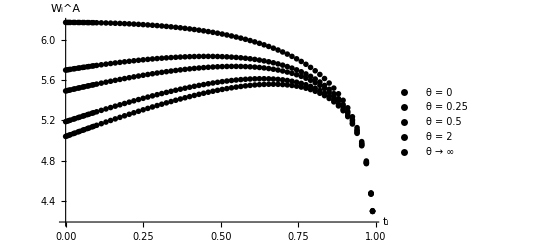

```mathematica
figure3=ListPlot[{s11111welAθ00i, s11111welAθ025i, s11111welAθ05i,s11111welAθ20i, s11111minIncreali}
, PlotLegends->Placed[PointLegend[{"θ = 0", "θ = 0.25","θ = 0.5", "θ = 2", "θ → ∞"}
,LegendFunction->Panel,LegendMargins->1],{0.7,0.325}]
, PlotRange->Full,AxesLabel->{"t_i","W_i^A"} ,AxesStyle->Directive[ Black]
,PlotMarkers->{"OpenMarkers",Tiny}
, MaxPlotPoints->75
,PlotStyle->Black
]
Export["UnilateralTax_Figure_3.pdf",figure3];
```

### Table 1: Optimal tax rates (t_i^opt) for different values of inequality aversion across scenarios

```mathematica
Grid[s11111topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s21111topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s12111topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
```

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.05
t_i^opt|θ=0.25 | 0.455
t_i^opt|θ=0.5 | 0.545
t_i^opt|θ=1.0 | 0.6
t_i^opt|θ=1.5 | 0.62
t_i^opt|θ=2.0 | 0.63
t_i^opt|θ→∞ | 0.665
t_i^opt|Sen | 0.665

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.05
t_i^opt|θ=0.25 | 0.445
t_i^opt|θ=0.5 | 0.535
t_i^opt|θ=1.0 | 0.59
t_i^opt|θ=1.5 | 0.61
t_i^opt|θ=2.0 | 0.62
t_i^opt|θ→∞ | 0.655
t_i^opt|Sen | 0.655

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.04
t_i^opt|θ=0.25 | 0.405
t_i^opt|θ=0.5 | 0.5
t_i^opt|θ=1.0 | 0.565
t_i^opt|θ=1.5 | 0.59
t_i^opt|θ=2.0 | 0.605
t_i^opt|θ→∞ | 0.655
t_i^opt|Sen | 0.65

### Table A.1: Optimal tax rates (t_i^opt) for different values of inequality aversion and parameter choices

```mathematica
Grid[s11111topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s11113topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s11112topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s11211topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s11311topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s11111dtopti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s11111btopti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
```

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.05
t_i^opt|θ=0.25 | 0.455
t_i^opt|θ=0.5 | 0.545
t_i^opt|θ=1.0 | 0.6
t_i^opt|θ=1.5 | 0.62
t_i^opt|θ=2.0 | 0.63
t_i^opt|θ→∞ | 0.665
t_i^opt|Sen | 0.665

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.25 | 0.455
t_i^opt|θ=0.5 | 0.545
t_i^opt|θ=1.0 | 0.6
t_i^opt|θ=1.5 | 0.62
t_i^opt|θ=2.0 | 0.63
t_i^opt|θ→∞ | 0.665
t_i^opt|Sen | 0.665

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.05
t_i^opt|θ=0.25 | 0.455
t_i^opt|θ=0.5 | 0.545
t_i^opt|θ=1.0 | 0.6
t_i^opt|θ=1.5 | 0.62
t_i^opt|θ=2.0 | 0.63
t_i^opt|θ→∞ | 0.665
t_i^opt|Sen | 0.665

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.005
t_i^opt|θ=0.25 | 0.07
t_i^opt|θ=0.5 | 0.12
t_i^opt|θ=1.0 | 0.175
t_i^opt|θ=1.5 | 0.205
t_i^opt|θ=2.0 | 0.225
t_i^opt|θ→∞ | 0.33
t_i^opt|Sen | 0.315

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.
t_i^opt|θ=0.25 | 0.
t_i^opt|θ=0.5 | 0.005
t_i^opt|θ=1.0 | 0.005
t_i^opt|θ=1.5 | 0.005
t_i^opt|θ=2.0 | 0.01
t_i^opt|θ→∞ | 0.07
t_i^opt|Sen | 0.055

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.25 | 0.185
t_i^opt|θ=0.5 | 0.265
t_i^opt|θ=1.0 | 0.34
t_i^opt|θ=1.5 | 0.375
t_i^opt|θ=2.0 | 0.395
t_i^opt|θ→∞ | 0.465
t_i^opt|Sen | 0.455

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.
t_i^opt|θ=0.25 | 0.035
t_i^opt|θ=0.5 | 0.065
t_i^opt|θ=1.0 | 0.1
t_i^opt|θ=1.5 | 0.125
t_i^opt|θ=2.0 | 0.14
t_i^opt|θ→∞ | 0.23
t_i^opt|Sen | 0.205

### Table A.2: Optimal tax rates (t_i^opt) for different values of inequality aversion and parameter choices across scenarios

```mathematica
Grid[s11111topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s11211topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s11111btopti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s21111topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s21211topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s21111btopti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s12111topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s12211topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s12111btopti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
```

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.05
t_i^opt|θ=0.25 | 0.455
t_i^opt|θ=0.5 | 0.545
t_i^opt|θ=1.0 | 0.6
t_i^opt|θ=1.5 | 0.62
t_i^opt|θ=2.0 | 0.63
t_i^opt|θ→∞ | 0.665
t_i^opt|Sen | 0.665

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.005
t_i^opt|θ=0.25 | 0.07
t_i^opt|θ=0.5 | 0.12
t_i^opt|θ=1.0 | 0.175
t_i^opt|θ=1.5 | 0.205
t_i^opt|θ=2.0 | 0.225
t_i^opt|θ→∞ | 0.33
t_i^opt|Sen | 0.315

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.
t_i^opt|θ=0.25 | 0.035
t_i^opt|θ=0.5 | 0.065
t_i^opt|θ=1.0 | 0.1
t_i^opt|θ=1.5 | 0.125
t_i^opt|θ=2.0 | 0.14
t_i^opt|θ→∞ | 0.23
t_i^opt|Sen | 0.205

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.05
t_i^opt|θ=0.25 | 0.445
t_i^opt|θ=0.5 | 0.535
t_i^opt|θ=1.0 | 0.59
t_i^opt|θ=1.5 | 0.61
t_i^opt|θ=2.0 | 0.62
t_i^opt|θ→∞ | 0.655
t_i^opt|Sen | 0.655

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.25 | 0.07
t_i^opt|θ=0.5 | 0.12
t_i^opt|θ=1.0 | 0.175
t_i^opt|θ=1.5 | 0.205
t_i^opt|θ=2.0 | 0.225
t_i^opt|θ→∞ | 0.33
t_i^opt|Sen | 0.315

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.25 | 0.035
t_i^opt|θ=0.5 | 0.06
t_i^opt|θ=1.0 | 0.1
t_i^opt|θ=1.5 | 0.12
t_i^opt|θ=2.0 | 0.14
t_i^opt|θ→∞ | 0.225
t_i^opt|Sen | 0.2

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.04
t_i^opt|θ=0.25 | 0.405
t_i^opt|θ=0.5 | 0.5
t_i^opt|θ=1.0 | 0.565
t_i^opt|θ=1.5 | 0.59
t_i^opt|θ=2.0 | 0.605
t_i^opt|θ→∞ | 0.655
t_i^opt|Sen | 0.65

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.25 | 0.055
t_i^opt|θ=0.5 | 0.095
t_i^opt|θ=1.0 | 0.145
t_i^opt|θ=1.5 | 0.18
t_i^opt|θ=2.0 | 0.2
t_i^opt|θ→∞ | 0.33
t_i^opt|Sen | 0.305

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.25 | 0.02
t_i^opt|θ=0.5 | 0.04
t_i^opt|θ=1.0 | 0.065
t_i^opt|θ=1.5 | 0.09
t_i^opt|θ=2.0 | 0.105
t_i^opt|θ→∞ | 0.225
t_i^opt|Sen | 0.18

## S.2 “Trade imbalances”

### Table S.1: Trade imbalances: Effects on firm selection and the wage

```mathematica
tableNumSimTIB={{"t_i","",{Part[s11111massLi,1]}[[1,1]],{Part[s11111massLi,21]}[[1,1]],{Part[s11111massLi,41]}[[1,1]],{Part[s11111massLi,61]}[[1,1]],{Part[s11111massLi,81]}[[1,1]],{Part[s11111massLi,101]}[[1,1]],{Part[s11111massLi,121]}[[1,1]],{Part[s11111massLi,141]}[[1,1]],{Part[s11111massLi,161]}[[1,1]],{Part[s11111massLi,181]}[[1,1]]}};
AppendTo[tableNumSimTIB,{"φ_i^i","T=0",N[Round[1000*{Part[s11111ϕii,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕii,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕii,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕii,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111ϕii,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕii,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕii,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕii,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕii,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕii,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_i^i","T=5",N[Round[1000*{Part[s11111TIBpϕii,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕii,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕii,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕii,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBpϕii,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕii,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕii,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕii,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕii,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕii,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_i^i","T=-5",N[Round[1000*{Part[s11111TIBnϕii,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕii,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕii,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕii,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBnϕii,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕii,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕii,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕii,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕii,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕii,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_i^j","T=0",N[Round[1000*{Part[s11111ϕij,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕij,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕij,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕij,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111ϕij,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕij,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕij,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕij,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕij,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕij,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_i^j","T=5",N[Round[1000*{Part[s11111TIBpϕij,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕij,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕij,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕij,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBpϕij,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕij,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕij,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕij,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕij,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕij,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_i^j","T=-5",N[Round[1000*{Part[s11111TIBnϕij,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕij,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕij,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕij,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBnϕij,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕij,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕij,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕij,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕij,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕij,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"χ_i","T=0",N[Round[1000*{Part[s11111χi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111χi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"χ_i","T=5",N[Round[1000*{Part[s11111TIBpχi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBpχi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"χ_i","T=-5",N[Round[1000*{Part[s11111TIBnχi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBnχi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_j^j","T=0",N[Round[1000*{Part[s11111ϕjj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕjj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕjj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕjj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111ϕjj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕjj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕjj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕjj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕjj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕjj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_j^j","T=5",N[Round[1000*{Part[s11111TIBpϕjj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕjj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕjj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕjj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBpϕjj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕjj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕjj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕjj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕjj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕjj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_j^j","T=-5",N[Round[1000*{Part[s11111TIBnϕjj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕjj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕjj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕjj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBnϕjj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕjj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕjj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕjj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕjj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕjj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_j^i","T=0",N[Round[1000*{Part[s11111ϕji,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕji,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕji,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕji,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111ϕji,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕji,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕji,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕji,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕji,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕji,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_j^i","T=5",N[Round[1000*{Part[s11111TIBpϕji,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕji,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕji,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕji,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBpϕji,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕji,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕji,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕji,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕji,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕji,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_j^i","T=-5",N[Round[1000*{Part[s11111TIBnϕji,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕji,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕji,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕji,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBnϕji,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕji,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕji,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕji,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕji,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕji,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"χ_j","T=0",N[Round[1000*{Part[s11111χj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111χj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"χ_j","T=5",N[Round[1000*{Part[s11111TIBpχj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBpχj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"χ_j","T=-5",N[Round[1000*{Part[s11111TIBnχj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBnχj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"w_i","T=0",N[Round[1000*{Part[s11111wi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111wi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111wi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111wi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111wi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111wi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111wi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111wi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111wi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111wi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"w_i","T=5",N[Round[1000*{Part[s11111TIBpwi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpwi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpwi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpwi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBpwi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpwi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpwi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpwi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpwi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpwi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"w_i","T=-5",N[Round[1000*{Part[s11111TIBnwi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnwi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnwi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnwi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBnwi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnwi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnwi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnwi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnwi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnwi,181]}[[1,2]]]/1000,3]}];
tableNumSimTIB
```

{{t_i,,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},{φ_i^i,T=0,1.98,2.03,2.08,2.15,2.23,2.33,2.45,2.63,2.91,3.46},{φ_i^i,T=5,1.99,2.04,2.1,2.17,2.25,2.35,2.48,2.66,2.94,3.5},{φ_i^i,T=-5,1.96,2.01,2.07,2.13,2.21,2.31,2.44,2.61,2.89,3.43},{φ_i^j,T=0,2.37,2.43,2.5,2.58,2.67,2.78,2.93,3.14,3.45,4.07},{φ_i^j,T=5,2.34,2.39,2.46,2.53,2.63,2.74,2.89,3.09,3.4,4.},{φ_i^j,T=-5,2.41,2.47,2.54,2.62,2.71,2.83,2.98,3.19,3.51,4.14},{χ_i,T=0,0.482,0.482,0.483,0.484,0.485,0.487,0.491,0.497,0.506,0.524},{χ_i,T=5,0.531,0.531,0.532,0.533,0.535,0.538,0.542,0.548,0.559,0.581},{χ_i,T=-5,0.438,0.438,0.438,0.439,0.44,0.442,0.445,0.45,0.458,0.473},{φ_j^j,T=0,2.03,2.03,2.03,2.03,2.03,2.02,2.02,2.02,2.02,2.01},{φ_j^j,T=5,2.01,2.01,2.01,2.01,2.01,2.01,2.01,2.01,2.,2.},{φ_j^j,T=-5,2.04,2.04,2.04,2.04,2.04,2.04,2.04,2.04,2.04,2.03},{φ_j^i,T=0,2.43,2.43,2.43,2.43,2.43,2.44,2.44,2.44,2.45,2.47},{φ_j^i,T=5,2.47,2.47,2.47,2.47,2.48,2.48,2.48,2.49,2.49,2.51},{φ_j^i,T=-5,2.39,2.39,2.39,2.39,2.4,2.4,2.4,2.4,2.41,2.42},{χ_j,T=0,0.482,0.482,0.482,0.481,0.479,0.477,0.474,0.468,0.46,0.444},{χ_j,T=5,0.438,0.438,0.437,0.436,0.435,0.433,0.429,0.424,0.416,0.4},{χ_j,T=-5,0.531,0.531,0.531,0.53,0.528,0.526,0.522,0.517,0.508,0.491},{w_i,T=0,1.01,1.,0.989,0.977,0.963,0.947,0.928,0.905,0.874,0.824},{w_i,T=5,1.,0.994,0.983,0.971,0.957,0.941,0.922,0.899,0.868,0.818},{w_i,T=-5,1.02,1.01,0.995,0.983,0.969,0.953,0.934,0.911,0.879,0.829}}

## S.3 “Numerical simulation in levels”

### Figure S.1: Numerical simulation of Proposition 1, part 1

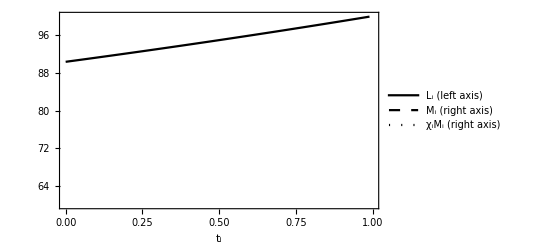
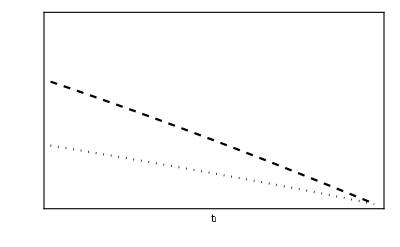

```mathematica
figureS1a1=ListLinePlot[{s11111massLi,empty,empty}
,PlotStyle->{{Black},{Black,Dashed},{Black,Dotted}}
, PlotLegends->Placed[PointLegend[{Style["L_i (left axis)",FontSize->12],Style["M_i (right axis)",FontSize->12], Style["χ_iM_i (right axis)",FontSize->12]}
,LegendFunction->Panel,LegendMargins->1],
Right
]
,AxesStyle->Directive[ Black]
,Frame->{{True,False},{True,False}}
,FrameLabel->{Style["t_i",FontSize->10]}
,PlotStyle->{{Black}}
,ImagePadding->35
,PlotStyle->Black
,PlotRange->{{0,1},{60,100}}];
figureS1a2=ListLinePlot[{s11111massMi,s11111massMij}
,AxesLabel->{Style["t_i",FontSize->10]}
,AxesStyle->Directive[ Black]
,Frame->{{False,True},{True,False}}
,PlotStyle->{{Black,Dashed},{Black,Dotted}}
,PlotStyle->Black
,ImagePadding->35
, FrameTicks->{{None,All},{None,None}}
,PlotRange->{{0,1},{0,10}}];
figureS1a=Overlay[{figureS1a1,figureS1a2}]
Export["UnilateralTax_Figure_S1a.pdf",figureS1a];
```

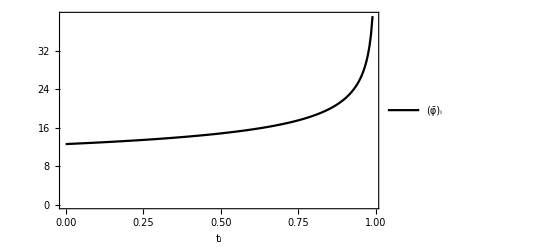

```mathematica
figureS1b=ListLinePlot[{s11111avgϕi}
,AxesLabel->{Style["t_i",FontSize->10]}
,PlotStyle->{{Black},{Black,Dashed},{Black,Dotted}}
, PlotLegends->Placed[PointLegend[{Style[Subscript[OverBar[φ], i],FontSize->12]}
,LegendFunction->Panel,LegendMargins->1],
Right
]
,AxesStyle->Directive[ Black]
,Frame->{{True,False},{True,False}}
,PlotStyle->{{Black}}
,ImagePadding->35
,FrameLabel->{Style["t_i",FontSize->10]}
,PlotStyle->Black
,PlotRange->Full]
Export["UnilateralTax_Figure_S1b.pdf",figureS1b];
```

### Figure S.2: Numerical simulation of Proposition 1, part 2

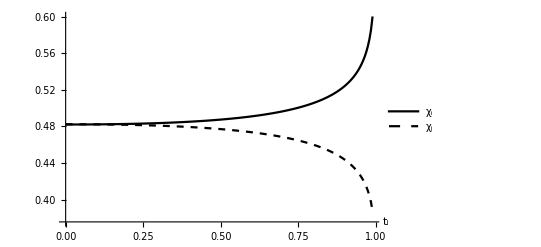

```mathematica
figureS2=
ListLinePlot[{s11111χi,s11111χj}
, PlotLegends->Placed[PointLegend[{Style["χ_i",FontSize->12],Style["χ_j",FontSize->12]}
,LegendFunction->Panel,LegendMargins->1],
Right
]
,AxesLabel->{Style["t_i",FontSize->10]}
,AxesStyle->Directive[ Black]
,PlotStyle->{{Black},{Black,Dashed},{Black,Dotted}}
,PlotStyle->Black
, PlotRange->Full]
Export["UnilateralTax_Figure_S2.pdf",figureS2];
```

### Figure S.3: Numerical simulation of Proposition 1, part 3

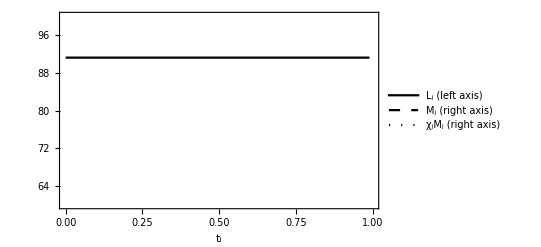
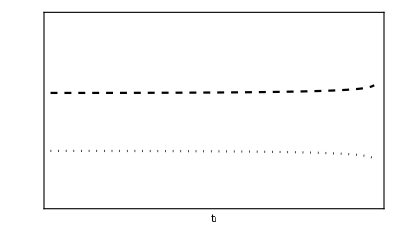

```mathematica
figureS3a1=
ListLinePlot[{s11111massLj,empty,empty}
,PlotStyle->{{Black},{Black,Dashed},{Black,Dotted}}
, PlotLegends->Placed[PointLegend[{Style["L_j (left axis)",FontSize->12],Style["M_j (right axis)",FontSize->12], Style["χ_jM_j (right axis)",FontSize->12]}
,LegendFunction->Panel,LegendMargins->1],
Right
]
,AxesStyle->Directive[ Black]
,Frame->{{True,False},{True,False}}
,FrameLabel->{Style["t_i",FontSize->10]}
,PlotStyle->{{Black}}
,ImagePadding->35
,PlotStyle->Black
,PlotRange->{{0,1},{60,100}}];
figureS3a2=ListLinePlot[{s11111massMj,s11111massMji}
,AxesLabel->{Style["t_i",FontSize->10]}
,AxesStyle->Directive[ Black]
,Frame->{{False,True},{True,False}}
,PlotStyle->{{Black,Dashed},{Black,Dotted}}
,PlotStyle->Black
,ImagePadding->35
, FrameTicks->{{None,All},{None,None}}
,PlotRange->{{0,1},{0,10}}];
figureS3a=Overlay[{figureS3a1,figureS3a2}]
Export["UnilateralTax_Figure_S3a.pdf",figureS3a];
```

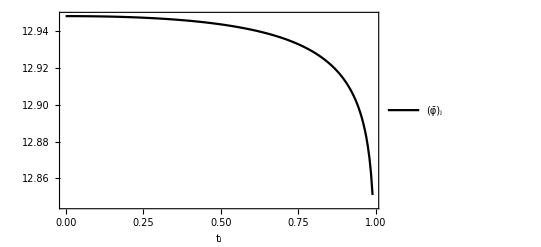

```mathematica
figureS3b=
ListLinePlot[{s11111avgϕj}
,AxesLabel->{Style["t_i",FontSize->10]}
,PlotStyle->{{Black},{Black,Dashed},{Black,Dotted}}
, PlotLegends->Placed[PointLegend[{Style[Subscript[OverBar[φ], j],FontSize->12]}
,LegendFunction->Panel,LegendMargins->1],
Right
]
,AxesStyle->Directive[ Black]
,Frame->{{True,False},{True,False}}
,PlotStyle->{{Black}}
,ImagePadding->35
,FrameLabel->{Style["t_i",FontSize->10]}
,PlotStyle->Black
,PlotRange->Full]
Export["UnilateralTax_Figure_S3b.pdf",figureS3b];
```

### Figure S.4: Numerical simulation of Proposition 2

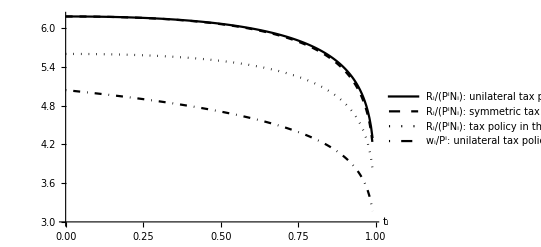

```mathematica
s11111realwi=Transpose@{Part[s11111wi][[;;,1]],Part[s11111wi][[;;,2]]/Part[s11111indexPi][[;;,2]]};
figureS4=
ListLinePlot[{s11111welAθ00i,s21111welAθ00i,s12111welAθ00i,s11111realwi}
, PlotLegends->Placed[PointLegend[{Style["R_i/(P^iN_i): unilateral tax policy in the open economy",FontSize->12],Style["R_i/(P^iN_i): symmetric tax policy in the open economy",FontSize->12],Style["R_i/(P^iN_i): tax policy in the closed economy",FontSize->12],Style["w_i/P^i: unilateral tax policy in the open economy",FontSize->12]}
,LegendFunction->Panel,LegendMargins->1],
Right
]
,AxesLabel->{Style["t_i",FontSize->10]}
,AxesStyle->Directive[ Black]
,PlotStyle->{{Black},{Black,Dashed},{Black,Dotted},{Black,DotDashed}}
,PlotStyle->Black
, PlotRange->Full]
Export["UnilateralTax_Figure_S4.pdf",figureS4];
```

### Figure S.5: Numerical simulation of Proposition 3

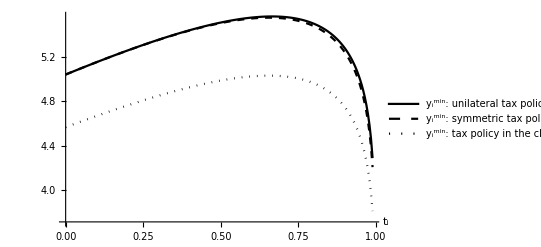

```mathematica
figureS5=
ListLinePlot[{s11111minIncreali,s21111minIncreali,s12111minIncreali}
, PlotLegends->Placed[PointLegend[{Style["y_i^min: unilateral tax policy in the open economy",FontSize->12],Style["y_i^min: symmetric tax policy in the open economy",FontSize->12],Style["y_i^min: tax policy in the closed economy",FontSize->12]}
,LegendFunction->Panel,LegendMargins->1],
Right
]
,AxesLabel->{Style["t_i",FontSize->10]}
,AxesStyle->Directive[ Black]
,PlotStyle->{{Black},{Black,Dashed},{Black,Dotted},{Black,DotDashed}}
,PlotStyle->Black
, PlotRange->Full]
Export["UnilateralTax_Figure_S5.pdf",figureS5];
```

### Figure S.6: Numerical simulation of Proposition 4

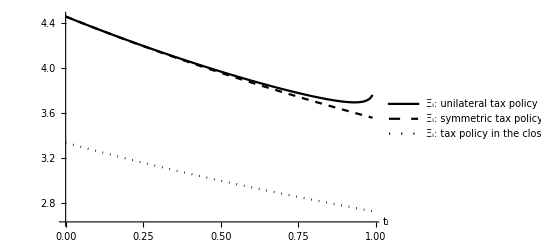

```mathematica
figureS6=
ListLinePlot[{s11111Ξi,s21111Ξi,s12111Ξi}
, PlotLegends->Placed[PointLegend[{Style["Ξ_i: unilateral tax policy in the open economy",FontSize->12],Style["Ξ_i: symmetric tax policy in the open economy",FontSize->12],Style["Ξ_i: tax policy in the closed economy",FontSize->12]}
,LegendFunction->Panel,LegendMargins->1],
Right
]
,AxesLabel->{Style["t_i",FontSize->10]}
,AxesStyle->Directive[ Black]
,PlotStyle->{{Black},{Black,Dashed},{Black,Dotted},{Black,DotDashed}}
,PlotStyle->Black
, PlotRange->Full]
Export["UnilateralTax_Figure_S6.pdf",figureS6];
```

### Figure S.7: Numerical simulation of Proposition 5

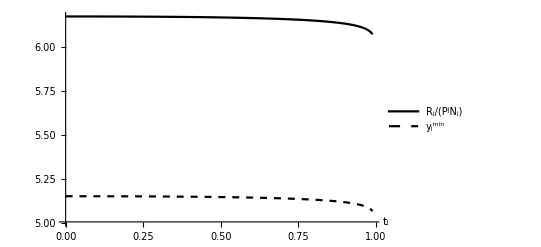

```mathematica
figureS7a=
ListLinePlot[{s11111welAθ00j,s11111minIncrealj}
, PlotLegends->Placed[PointLegend[{Style["R_j/(P^jN_j)",FontSize->12],Style["y_j^min",FontSize->12]}
,LegendFunction->Panel,LegendMargins->1],
Right
]
,AxesLabel->{Style["t_i",FontSize->10]}
,AxesStyle->Directive[ Black]
,PlotStyle->{{Black},{Black,Dashed},{Black,Dotted},{Black,DotDashed}}
,PlotStyle->Black
, PlotRange->Full
]
Export["UnilateralTax_Figure_S7a.pdf",figureS7a];
```

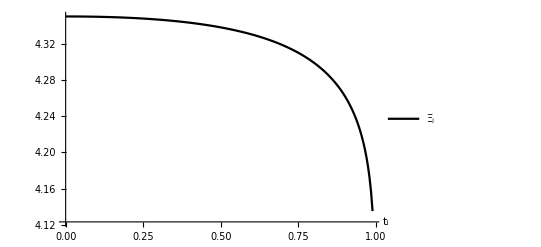

```mathematica
figureS7b=
ListLinePlot[{s11111Ξj}
, PlotLegends->Placed[PointLegend[{Style["Ξ_j",FontSize->12]}
,LegendFunction->Panel,LegendMargins->1],
Right
]
,AxesLabel->{Style["t_i",FontSize->10]}
,AxesStyle->Directive[ Black]
,PlotStyle->{{Black},{Black,Dashed},{Black,Dotted},{Black,DotDashed}}
,PlotStyle->Black
, PlotRange->Full]
Export["UnilateralTax_Figure_S7b.pdf",figureS7b];
```

### Table S.2: Variation in k: Effects on the factor allocation and the terms of trade

```mathematica
tableNumSimk={{"t_i","",{Part[s11111massLi,1]}[[1,1]],{Part[s11111massLi,21]}[[1,1]],{Part[s11111massLi,41]}[[1,1]],{Part[s11111massLi,61]}[[1,1]],{Part[s11111massLi,81]}[[1,1]],{Part[s11111massLi,101]}[[1,1]],{Part[s11111massLi,121]}[[1,1]],{Part[s11111massLi,141]}[[1,1]],{Part[s11111massLi,161]}[[1,1]],{Part[s11111massLi,181]}[[1,1]]}};
AppendTo[tableNumSimk,{"L_i","k=4",N[Round[10*{Part[s11111massLi,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimk,{"L_i","k=8",N[Round[10*{Part[s11211massLi,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLi,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLi,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLi,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLi,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLi,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLi,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLi,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLi,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLi,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimk,{"M_i","k=4",N[Round[10*{Part[s11111massMi,1]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,21]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,41]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,61]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,161]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,181]}[[1,2]]]/10,1]}];
AppendTo[tableNumSimk,{"M_i","k=8",N[Round[10*{Part[s11211massMi,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMi,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMi,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMi,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMi,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMi,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMi,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMi,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMi,161]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMi,181]}[[1,2]]]/10,2]}];
AppendTo[tableNumSimk,{"χ_iM_i","k=4",N[Round[10*{Part[s11111massMij,1]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,21]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,41]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,61]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,161]}[[1,2]]]/10,1],N[Round[10*{Part[s11111massMij,181]}[[1,2]]]/10,1]}];
AppendTo[tableNumSimk,{"χ_iM_i","k=8",N[Round[10*{Part[s11211massMij,1]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMij,21]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMij,41]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMij,61]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMij,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMij,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMij,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMij,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMij,161]}[[1,2]]]/10,1],N[Round[10*{Part[s11211massMij,181]}[[1,2]]]/10,1]}];
AppendTo[tableNumSimk,{"OverBar[φ]_i","k=4",N[Round[10*{Part[s11111avgϕi,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimk,{"OverBar[φ]_i","k=8",N[Round[100*{Part[s11211avgϕi,1]}[[1,2]]]/100,2],N[Round[100*{Part[s11211avgϕi,21]}[[1,2]]]/100,2],N[Round[100*{Part[s11211avgϕi,41]}[[1,2]]]/100,2],N[Round[100*{Part[s11211avgϕi,61]}[[1,2]]]/100,2],N[Round[100*{Part[s11211avgϕi,81]}[[1,2]]]/100,2],N[Round[100*{Part[s11211avgϕi,101]}[[1,2]]]/100,2],N[Round[100*{Part[s11211avgϕi,121]}[[1,2]]]/100,2],N[Round[100*{Part[s11211avgϕi,141]}[[1,2]]]/100,2],N[Round[100*{Part[s11211avgϕi,161]}[[1,2]]]/100,2],N[Round[100*{Part[s11211avgϕi,181]}[[1,2]]]/100,2]}];
AppendTo[tableNumSimk,{"χ_i","k=4",N[Round[1000*{Part[s11111χi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111χi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimk,{"χ_i","k=8",N[Round[1000*{Part[s11211χi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11211χi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimk,{"P_i^j/P_j^i","k=4",N[Round[100000*{Part[s11111toti,1]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,21]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,41]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,61]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,81]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,101]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,121]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,141]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,161]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,181]}[[1,2]]]/100000,4]}];
AppendTo[tableNumSimk,{"P_i^j/P_j^i","k=8",N[Round[100000*{Part[s11211toti,1]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11211toti,21]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11211toti,41]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11211toti,61]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11211toti,81]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11211toti,101]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11211toti,121]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11211toti,141]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11211toti,161]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11211toti,181]}[[1,2]]]/100000,4]}];
AppendTo[tableNumSimk,{"χ_j","k=4",N[Round[1000*{Part[s11111χj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111χj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimk,{"χ_j","k=8",N[Round[1000*{Part[s11211χj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11211χj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimk,{"L_j","k=4",N[Round[10*{Part[s11111massLj,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimk,{"L_j","k=8",N[Round[10*{Part[s11211massLj,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLj,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLj,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLj,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLj,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLj,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLj,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLj,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLj,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLj,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimk,{"M_j","k=4",N[Round[10*{Part[s11111massMj,1]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,21]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,41]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,61]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,161]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,181]}[[1,2]]]/10,2]}];
AppendTo[tableNumSimk,{"M_j","k=8",N[Round[10*{Part[s11211massMj,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMj,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMj,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMj,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMj,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMj,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMj,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMj,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMj,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMj,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimk,{"χ_jM_j","k=4",N[Round[10*{Part[s11111massMji,1]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,21]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,41]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,61]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,161]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,181]}[[1,2]]]/10,2]}];
AppendTo[tableNumSimk,{"χ_jM_j","k=8",N[Round[10*{Part[s11211massMji,1]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMji,21]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMji,41]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMji,61]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMji,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMji,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMji,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMji,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMji,161]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMji,181]}[[1,2]]]/10,2]}];
AppendTo[tableNumSimk,{"OverBar[φ]_j","k=4",N[Round[100*{Part[s11111avgϕj,1]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,21]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,41]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,61]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,81]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,101]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,121]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,141]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,161]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,181]}[[1,2]]]/100,4]}];
AppendTo[tableNumSimk,{"OverBar[φ]_j","k=8",N[Round[1000*{Part[s11211avgϕj,1]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11211avgϕj,21]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11211avgϕj,41]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11211avgϕj,61]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11211avgϕj,81]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11211avgϕj,101]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11211avgϕj,121]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11211avgϕj,141]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11211avgϕj,161]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11211avgϕj,181]}[[1,2]]]/1000,4]}];
tableNumSimk
```

{{t_i,,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},{L_i,k=4,90.3,91.2,92.1,93.,94.,94.9,95.9,96.9,97.9,98.9},{L_i,k=8,81.2,82.7,84.3,86.,87.8,89.6,91.5,93.5,95.6,97.7},{M_i,k=4,6.5,5.9,5.3,4.7,4.1,3.4,2.8,2.1,1.4,0.7},{M_i,k=8,15.3,14.,12.7,11.3,9.9,8.4,6.9,5.2,3.5,1.8},{χ_iM_i,k=4,3.1,2.9,2.6,2.3,2.,1.7,1.4,1.,0.7,0.4},{χ_iM_i,k=8,3.6,3.3,3.,2.6,2.3,2.,1.6,1.3,0.9,0.5},{OverBar[φ]_i,k=4,12.6,12.9,13.3,13.7,14.2,14.9,15.7,16.8,18.6,22.},{OverBar[φ]_i,k=8,1.6,1.6,1.7,1.7,1.7,1.8,1.8,1.9,2.,2.1},{χ_i,k=4,0.482,0.482,0.483,0.484,0.485,0.487,0.491,0.497,0.506,0.524},{χ_i,k=8,0.232,0.233,0.233,0.234,0.235,0.237,0.24,0.244,0.252,0.268},{P_i^j/P_j^i,k=4,0.9999,1.,1.,1.001,1.002,1.003,1.005,1.007,1.012,1.021},{P_i^j/P_j^i,k=8,0.9999,1.,1.,1.001,1.001,1.002,1.004,1.006,1.01,1.018},{χ_j,k=4,0.482,0.482,0.482,0.481,0.479,0.477,0.474,0.468,0.46,0.444},{χ_j,k=8,0.233,0.233,0.232,0.231,0.23,0.228,0.226,0.221,0.215,0.201},{L_j,k=4,91.2,91.2,91.2,91.2,91.2,91.2,91.2,91.2,91.2,91.2},{L_j,k=8,82.7,82.7,82.7,82.7,82.7,82.7,82.7,82.7,82.7,82.7},{M_j,k=4,5.9,5.9,5.9,5.9,5.9,6.,6.,6.,6.,6.1},{M_j,k=8,14.,14.,14.,14.,14.,14.1,14.1,14.1,14.2,14.4},{χ_jM_j,k=4,2.9,2.9,2.9,2.9,2.8,2.8,2.8,2.8,2.8,2.7},{χ_jM_j,k=8,3.3,3.3,3.3,3.2,3.2,3.2,3.2,3.1,3.1,2.9},{OverBar[φ]_j,k=4,12.95,12.95,12.95,12.95,12.95,12.94,12.94,12.94,12.93,12.91},{OverBar[φ]_j,k=8,1.642,1.642,1.642,1.642,1.642,1.642,1.641,1.64,1.639,1.636}}

### Table S.3: Variation in k: Effects on real income and inequality

```mathematica
tableNumSimk2={{"t_i","",{Part[s11111massLi,1]}[[1,1]],{Part[s11111massLi,21]}[[1,1]],{Part[s11111massLi,41]}[[1,1]],{Part[s11111massLi,61]}[[1,1]],{Part[s11111massLi,81]}[[1,1]],{Part[s11111massLi,101]}[[1,1]],{Part[s11111massLi,121]}[[1,1]],{Part[s11111massLi,141]}[[1,1]],{Part[s11111massLi,161]}[[1,1]],{Part[s11111massLi,181]}[[1,1]]}};
AppendTo[tableNumSimk2,{"R_i/(P_iN_i)","k=4",N[Round[100*{Part[s11111welAθ00i,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"R_i/(P_iN_i)","k=8",N[Round[100*{Part[s11211welAθ00i,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00i,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00i,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00i,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00i,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00i,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00i,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00i,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00i,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00i,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"y_i^min","k=4",N[Round[100*{Part[s11111minIncreali,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"y_i^min","k=8",N[Round[100*{Part[s11211minIncreali,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncreali,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncreali,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncreali,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncreali,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncreali,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncreali,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncreali,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncreali,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncreali,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"Ξ_i","k=4",N[Round[100*{Part[s11111Ξi,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"Ξ_i","k=8",N[Round[100*{Part[s11211Ξi,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξi,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξi,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξi,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξi,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξi,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξi,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξi,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξi,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξi,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"R_j/(P_jN_j)","k=4",N[Round[100*{Part[s11111welAθ00j,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"R_j/(P_jN_j)","k=8",N[Round[100*{Part[s11211welAθ00j,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00j,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00j,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00j,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00j,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00j,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00j,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00j,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00j,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00j,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"y_j^min","k=4",N[Round[100*{Part[s11111minIncrealj,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"y_j^min","k=8",N[Round[100*{Part[s11211minIncrealj,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncrealj,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncrealj,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncrealj,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncrealj,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncrealj,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncrealj,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncrealj,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncrealj,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncrealj,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"Ξ_j","k=4",N[Round[100*{Part[s11111Ξj,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"Ξ_j","k=8",N[Round[100*{Part[s11211Ξj,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξj,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξj,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξj,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξj,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξj,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξj,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξj,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξj,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξj,181]}[[1,2]]]/100,3]}];
tableNumSimk2
```

{{t_i,,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},{R_i/(P_iN_i),k=4,6.18,6.18,6.17,6.15,6.11,6.07,5.99,5.88,5.71,5.38},{R_i/(P_iN_i),k=8,3.42,3.41,3.4,3.38,3.34,3.29,3.2,3.08,2.88,2.53},{y_i^min,k=4,5.04,5.15,5.26,5.35,5.44,5.51,5.55,5.56,5.5,5.28},{y_i^min,k=8,3.1,3.13,3.15,3.16,3.16,3.14,3.09,2.99,2.83,2.5},{Ξ_i,k=4,4.46,4.35,4.25,4.15,4.06,3.97,3.89,3.81,3.75,3.7},{Ξ_i,k=8,1.66,1.64,1.63,1.61,1.59,1.57,1.56,1.54,1.53,1.52},{R_j/(P_jN_j),k=4,6.18,6.18,6.17,6.17,6.17,6.17,6.17,6.16,6.15,6.13},{R_j/(P_jN_j),k=8,3.41,3.41,3.41,3.41,3.41,3.41,3.41,3.41,3.41,3.4},{y_j^min,k=4,5.15,5.15,5.15,5.15,5.15,5.15,5.14,5.14,5.13,5.12},{y_j^min,k=8,3.13,3.13,3.13,3.13,3.13,3.13,3.13,3.13,3.12,3.12},{Ξ_j,k=4,4.35,4.35,4.35,4.35,4.34,4.34,4.33,4.32,4.3,4.26},{Ξ_j,k=8,1.64,1.64,1.64,1.64,1.64,1.64,1.64,1.64,1.64,1.63}}

### Table S.4: Variation in σ: Effects on the factor allocation and the terms of trade

```mathematica
tableNumSimσ={{"t_i","",{Part[s11111massLi,1]}[[1,1]],{Part[s11111massLi,21]}[[1,1]],{Part[s11111massLi,41]}[[1,1]],{Part[s11111massLi,61]}[[1,1]],{Part[s11111massLi,81]}[[1,1]],{Part[s11111massLi,101]}[[1,1]],{Part[s11111massLi,121]}[[1,1]],{Part[s11111massLi,141]}[[1,1]],{Part[s11111massLi,161]}[[1,1]],{Part[s11111massLi,181]}[[1,1]]}};
AppendTo[tableNumSimσ,{"L_i","σ=3.8",N[Round[10*{Part[s11111massLi,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimσ,{"L_i","σ=2",N[Round[10*{Part[s11111bmassLi,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassLi,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassLi,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassLi,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassLi,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassLi,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassLi,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassLi,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassLi,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassLi,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimσ,{"M_i","σ=3.8",N[Round[10*{Part[s11111massMi,1]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,21]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,41]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,61]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,161]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,181]}[[1,2]]]/10,1]}];
AppendTo[tableNumSimσ,{"M_i","σ=2",N[Round[100*{Part[s11111bmassMi,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMi,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMi,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMi,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMi,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMi,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMi,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMi,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMi,161]}[[1,2]]]/100,2],N[Round[100*{Part[s11111bmassMi,181]}[[1,2]]]/100,2]}];
AppendTo[tableNumSimσ,{"χ_iM_i","σ=3.8",N[Round[100*{Part[s11111massMij,1]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMij,21]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMij,41]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMij,61]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMij,81]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMij,101]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMij,121]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMij,141]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMij,161]}[[1,2]]]/100,1],N[Round[100*{Part[s11111massMij,181]}[[1,2]]]/100,1]}];
AppendTo[tableNumSimσ,{"χ_iM_i","σ=2",N[Round[100*{Part[s11111bmassMij,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMij,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMij,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMij,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMij,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMij,101]}[[1,2]]]/100,2],N[Round[100*{Part[s11111bmassMij,121]}[[1,2]]]/100,2],N[Round[100*{Part[s11111bmassMij,141]}[[1,2]]]/100,2],N[Round[100*{Part[s11111bmassMij,161]}[[1,2]]]/100,2],N[Round[100*{Part[s11111bmassMij,181]}[[1,2]]]/100,2]}];
AppendTo[tableNumSimσ,{"OverBar[φ]_i","σ=3.8",N[Round[10*{Part[s11111avgϕi,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimσ,{"OverBar[φ]_i","σ=2",N[Round[100*{Part[s11111bavgϕi,1]}[[1,2]]]/100,2],N[Round[100*{Part[s11111bavgϕi,21]}[[1,2]]]/100,2],N[Round[100*{Part[s11111bavgϕi,41]}[[1,2]]]/100,2],N[Round[100*{Part[s11111bavgϕi,61]}[[1,2]]]/100,2],N[Round[100*{Part[s11111bavgϕi,81]}[[1,2]]]/100,2],N[Round[100*{Part[s11111bavgϕi,101]}[[1,2]]]/100,2],N[Round[100*{Part[s11111bavgϕi,121]}[[1,2]]]/100,2],N[Round[100*{Part[s11111bavgϕi,141]}[[1,2]]]/100,2],N[Round[100*{Part[s11111bavgϕi,161]}[[1,2]]]/100,2],N[Round[100*{Part[s11111bavgϕi,181]}[[1,2]]]/100,2]}];
AppendTo[tableNumSimσ,{"χ_i","σ=3.8",N[Round[1000*{Part[s11111χi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111χi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimσ,{"χ_i","σ=2",N[Round[1000*{Part[s11111bχi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111bχi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111bχi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111bχi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111bχi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111bχi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111bχi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111bχi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111bχi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111bχi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimσ,{"P_i^j/P_j^i","σ=3.8",N[Round[100000*{Part[s11111toti,1]}[[1,2]]]/100000,5],N[Round[100000*{Part[s11111toti,21]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,41]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,61]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,81]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,101]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,121]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,141]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,161]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,181]}[[1,2]]]/100000,4]}];
AppendTo[tableNumSimσ,{"P_i^j/P_j^i","σ=2",N[Round[100000*{Part[s11111btoti,1]}[[1,2]]]/100000,5],N[Round[100000*{Part[s11111btoti,21]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111btoti,41]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111btoti,61]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111btoti,81]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111btoti,101]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111btoti,121]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111btoti,141]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111btoti,161]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111btoti,181]}[[1,2]]]/100000,4]}];
AppendTo[tableNumSimσ,{"χ_j","σ=3.8",N[Round[1000*{Part[s11111χj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111χj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimσ,{"χ_j","σ=2",N[Round[1000*{Part[s11111bχj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111bχj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111bχj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111bχj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111bχj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111bχj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111bχj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111bχj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111bχj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111bχj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimσ,{"L_j","σ=3.8",N[Round[10*{Part[s11111massLj,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimσ,{"L_j","σ=2",N[Round[10*{Part[s11111bmassLj,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassLj,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassLj,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassLj,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassLj,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassLj,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassLj,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassLj,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassLj,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassLj,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimσ,{"M_j","σ=3.8",N[Round[10*{Part[s11111massMj,1]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,21]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,41]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,61]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,161]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,181]}[[1,2]]]/10,2]}];
AppendTo[tableNumSimσ,{"M_j","σ=2",N[Round[10*{Part[s11111bmassMj,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassMj,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassMj,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassMj,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassMj,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassMj,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassMj,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassMj,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassMj,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11111bmassMj,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimσ,{"χ_jM_j","σ=3.8",N[Round[100*{Part[s11111massMji,1]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMji,21]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMji,41]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMji,61]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMji,81]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMji,101]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMji,121]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMji,141]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMji,161]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMji,181]}[[1,2]]]/100,2]}];
AppendTo[tableNumSimσ,{"χ_jM_j","σ=2",N[Round[100*{Part[s11111bmassMji,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMji,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMji,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMji,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMji,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMji,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMji,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMji,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMji,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bmassMji,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ,{"OverBar[φ]_j","σ=3.8",N[Round[100*{Part[s11111avgϕj,1]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,21]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,41]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,61]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,81]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,101]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,121]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,141]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,161]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,181]}[[1,2]]]/100,4]}];
AppendTo[tableNumSimσ,{"OverBar[φ]_j","σ=2",N[Round[1000*{Part[s11111bavgϕj,1]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11111bavgϕj,21]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11111bavgϕj,41]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11111bavgϕj,61]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11111bavgϕj,81]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11111bavgϕj,101]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11111bavgϕj,121]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11111bavgϕj,141]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11111bavgϕj,161]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11111bavgϕj,181]}[[1,2]]]/1000,4]}];
tableNumSimσ
```

{{t_i,,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},{L_i,σ=3.8,90.3,91.2,92.1,93.,94.,94.9,95.9,96.9,97.9,98.9},{L_i,σ=2,57.1,59.7,62.5,65.6,69.,72.7,76.9,81.6,87.,93.},{M_i,σ=3.8,6.5,5.9,5.3,4.7,4.1,3.4,2.8,2.1,1.4,0.7},{M_i,σ=2,28.9,27.2,25.3,23.2,20.8,18.2,15.3,12.,8.3,4.2},{χ_iM_i,σ=3.8,3.2,2.9,2.6,2.3,2.,1.7,1.4,1.,0.7,0.4},{χ_iM_i,σ=2,13.9,13.1,12.2,11.3,10.2,9.1,7.8,6.4,4.8,2.8},{OverBar[φ]_i,σ=3.8,12.6,12.9,13.3,13.7,14.2,14.9,15.7,16.8,18.6,22.},{OverBar[φ]_i,σ=2,2.2,2.2,2.3,2.3,2.4,2.4,2.6,2.7,3.,3.5},{χ_i,σ=3.8,0.482,0.482,0.483,0.484,0.485,0.487,0.491,0.497,0.506,0.524},{χ_i,σ=2,0.482,0.482,0.484,0.487,0.492,0.5,0.514,0.536,0.577,0.674},{P_i^j/P_j^i,σ=3.8,0.99993,1.,1.,1.001,1.002,1.003,1.005,1.007,1.012,1.021},{P_i^j/P_j^i,σ=2,0.99977,1.,1.001,1.002,1.005,1.009,1.016,1.027,1.046,1.087},{χ_j,σ=3.8,0.482,0.482,0.482,0.481,0.479,0.477,0.474,0.468,0.46,0.444},{χ_j,σ=2,0.483,0.482,0.481,0.478,0.473,0.465,0.453,0.434,0.403,0.345},{L_j,σ=3.8,91.2,91.2,91.2,91.2,91.2,91.2,91.2,91.2,91.2,91.2},{L_j,σ=2,59.7,59.7,59.7,59.7,59.7,59.7,59.7,59.7,59.7,59.7},{M_j,σ=3.8,5.9,5.9,5.9,5.9,5.9,6.,6.,6.,6.,6.1},{M_j,σ=2,27.2,27.2,27.2,27.3,27.4,27.5,27.7,28.1,28.7,30.},{χ_jM_j,σ=3.8,2.9,2.9,2.9,2.9,2.9,2.8,2.8,2.8,2.8,2.7},{χ_jM_j,σ=2,13.1,13.1,13.1,13.,12.9,12.8,12.6,12.2,11.6,10.3},{OverBar[φ]_j,σ=3.8,12.95,12.95,12.95,12.95,12.95,12.94,12.94,12.94,12.93,12.91},{OverBar[φ]_j,σ=2,2.213,2.212,2.212,2.212,2.211,2.21,2.208,2.205,2.199,2.186}}

### Table S.5: Variation in σ: Effects on real income and inequality

```mathematica
tableNumSimσ2={{"t_i","",{Part[s11111massLi,1]}[[1,1]],{Part[s11111massLi,21]}[[1,1]],{Part[s11111massLi,41]}[[1,1]],{Part[s11111massLi,61]}[[1,1]],{Part[s11111massLi,81]}[[1,1]],{Part[s11111massLi,101]}[[1,1]],{Part[s11111massLi,121]}[[1,1]],{Part[s11111massLi,141]}[[1,1]],{Part[s11111massLi,161]}[[1,1]],{Part[s11111massLi,181]}[[1,1]]}};
AppendTo[tableNumSimσ2,{"R_i/(P_iN_i)","σ=3.8",N[Round[100*{Part[s11111welAθ00i,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"R_i/(P_iN_i)","σ=2",N[Round[100*{Part[s11111bwelAθ00i,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bwelAθ00i,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bwelAθ00i,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bwelAθ00i,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bwelAθ00i,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bwelAθ00i,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bwelAθ00i,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bwelAθ00i,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bwelAθ00i,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bwelAθ00i,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"y_i^min","σ=3.8",N[Round[100*{Part[s11111minIncreali,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"y_i^min","σ=2",N[Round[100*{Part[s11111bminIncreali,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bminIncreali,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bminIncreali,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bminIncreali,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bminIncreali,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bminIncreali,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bminIncreali,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bminIncreali,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bminIncreali,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bminIncreali,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"Ξ_i","σ=3.8",N[Round[100*{Part[s11111Ξi,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"Ξ_i","σ=2",N[Round[100*{Part[s11111bΞi,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bΞi,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bΞi,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bΞi,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bΞi,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bΞi,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bΞi,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bΞi,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bΞi,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bΞi,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"R_j/(P_jN_j)","σ=3.8",N[Round[100*{Part[s11111welAθ00j,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"R_j/(P_jN_j)","σ=2",N[Round[100*{Part[s11111bwelAθ00j,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bwelAθ00j,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bwelAθ00j,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bwelAθ00j,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bwelAθ00j,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bwelAθ00j,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bwelAθ00j,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bwelAθ00j,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bwelAθ00j,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bwelAθ00j,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"y_j^min","σ=3.8",N[Round[100*{Part[s11111minIncrealj,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"y_j^min","σ=2",N[Round[100*{Part[s11111bminIncrealj,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bminIncrealj,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bminIncrealj,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bminIncrealj,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bminIncrealj,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bminIncrealj,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bminIncrealj,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bminIncrealj,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bminIncrealj,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bminIncrealj,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"Ξ_j","σ=3.8",N[Round[100*{Part[s11111Ξj,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"Ξ_j","σ=2",N[Round[100*{Part[s11111bΞj,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bΞj,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bΞj,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bΞj,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bΞj,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bΞj,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bΞj,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bΞj,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bΞj,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111bΞj,181]}[[1,2]]]/100,3]}];
tableNumSimσ2
```

{{t_i,,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},{R_i/(P_iN_i),σ=3.8,6.18,6.18,6.17,6.15,6.11,6.07,5.99,5.88,5.71,5.38},{R_i/(P_iN_i),σ=2,44.5,44.4,44.1,43.4,42.3,40.5,37.9,34.,28.2,19.2},{y_i^min,σ=3.8,5.04,5.15,5.26,5.35,5.44,5.51,5.55,5.56,5.5,5.28},{y_i^min,σ=2,39.,39.4,39.7,39.6,39.1,38.,36.,32.7,27.5,18.9},{Ξ_i,σ=3.8,4.46,4.35,4.25,4.15,4.06,3.97,3.89,3.81,3.75,3.7},{Ξ_i,σ=2,1.49,1.47,1.44,1.41,1.39,1.37,1.35,1.33,1.31,1.3},{R_j/(P_jN_j),σ=3.8,6.18,6.18,6.17,6.17,6.17,6.17,6.17,6.16,6.15,6.13},{R_j/(P_jN_j),σ=2,44.4,44.4,44.4,44.4,44.4,44.3,44.2,44.1,43.8,43.4},{y_j^min,σ=3.8,5.15,5.15,5.15,5.15,5.15,5.15,5.14,5.14,5.13,5.12},{y_j^min,σ=2,39.4,39.4,39.4,39.4,39.4,39.3,39.2,39.1,38.9,38.5},{Ξ_j,σ=3.8,4.35,4.35,4.35,4.35,4.34,4.34,4.33,4.32,4.3,4.26},{Ξ_j,σ=2,1.47,1.47,1.47,1.46,1.46,1.46,1.46,1.45,1.44,1.42}}

## S.6 “Social welfare function based on the Gini coefficient”

### Figure S.8 : Lorenz curves for different values of ti

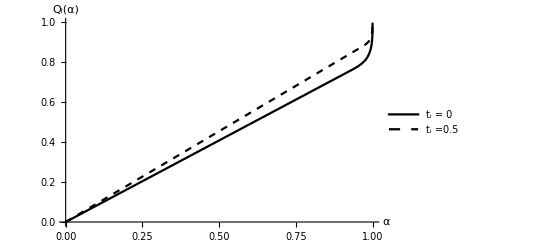

```mathematica
s11111sol05=Part[s11111sol,{Position[s11111sol,0.5][[1,1]]}][[1,2]];
s11111sol00=Part[s11111sol,{Position[s11111sol,0.0][[1,1]]}][[1,2]];
wj=1; σ=3.8; k=4; τij=τji=1.2; Ni=Nj=100; tj=0.1;
figureS8=Plot[{Piecewise[{{seg1Li[α,σ,k,0]/.s11111sol00,0≤α<α1i[ϕii,ϕij,σ, k, 0]/.s11111sol00},{seg2Li[α,ϕii,ϕij,σ, k, 0]/.s11111sol00,(α1i[ϕii,ϕij,σ, k, 0]/.s11111sol00)≤α<α2i[ϕii,ϕij,σ, k, 0]/.s11111sol00},{seg3Li[α,ϕii,ϕij,σ, k, 0]/.s11111sol00,(α2i[ϕii,ϕij,σ, k, 0]/.s11111sol00)≤α<1}}],Piecewise[{{seg1Lj[α,σ,k,0.5]/.s11111sol05,0≤α<α1j[ϕjj,ϕji,σ, k, 0.5]/.s11111sol05},{seg2Lj[α,ϕjj,ϕji,σ, k, 0.5]/.s11111sol05,(α1j[ϕjj,ϕji,σ, k, 0.5]/.s11111sol05)≤α<α2j[ϕjj,ϕji,σ, k, 0.5]/.s11111sol05},{seg3Lj[α,ϕjj,ϕji,σ, k, 0.5]/.s11111sol05,(α2j[ϕjj,ϕji,σ, k, 0.5]/.s11111sol05)≤α<1}}]
},{α,0,1}, 
PlotStyle->{{Black},{Dashed, Black}}, 
PlotLegends->Placed[LineLegend[{"t_i = 0","t_i =0.5"},LegendFunction->Panel,LegendMargins->1],{0.3,0.75}],
AxesLabel->{"α","Q_i(α)"},
AxesStyle->Directive[ Black],
AxesOrigin->{0,0},
PlotRange->Full]
Export["UnilateralTax_Figure_S8.pdf",figureS8];
```

### Figure S.9 : Social welfare function based on the Gini coefficient across scenarios

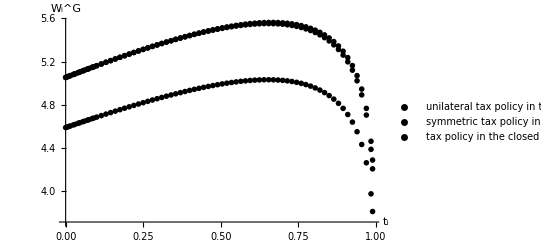

```mathematica
figureS9=ListPlot[{s11111welGi,s21111welGi,s12111welGi}
, PlotLegends->Placed[PointLegend[{"unilateral tax policy in the open economy","symmetric tax policy in the open economy", "tax policy in the closed economy"}
,LegendFunction->Panel,LegendMargins->1],{0.55,0.3}]
,AxesLabel->{"t_i","W_i^G"},AxesStyle->Directive[ Black]
,PlotMarkers->{"OpenMarkers",Tiny}
, MaxPlotPoints->75
,PlotStyle->Black
, PlotRange->Full]
Export["UnilateralTax_Figure_S9.pdf",figureS9];
```

### Table S.6 : Optimal tax rates (t_i^opt) for different parameter choices across scenarios

```mathematica
Grid[s11111topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s11211topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s11111btopti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s21111topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s21211topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s21111btopti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s12111topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s12211topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s12111btopti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
```

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.05
t_i^opt|θ=0.25 | 0.455
t_i^opt|θ=0.5 | 0.545
t_i^opt|θ=1.0 | 0.6
t_i^opt|θ=1.5 | 0.62
t_i^opt|θ=2.0 | 0.63
t_i^opt|θ→∞ | 0.665
t_i^opt|Sen | 0.665

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.005
t_i^opt|θ=0.25 | 0.07
t_i^opt|θ=0.5 | 0.12
t_i^opt|θ=1.0 | 0.175
t_i^opt|θ=1.5 | 0.205
t_i^opt|θ=2.0 | 0.225
t_i^opt|θ→∞ | 0.33
t_i^opt|Sen | 0.315

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.
t_i^opt|θ=0.25 | 0.035
t_i^opt|θ=0.5 | 0.065
t_i^opt|θ=1.0 | 0.1
t_i^opt|θ=1.5 | 0.125
t_i^opt|θ=2.0 | 0.14
t_i^opt|θ→∞ | 0.23
t_i^opt|Sen | 0.205

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.05
t_i^opt|θ=0.25 | 0.445
t_i^opt|θ=0.5 | 0.535
t_i^opt|θ=1.0 | 0.59
t_i^opt|θ=1.5 | 0.61
t_i^opt|θ=2.0 | 0.62
t_i^opt|θ→∞ | 0.655
t_i^opt|Sen | 0.655

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.25 | 0.07
t_i^opt|θ=0.5 | 0.12
t_i^opt|θ=1.0 | 0.175
t_i^opt|θ=1.5 | 0.205
t_i^opt|θ=2.0 | 0.225
t_i^opt|θ→∞ | 0.33
t_i^opt|Sen | 0.315

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.25 | 0.035
t_i^opt|θ=0.5 | 0.06
t_i^opt|θ=1.0 | 0.1
t_i^opt|θ=1.5 | 0.12
t_i^opt|θ=2.0 | 0.14
t_i^opt|θ→∞ | 0.225
t_i^opt|Sen | 0.2

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.04
t_i^opt|θ=0.25 | 0.405
t_i^opt|θ=0.5 | 0.5
t_i^opt|θ=1.0 | 0.565
t_i^opt|θ=1.5 | 0.59
t_i^opt|θ=2.0 | 0.605
t_i^opt|θ→∞ | 0.655
t_i^opt|Sen | 0.65

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.25 | 0.055
t_i^opt|θ=0.5 | 0.095
t_i^opt|θ=1.0 | 0.145
t_i^opt|θ=1.5 | 0.18
t_i^opt|θ=2.0 | 0.2
t_i^opt|θ→∞ | 0.33
t_i^opt|Sen | 0.305

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.25 | 0.02
t_i^opt|θ=0.5 | 0.04
t_i^opt|θ=1.0 | 0.065
t_i^opt|θ=1.5 | 0.09
t_i^opt|θ=2.0 | 0.105
t_i^opt|θ→∞ | 0.225
t_i^opt|Sen | 0.18